# 8. ÁRBOLES, COLORACIÓN DE UN GRAFO Y GRAFOS PLANOS

*Las entradas de cada ejemplo deben ser ejecutados en orden para su correcto funcionamiento.

1.COLORACIÓN DE UN GRAFO

### 1.1. COLORACIONES ÓPTIMAS

#### Función 8.1. NCOLORACIONES[]

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

#### Función 8.2. NUMEROCROMATICO[]

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
```

#### Función 8.3. DIBUJAR[]

```mathematica
DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

#### Ejemplo 8.1.

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
```

```mathematica
matrizadyacencia={{0,1,1,0,0,0,0,0},{1,0,1,1,1,0,0,0},{1,1,0,0,1,1,0,0},{0,1,0,0,1,0,1,0},{0,1,1,1,0,1,0,0},{0,0,1,0,1,0,0,1},{0,0,0,1,0,0,0,1},{0,0,0,0,0,1,1,0}};
```

```mathematica
n=8;
K=Table[If[i==j,0,1],{i,n},{j,n}];
```

```mathematica
NUMEROCROMATICO[matrizadyacencia]
```

3

```mathematica
DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Verde

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Verde

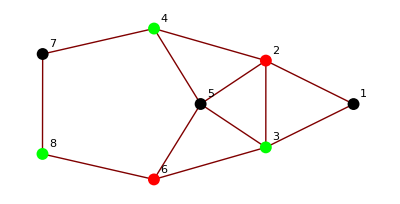

```mathematica
DIBUJAR[matrizadyacencia]
```

```mathematica
<<Combinatorica`
```

```mathematica
ChromaticNumber[FromAdjacencyMatrix[matrizadyacencia]]
```

3

```mathematica
MinimumVertexColoring[FromAdjacencyMatrix[matrizadyacencia]]
```

{1,2,3,3,1,2,1,3}

#### Ejemplo 8.2.

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
matrizadyacencia={{0,1,1,0,0,0,0,0},{1,0,1,1,1,0,0,0},{1,1,0,0,1,1,0,0},{0,1,0,0,1,0,1,0},{0,1,1,1,0,1,0,0},{0,0,1,0,1,0,0,1},{0,0,0,1,0,0,0,1},{0,0,0,0,0,1,1,0}};
```

```mathematica
Length[Complement[NCOLORACIONES[matrizadyacencia,4],NCOLORACIONES[matrizadyacencia,3]]]
```

1278

```mathematica
coloraciones=NCOLORACIONES[matrizadyacencia,3]
```

{{1,2,3,3,1,2,1,3},{1,2,3,3,1,2,2,1},{1,2,3,3,1,2,2,3},{1,3,2,2,1,3,1,2},{1,3,2,2,1,3,3,1},{1,3,2,2,1,3,3,2},{2,1,3,3,2,1,1,2},{2,1,3,3,2,1,1,3},{2,1,3,3,2,1,2,3},{2,3,1,1,2,3,2,1},{2,3,1,1,2,3,3,1},{2,3,1,1,2,3,3,2},{3,1,2,2,3,1,1,2},{3,1,2,2,3,1,1,3},{3,1,2,2,3,1,3,2},{3,2,1,1,3,2,2,1},{3,2,1,1,3,2,2,3},{3,2,1,1,3,2,3,1}}

```mathematica
colores={"Negro","Rojo", "Verde", "Azul", "Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};
Do[
Print["COLORACIÓN ",j,":"];
Print[TableForm[Table[{Table[i,{i,Dimensions[matrizadyacencia][[1]]}],Table[colores[[coloraciones[[j]][[i]]]],{i,Dimensions[matrizadyacencia][[1]]}]}]]];
,{j,Length[coloraciones]}]
```

COLORACIÓN 1:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Negro | Rojo | Verde | Verde | Negro | Rojo | Negro | Verde

COLORACIÓN 2:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Negro | Rojo | Verde | Verde | Negro | Rojo | Rojo | Negro

COLORACIÓN 3:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Negro | Rojo | Verde | Verde | Negro | Rojo | Rojo | Verde

COLORACIÓN 4:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Negro | Verde | Rojo | Rojo | Negro | Verde | Negro | Rojo

COLORACIÓN 5:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Negro | Verde | Rojo | Rojo | Negro | Verde | Verde | Negro

COLORACIÓN 6:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Negro | Verde | Rojo | Rojo | Negro | Verde | Verde | Rojo

COLORACIÓN 7:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Rojo | Negro | Verde | Verde | Rojo | Negro | Negro | Rojo

COLORACIÓN 8:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Rojo | Negro | Verde | Verde | Rojo | Negro | Negro | Verde

COLORACIÓN 9:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Rojo | Negro | Verde | Verde | Rojo | Negro | Rojo | Verde

COLORACIÓN 10:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Rojo | Verde | Negro | Negro | Rojo | Verde | Rojo | Negro

COLORACIÓN 11:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Rojo | Verde | Negro | Negro | Rojo | Verde | Verde | Negro

COLORACIÓN 12:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Rojo | Verde | Negro | Negro | Rojo | Verde | Verde | Rojo

COLORACIÓN 13:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Verde | Negro | Rojo | Rojo | Verde | Negro | Negro | Rojo

COLORACIÓN 14:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Verde | Negro | Rojo | Rojo | Verde | Negro | Negro | Verde

COLORACIÓN 15:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Verde | Negro | Rojo | Rojo | Verde | Negro | Verde | Rojo

COLORACIÓN 16:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Verde | Rojo | Negro | Negro | Verde | Rojo | Rojo | Negro

COLORACIÓN 17:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Verde | Rojo | Negro | Negro | Verde | Rojo | Rojo | Verde

COLORACIÓN 18:

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Verde | Rojo | Negro | Negro | Verde | Rojo | Verde | Negro

#### Ejemplo 8.3.

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
```

```mathematica
n=8;
K=Table[If[i==j,0,1],{i,n},{j,n}];
Timing[NUMEROCROMATICO[K]]
```

{68.453,8}

#### Ejemplo 8.4.

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
Añadirlado2[matrizadyacencia_]:=Module[{},
listamatrices={};
grados={};

A=matrizadyacencia.matrizadyacencia;
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
AppendTo[grados,{A[[i,i]],A[[j,j]]}];

];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];

posiciones=Table[{i},{i,Length[grados]}];
Isomorfas={};Isomorfas2={};
While[posiciones≠{},
parte=Union[Position[grados,grados[[posiciones[[1,1]]]]],Position[grados,{grados[[posiciones[[1,1]],2]],grados[[posiciones[[1,1]],1]]}]];
parte2=parte;

If[Length[parte2]>1,

Do[
A1=listamatrices[[parte2[[1,1]]]].listamatrices[[parte2[[1,1]]]];
A2=listamatrices[[parte2[[k1,1]]]].listamatrices[[parte2[[k1,1]]]];

A3=A1.listamatrices[[parte2[[1,1]]]];
A4=A2.listamatrices[[parte2[[k1,1]]]];
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];
tabla4=Sort[Table[A4[[i1,i1]],{i1,n}]];

A5=A1.A1;
A6=A2.A2;
tabla5=Sort[Table[A5[[i1,i1]],{i1,n}]];
tabla6=Sort[Table[A6[[i1,i1]],{i1,n}]];


If[tabla3==tabla4 && tabla5==tabla6,
AppendTo[Isomorfas2,parte2[[k1]]];];

,{k1,2,Length[parte2]}];
parte2=Complement[parte2,Union[{parte[[1]]},Isomorfas2]];
Isomorfas=Union[Isomorfas,Isomorfas2];
Isomorfas2={};
];

posiciones=Complement[posiciones,parte];
];

listamatrices=Delete[listamatrices,Isomorfas]

];
```

```mathematica
tiempo=TimeUsed[];
nlados=15;
n=6;
matrizadyacencia=Table[0,{i,n},{j,n}];

listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado2[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

2.84217×10^-14. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 2 *************

DIVIDIMOS EN 2 CLASES

2.84217×10^-14. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 7 *************

DIVIDIMOS EN 5 CLASES

2.84217×10^-14. Total: 9

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 4 LADOS: 16 *************

DIVIDIMOS EN 9 CLASES

0.016. Total: 18

-------> Añadimos nuevo lado a 9 grafos

Van 1

************* DE 5 LADOS: 34 *************

DIVIDIMOS EN 15 CLASES

0.031. Total: 33

-------> Añadimos nuevo lado a 15 grafos

Van 1

************* DE 6 LADOS: 64 *************

DIVIDIMOS EN 21 CLASES

0.062. Total: 54

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 7 LADOS: 89 *************

DIVIDIMOS EN 24 CLASES

0.109. Total: 78

-------> Añadimos nuevo lado a 24 grafos

Van 1

************* DE 8 LADOS: 103 *************

DIVIDIMOS EN 24 CLASES

0.172. Total: 102

-------> Añadimos nuevo lado a 24 grafos

Van 1

************* DE 9 LADOS: 95 *************

DIVIDIMOS EN 21 CLASES

0.234. Total: 123

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 10 LADOS: 61 *************

DIVIDIMOS EN 15 CLASES

0.266. Total: 138

-------> Añadimos nuevo lado a 15 grafos

Van 1

************* DE 11 LADOS: 36 *************

DIVIDIMOS EN 9 CLASES

0.281. Total: 147

-------> Añadimos nuevo lado a 9 grafos

Van 1

************* DE 12 LADOS: 14 *************

DIVIDIMOS EN 5 CLASES

0.281. Total: 152

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 13 LADOS: 6 *************

DIVIDIMOS EN 2 CLASES

0.281. Total: 154

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 14 LADOS: 2 *************

DIVIDIMOS EN 1 CLASES

0.281. Total: 155

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 15 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

0.281. Total: 156

Totales: 156 Tiempo empleado: 0.281

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
```

54

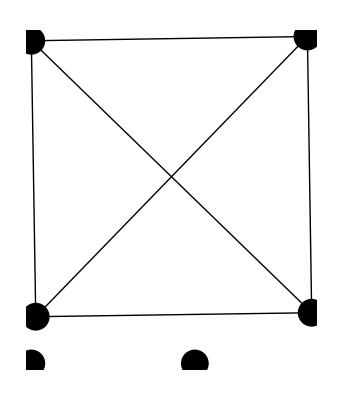

68

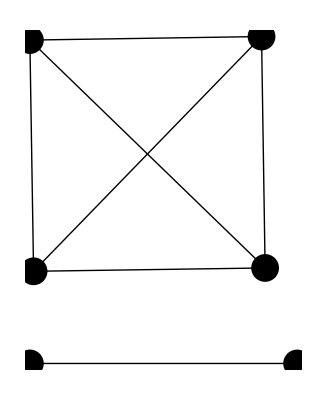

78

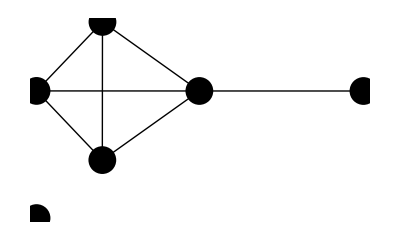

93

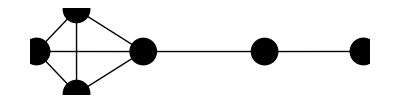

100

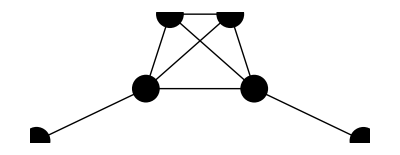

101

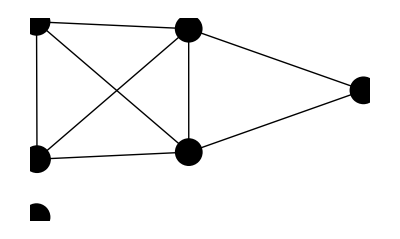

102

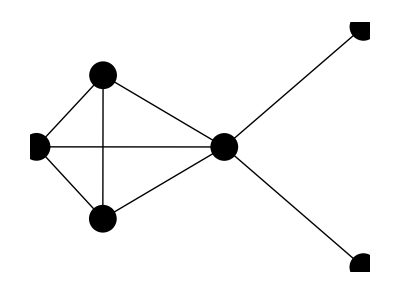

103

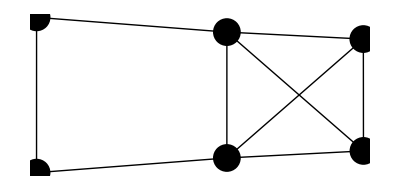

112

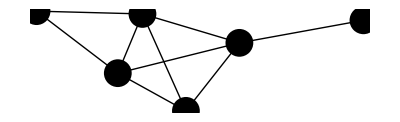

114

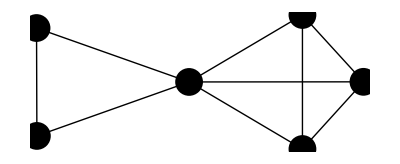

115

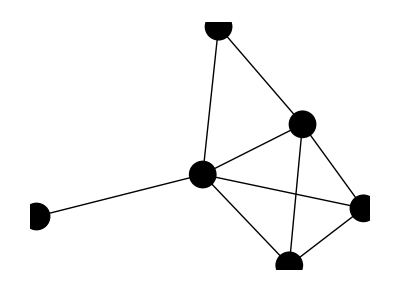

116

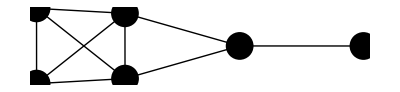

123

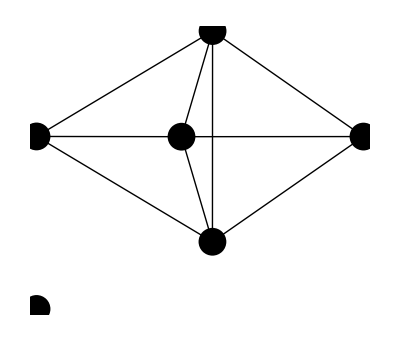

124

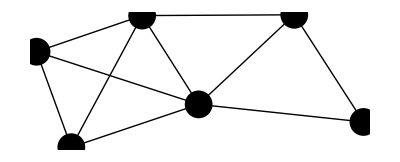

125

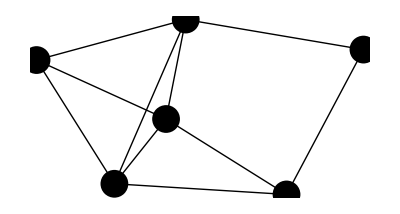

126

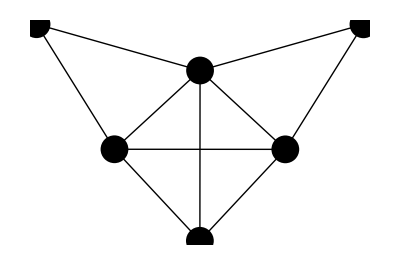

128

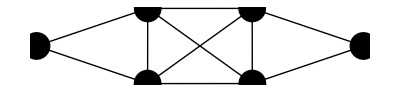

131

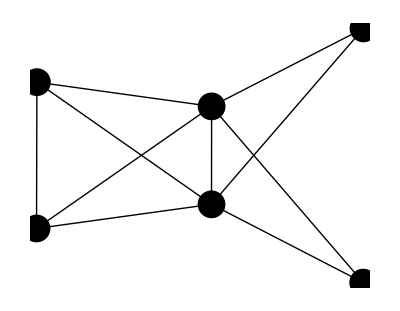

134

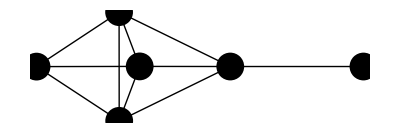

135

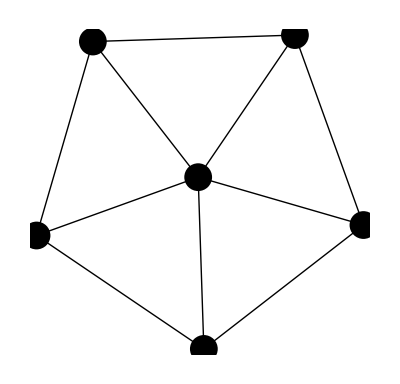

137

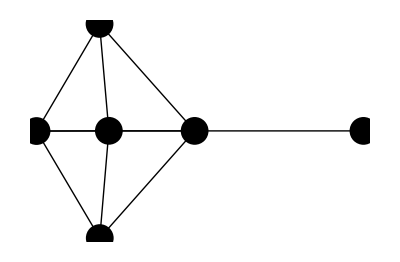

139

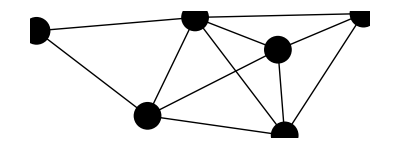

140

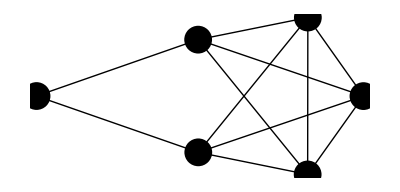

141

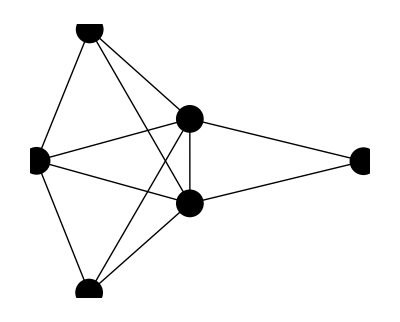

142

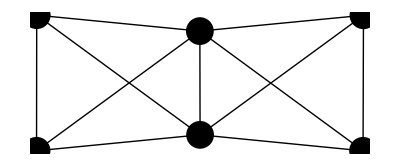

143

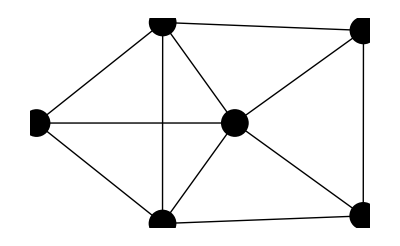

145

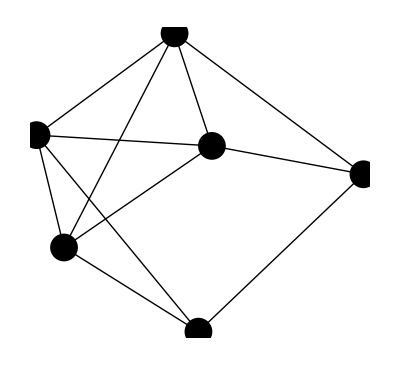

149

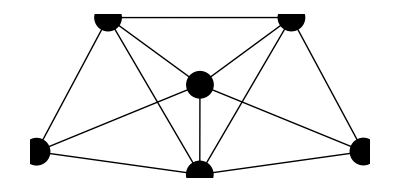

150

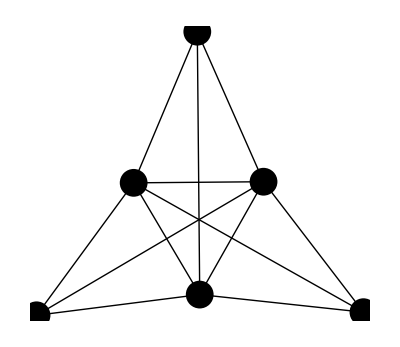

152

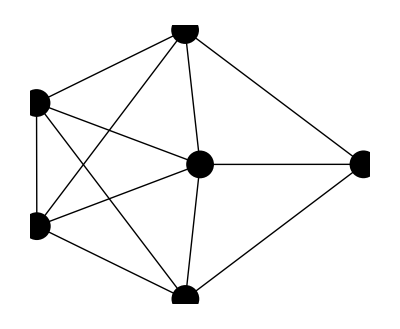

153

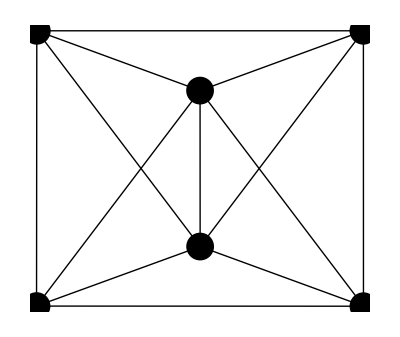

```mathematica
Do[
If[NUMEROCROMATICO[listamatrices1[[i]]]==4
,Print[i];
Print[GraphPlot[listamatrices1[[i]],PlotStyle->{Black,PointSize[.05]}]];
];
,{i,Length[listamatrices1]}]
```

### 1.2. EFICACIA

#### Función 8.4. COLOREAR[]

```mathematica
COLOREAR[matrizadyacencia_]:=Module[{COLORES,colores,color,coloreartemp,i,j},colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};colorear={1};color=1;Do[coloreartemp=colorear;Do[If[matrizadyacencia⟦j,i⟧==1,coloreartemp=Complement[coloreartemp,{colorear⟦j⟧}]];,{j,i-1}];If[coloreartemp=={},color++;AppendTo[colorear,color];,AppendTo[colorear,coloreartemp⟦1⟧];];,{i,2,Dimensions[matrizadyacencia]⟦1⟧}];Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]]
```

#### Ejemplo 8.5.

```mathematica
COLOREAR[matrizadyacencia_]:=Module[{COLORES,colores,color,coloreartemp,i,j},colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};colorear={1};color=1;Do[coloreartemp=colorear;Do[If[matrizadyacencia⟦j,i⟧==1,coloreartemp=Complement[coloreartemp,{colorear⟦j⟧}]];,{j,i-1}];If[coloreartemp=={},color++;AppendTo[colorear,color];,AppendTo[colorear,coloreartemp⟦1⟧];];,{i,2,Dimensions[matrizadyacencia]⟦1⟧}];Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]]
```

A)

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

Vértice 6, color Rojo

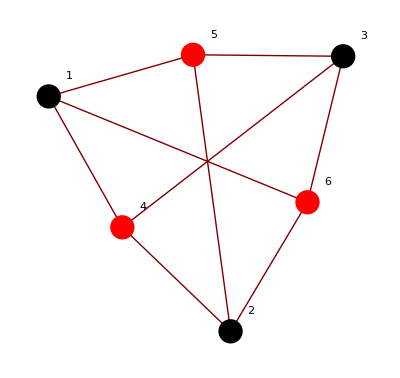

```mathematica
n=3;m=3;
matrizadyacencia=Table[If[(i≤n &&j≤n)||(i>n &&j>n),0,1]
,{i,n+m},{j,n+m}];
COLOREAR[matrizadyacencia]
```

B)

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Azul

Vértice 5, color Amarillo

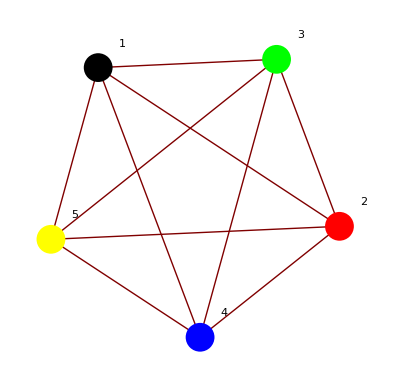

```mathematica
matrizadyacencia=Table[If[i==j,0,1],{i,5},{j,5}];
COLOREAR[matrizadyacencia]
```

C)

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Verde

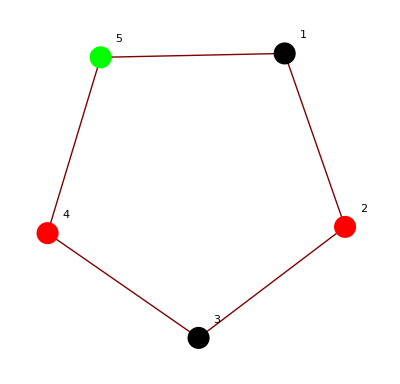

```mathematica
matrizadyacencia={{0,1,0,0,1},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{1,0,0,1,0}};
COLOREAR[matrizadyacencia]
```

#### Ejemplo 8.6.

```mathematica
COLOREAR[matrizadyacencia_]:=Module[{COLORES,colores,color,coloreartemp,i,j},colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};colorear={1};color=1;Do[coloreartemp=colorear;Do[If[matrizadyacencia⟦j,i⟧==1,coloreartemp=Complement[coloreartemp,{colorear⟦j⟧}]];,{j,i-1}];If[coloreartemp=={},color++;AppendTo[colorear,color];,AppendTo[colorear,coloreartemp⟦1⟧];];,{i,2,Dimensions[matrizadyacencia]⟦1⟧}];Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]]
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Rojo

Vértice 4, color Rojo

Vértice 5, color Verde

Vértice 6, color Verde

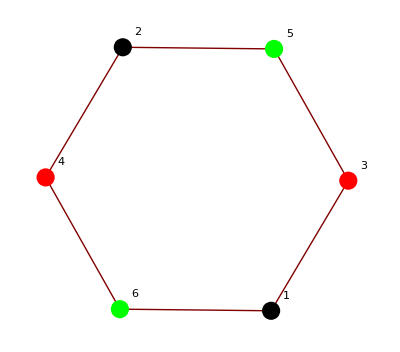

```mathematica
matrizadyacencia={{0,0,1,0,0,1},{0,0,0,1,1,0},{1,0,0,0,1,0},{0,1,0,0,0,1},{0,1,1,0,0,0},{1,0,0,1,0,0}};
COLOREAR[matrizadyacencia]
```

#### Función 8.5. COLOREAR2[]

```mathematica
COLOREAR2[matrizadyacencia_]:=Module[{colores,vertices,color,cont,COLORES,adyacen,colorusado,vert,colornoady,j,k,i},colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};vertices={1};colorear={1};color=1;cont=1;While[Length[vertices]<Dimensions[matrizadyacencia]⟦1⟧,adyacen=Position[matrizadyacencia⟦vertices⟦cont⟧⟧,1];adyacen=Complement[adyacen,Table[{vertices⟦k⟧},{k,Length[vertices]}]];Do[If[(adyacen⟦i⟧)∩vertices=={},vert=adyacen⟦i⟧⟦1⟧;colorusado={};Do[If[matrizadyacencia⟦adyacen⟦i⟧⟦1⟧,vertices⟦j⟧⟧==1,colorusado=colorusado∪{colorear⟦j⟧}];,{j,Length[vertices]}];coloresnoady=Complement[Table[cc,{cc,color}],colorusado];If[coloresnoady=={},color++;AppendTo[colorear,color];,AppendTo[colorear,Sort[coloresnoady]⟦1⟧];];AppendTo[vertices,vert];];,{i,Length[adyacen]}];cont++;];coloreartemp=Table[0,{i,Length[colorear]}];Do[coloreartemp⟦vertices⟦i⟧⟧=colorear⟦i⟧,{i,Length[colorear]}];colorear=coloreartemp;Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];
Print[GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]];
]
```

#### Ejemplo 8.7.

```mathematica
CONEXO[A_]:=Module[{i,j,B},
B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
conexo=True;
Do[
Do[If[i≠j && B[[i,j]]==0,conexo=False;];
,{i,Dimensions[B][[1]]}];
,{j,Dimensions[B][[1]]}];
conexo
]
```

```mathematica
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto≠{},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]≠0,AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];
componentesconexas
]
```

```mathematica
COLOREAR2[matrizadyacencia_]:=Module[{colores,vertices,color,cont,COLORES,adyacen,colorusado,vert,colornoady,j,k,i},colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};vertices={1};colorear={1};color=1;cont=1;While[Length[vertices]<Dimensions[matrizadyacencia]⟦1⟧,adyacen=Position[matrizadyacencia⟦vertices⟦cont⟧⟧,1];adyacen=Complement[adyacen,Table[{vertices⟦k⟧},{k,Length[vertices]}]];Do[If[(adyacen⟦i⟧)∩vertices=={},vert=adyacen⟦i⟧⟦1⟧;colorusado={};Do[If[matrizadyacencia⟦adyacen⟦i⟧⟦1⟧,vertices⟦j⟧⟧==1,colorusado=colorusado∪{colorear⟦j⟧}];,{j,Length[vertices]}];coloresnoady=Complement[Table[cc,{cc,color}],colorusado];If[coloresnoady=={},color++;AppendTo[colorear,color];,AppendTo[colorear,Sort[coloresnoady]⟦1⟧];];AppendTo[vertices,vert];];,{i,Length[adyacen]}];cont++;];coloreartemp=Table[0,{i,Length[colorear]}];Do[coloreartemp⟦vertices⟦i⟧⟧=colorear⟦i⟧,{i,Length[colorear]}];colorear=coloreartemp;Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];
Print[GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]];
]
```

```mathematica
matrizadyacencia={{0,0,1,0,0,1,0,0,0,0},{0,0,0,1,1,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0},{0,1,1,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,1,0,0}};
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Negro

Vértice 6, color Rojo

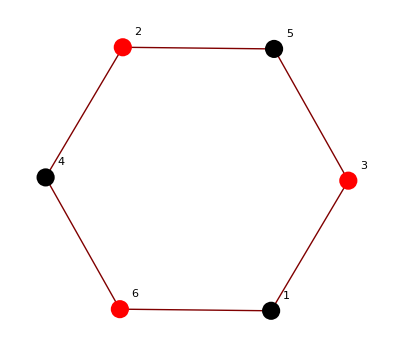

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Rojo

Vértice 4, color Rojo

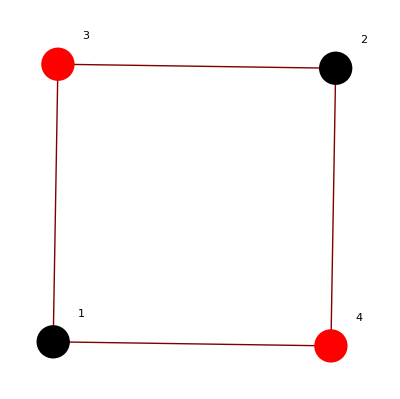

```mathematica
If[CONEXO[matrizadyacencia],
COLOREAR2[matrizadyacencia];
,
 comp=COMPONENTESCONEXAS[matrizadyacencia]
Do[
COLOREAR2[Table[matrizadyacencia[[comp[[h]][[i]],comp[[h]][[j]]]],{i,Length[comp[[h]]]},{j,Length[comp[[h]]]}]];
,{h,Length[comp]}];
];
```

#### Ejemplo 8.8.

```mathematica
matrizadyacencia={{0,1,1,0,0,0,0,0},{1,0,1,1,1,0,0,0},{1,1,0,0,1,1,0,0},{0,1,0,0,1,0,1,0},{0,1,1,1,0,1,0,0},{0,0,1,0,1,0,0,1},{0,0,0,1,0,0,0,1},{0,0,0,0,0,1,1,0}};
```

```mathematica
COLOREAR2[matrizadyacencia_]:=Module[{colores,vertices,color,cont,COLORES,adyacen,colorusado,vert,colornoady,j,k,i},colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};vertices={1};colorear={1};color=1;cont=1;While[Length[vertices]<Dimensions[matrizadyacencia]⟦1⟧,adyacen=Position[matrizadyacencia⟦vertices⟦cont⟧⟧,1];adyacen=Complement[adyacen,Table[{vertices⟦k⟧},{k,Length[vertices]}]];Do[If[(adyacen⟦i⟧)∩vertices=={},vert=adyacen⟦i⟧⟦1⟧;colorusado={};Do[If[matrizadyacencia⟦adyacen⟦i⟧⟦1⟧,vertices⟦j⟧⟧==1,colorusado=colorusado∪{colorear⟦j⟧}];,{j,Length[vertices]}];coloresnoady=Complement[Table[cc,{cc,color}],colorusado];If[coloresnoady=={},color++;AppendTo[colorear,color];,AppendTo[colorear,Sort[coloresnoady]⟦1⟧];];AppendTo[vertices,vert];];,{i,Length[adyacen]}];cont++;];coloreartemp=Table[0,{i,Length[colorear]}];Do[coloreartemp⟦vertices⟦i⟧⟧=colorear⟦i⟧,{i,Length[colorear]}];colorear=coloreartemp;Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];
Print[GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]];
]
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Negro

Vértice 5, color Azul

Vértice 6, color Negro

Vértice 7, color Rojo

Vértice 8, color Verde

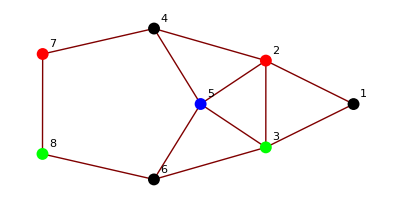

```mathematica
COLOREAR2[matrizadyacencia]
```

#### Función 8.6. COLOREAR3[]

```mathematica
COLOREAR3[matrizadyacencia_]:=Module[{color,j,t,k,adyacentes,i,nocolorear},colorear=Table[0,{i,Dimensions[matrizadyacencia]⟦1⟧}];colorear⟦1⟧=1;color=1;t=1;While[t<Dimensions[matrizadyacencia]⟦1⟧,Do[If[colorear⟦k⟧==0,nocolorear=False;adyacentes=Position[matrizadyacencia⟦k⟧,1];Do[If[colorear⟦adyacentes⟦j⟧⟦1⟧⟧==color,nocolorear=True;Break[];],{j,Length[adyacentes]}];If[!nocolorear,colorear⟦k⟧=color;t++;];];,{k,Dimensions[matrizadyacencia]⟦1⟧}];color++;];colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]];
```

#### Ejemplo 8.9.

```mathematica
BCadyacencia[n_,m_]:=Table[If[(i≤n &&j≤n)||(i>n &&j>n),0,1],{i,n+m},{j,n+m}];
```

```mathematica
COLOREAR3[matrizadyacencia_]:=Module[{color,j,t,k,adyacentes,i,nocolorear},colorear=Table[0,{i,Dimensions[matrizadyacencia]⟦1⟧}];colorear⟦1⟧=1;color=1;t=1;While[t<Dimensions[matrizadyacencia]⟦1⟧,Do[If[colorear⟦k⟧==0,nocolorear=False;adyacentes=Position[matrizadyacencia⟦k⟧,1];Do[If[colorear⟦adyacentes⟦j⟧⟦1⟧⟧==color,nocolorear=True;Break[];],{j,Length[adyacentes]}];If[!nocolorear,colorear⟦k⟧=color;t++;];];,{k,Dimensions[matrizadyacencia]⟦1⟧}];color++;];colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]];
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

Vértice 6, color Rojo

Vértice 7, color Rojo

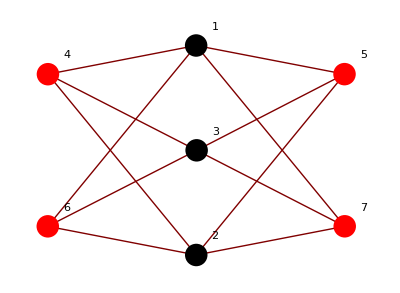

```mathematica
A=BCadyacencia[3,4];
COLOREAR3[A]
```

#### Ejemplo 8.10.

```mathematica
COLOREAR3[matrizadyacencia_]:=Module[{color,j,t,k,adyacentes,i,nocolorear},colorear=Table[0,{i,Dimensions[matrizadyacencia]⟦1⟧}];colorear⟦1⟧=1;color=1;t=1;While[t<Dimensions[matrizadyacencia]⟦1⟧,Do[If[colorear⟦k⟧==0,nocolorear=False;adyacentes=Position[matrizadyacencia⟦k⟧,1];Do[If[colorear⟦adyacentes⟦j⟧⟦1⟧⟧==color,nocolorear=True;Break[];],{j,Length[adyacentes]}];If[!nocolorear,colorear⟦k⟧=color;t++;];];,{k,Dimensions[matrizadyacencia]⟦1⟧}];color++;];colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]];
```

```mathematica
matrizadyacencia={{0,1,1,0,0,0,0,0},{1,0,1,1,1,0,0,0},{1,1,0,0,1,1,0,0},{0,1,0,0,1,0,1,0},{0,1,1,1,0,1,0,0},{0,0,1,0,1,0,0,1},{0,0,0,1,0,0,0,1},{0,0,0,0,0,1,1,0}};
COLOREAR3[matrizadyacencia]
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Negro

Vértice 5, color Azul

Vértice 6, color Negro

Vértice 7, color Rojo

Vértice 8, color Verde

-Graphics-

#### Ejemplo 8.11.

```mathematica
A={{0,1,0,1,0,0,1,0,0,0,0,0},{1,0,1,0,1,0,0,1,0,0,0,0},
      {0,1,0,0,0,1,0,0,1,0,0,1},{1,0,0,0,1,0,0,0,0,1,0,0},
      {0,1,0,1,0,1,0,0,0,0,1,0},{0,0,1,0,1,0,0,0,1,0,0,1},
      {1,0,0,0,0,0,0,1,0,1,0,0},{0,1,0,0,0,0,1,0,1,0,1,0},
      {0,0,1,0,0,1,0,1,0,0,0,1},{0,0,0,1,0,0,1,0,0,0,1,0},
      {0,0,0,0,1,0,0,1,0,1,0,1},{0,0,1,0,0,1,0,0,1,0,1,0}};
```

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
```

```mathematica
DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Rojo

Vértice 8, color Negro

Vértice 9, color Verde

Vértice 10, color Negro

Vértice 11, color Rojo

Vértice 12, color Azul

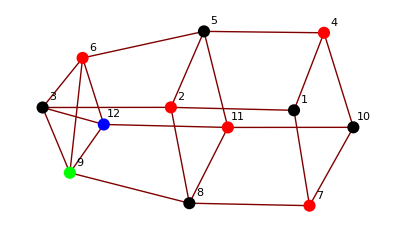
{23.563,-Graphics-}

```mathematica
Timing[DIBUJAR[A]]
```

```mathematica
COLOREAR[matrizadyacencia_]:=Module[{COLORES,colores,color,coloreartemp,i,j},colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};colorear={1};color=1;Do[coloreartemp=colorear;Do[If[matrizadyacencia⟦j,i⟧==1,coloreartemp=Complement[coloreartemp,{colorear⟦j⟧}]];,{j,i-1}];If[coloreartemp=={},color++;AppendTo[colorear,color];,AppendTo[colorear,coloreartemp⟦1⟧];];,{i,2,Dimensions[matrizadyacencia]⟦1⟧}];Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]]
```

```mathematica
COLOREAR2[matrizadyacencia_]:=Module[{colores,vertices,color,cont,COLORES,adyacen,colorusado,vert,colornoady,j,k,i},colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};vertices={1};colorear={1};color=1;cont=1;While[Length[vertices]<Dimensions[matrizadyacencia]⟦1⟧,adyacen=Position[matrizadyacencia⟦vertices⟦cont⟧⟧,1];adyacen=Complement[adyacen,Table[{vertices⟦k⟧},{k,Length[vertices]}]];Do[If[(adyacen⟦i⟧)∩vertices=={},vert=adyacen⟦i⟧⟦1⟧;colorusado={};Do[If[matrizadyacencia⟦adyacen⟦i⟧⟦1⟧,vertices⟦j⟧⟧==1,colorusado=colorusado∪{colorear⟦j⟧}];,{j,Length[vertices]}];coloresnoady=Complement[Table[cc,{cc,color}],colorusado];If[coloresnoady=={},color++;AppendTo[colorear,color];,AppendTo[colorear,Sort[coloresnoady]⟦1⟧];];AppendTo[vertices,vert];];,{i,Length[adyacen]}];cont++;];coloreartemp=Table[0,{i,Length[colorear]}];Do[coloreartemp⟦vertices⟦i⟧⟧=colorear⟦i⟧,{i,Length[colorear]}];colorear=coloreartemp;Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];
Print[GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]];
]
```

```mathematica
COLOREAR3[matrizadyacencia_]:=Module[{color,j,t,k,adyacentes,i,nocolorear},colorear=Table[0,{i,Dimensions[matrizadyacencia]⟦1⟧}];colorear⟦1⟧=1;color=1;t=1;While[t<Dimensions[matrizadyacencia]⟦1⟧,Do[If[colorear⟦k⟧==0,nocolorear=False;adyacentes=Position[matrizadyacencia⟦k⟧,1];Do[If[colorear⟦adyacentes⟦j⟧⟦1⟧⟧==color,nocolorear=True;Break[];],{j,Length[adyacentes]}];If[!nocolorear,colorear⟦k⟧=color;t++;];];,{k,Dimensions[matrizadyacencia]⟦1⟧}];color++;];colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]];
```

```mathematica
Timing[COLOREAR[A]][[1]]
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Rojo

Vértice 8, color Negro

Vértice 9, color Verde

Vértice 10, color Negro

Vértice 11, color Rojo

Vértice 12, color Azul

0.016

```mathematica
Timing[COLOREAR2[A]][[1]]
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Rojo

Vértice 8, color Negro

Vértice 9, color Verde

Vértice 10, color Negro

Vértice 11, color Rojo

Vértice 12, color Azul

-Graphics-

0.047

```mathematica
Timing[COLOREAR3[A]][[1]]
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Rojo

Vértice 8, color Negro

Vértice 9, color Verde

Vértice 10, color Negro

Vértice 11, color Rojo

Vértice 12, color Azul

0.

```mathematica
<<Combinatorica`
```

```mathematica
Timing[VertexColoring[FromAdjacencyMatrix[A]]][[1]]
```

0.

### 1.2. EL POLINOMIO CROMÁTICO

#### Función 8.7. POLINOMIOCROMATICO[]

```mathematica
p[matrizadyacencia_,lambda_]:=Length[NCOLORACIONES[matrizadyacencia,lambda]];
```

```mathematica
POLINOMIOCROMATICO[matrizadyacencia_]:=Module[{datos,j},
datos={};
Do[
AppendTo[datos,{j,p[matrizadyacencia,j]}];
,{j,0,Dimensions[matrizadyacencia][[1]]}];
Factor[InterpolatingPolynomial[datos,x]]
]
```

#### Ejemplo 8.12.

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
p[matrizadyacencia_,lambda_]:=Length[NCOLORACIONES[matrizadyacencia,lambda]];
```

```mathematica
POLINOMIOCROMATICO[matrizadyacencia_]:=Module[{datos,j},
datos={};
Do[
AppendTo[datos,{j,p[matrizadyacencia,j]}];
,{j,0,Dimensions[matrizadyacencia][[1]]}];
Factor[InterpolatingPolynomial[datos,x]]
]
```

```mathematica
matrizadyacencia={{0,1,0,0,0,0},{1,0,1,1,1,1},{0,1,0,0,0,0},{0,1,0,0,1,0},{0,1,0,1,0,1},{0,1,0,0,1,0}};
POLINOMIOCROMATICO[matrizadyacencia]
```

(-2+x)^2 (-1+x)^3 x

```mathematica
<<Combinatorica`
```

```mathematica
Factor[ChromaticPolynomial[FromAdjacencyMatrix[matrizadyacencia],x]]
```

(-2+x)^2 (-1+x)^3 x

#### Función 8.8. POLINOMIOCROMATICO2[]

```mathematica
POLINOMIOCROMATICO2[matrizadyacencia_]:=Module[{comp,h,i,j},
comp=COMPONENTESCONEXAS[matrizadyacencia];
polinomio=1;
Do[
polinomio=polinomio*(POLINOMIOCROMATICO[Table[matrizadyacencia[[comp[[h]][[i]],comp[[h]][[j]]]],{i,Length[comp[[h]]]},{j,Length[comp[[h]]]}]]);
,{h,Length[comp]}];
polinomio
];
```

#### Ejemplo 8.13.

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
p[matrizadyacencia_,lambda_]:=Length[NCOLORACIONES[matrizadyacencia,lambda]];
```

```mathematica
POLINOMIOCROMATICO[matrizadyacencia_]:=Module[{datos,j},
datos={};
Do[
AppendTo[datos,{j,p[matrizadyacencia,j]}];
,{j,0,Dimensions[matrizadyacencia][[1]]}];
Factor[InterpolatingPolynomial[datos,x]]
]
```

```mathematica
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto≠{},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]≠0,AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];
componentesconexas
]
```

```mathematica
POLINOMIOCROMATICO2[matrizadyacencia_]:=Module[{comp,h,i,j},
comp=COMPONENTESCONEXAS[matrizadyacencia];
polinomio=1;
Do[
polinomio=polinomio*(POLINOMIOCROMATICO[Table[matrizadyacencia[[comp[[h]][[i]],comp[[h]][[j]]]],{i,Length[comp[[h]]]},{j,Length[comp[[h]]]}]]);
,{h,Length[comp]}];
polinomio
];
```

```mathematica
matrizadyacencia={{0,0,1,0,0,1,0,0,0,0},{0,0,0,1,1,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0},{0,1,1,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,1,0,0}};
```

```mathematica
Timing[POLINOMIOCROMATICO2[matrizadyacencia]]
```

{2.063,(-1+x)^2 x^2 (3-3 x+x^2) (5-10 x+10 x^2-5 x^3+x^4)}

#### Función 8.9. D1[]

```mathematica
D1[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),0,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

#### Función 8.10. D2[]

```mathematica
D2[matrizadyacencia_,i_,j_]:=Module[{k1,W,F,W1,F1,CONTi,CONTj},
W=Table[k1,{k1,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[k1,k2]]==1,AppendTo[F,k1->k2]];,{k1,k2}];
,{k2,Dimensions[matrizadyacencia][[1]]}];
F1={};
Do[
If[F[[k1]][[1]]≠j &&F[[k1]][[2]]≠j,
F1=Union[F1,{F[[k1]]}];
,
If[F[[k1]][[1]]≠i &&F[[k1]][[2]]≠i,
If[F[[k1]][[1]]==j,
F1=Union[F1,{i->F[[k1]][[2]]}];
,
F1=Union[F1,{F[[k1]][[1]]->i}];
]
];
];
,{k1,Length[F]}];
W1=Complement[W,{j}];
F1=Table[
Position[W1,F1[[k1]][[1]]][[1]]->Position[W1,F1[[k1]][[2]]][[1]]
,{k1,Length[F1]}];

matrizadyacencia1=Table[0,{CONTi,Length[W1]},{CONTj,Length[W1]}];
Do[matrizadyacencia1[[F1[[k,1]],F1[[k,2]]]]=1;
matrizadyacencia1[[F1[[k,2]],F1[[k,1]]]]=1;,{k,Length[F1]}];
matrizadyacencia1

]
```

#### Ejemplo 8.14.

```mathematica
D1[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),0,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

```mathematica
D2[matrizadyacencia_,i_,j_]:=Module[{k1,W,F,W1,F1,CONTi,CONTj},
W=Table[k1,{k1,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[k1,k2]]==1,AppendTo[F,k1->k2]];,{k1,k2}];
,{k2,Dimensions[matrizadyacencia][[1]]}];
F1={};
Do[
If[F[[k1]][[1]]≠j &&F[[k1]][[2]]≠j,
F1=Union[F1,{F[[k1]]}];
,
If[F[[k1]][[1]]≠i &&F[[k1]][[2]]≠i,
If[F[[k1]][[1]]==j,
F1=Union[F1,{i->F[[k1]][[2]]}];
,
F1=Union[F1,{F[[k1]][[1]]->i}];
]
];
];
,{k1,Length[F]}];
W1=Complement[W,{j}];
F1=Table[
Position[W1,F1[[k1]][[1]]][[1]]->Position[W1,F1[[k1]][[2]]][[1]]
,{k1,Length[F1]}];

matrizadyacencia1=Table[0,{CONTi,Length[W1]},{CONTj,Length[W1]}];
Do[matrizadyacencia1[[F1[[k,1]],F1[[k,2]]]]=1;
matrizadyacencia1[[F1[[k,2]],F1[[k,1]]]]=1;,{k,Length[F1]}];
matrizadyacencia1

]
```

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
p[matrizadyacencia_,lambda_]:=Length[NCOLORACIONES[matrizadyacencia,lambda]];
```

```mathematica
POLINOMIOCROMATICO[matrizadyacencia_]:=Module[{datos,j},
datos={};
Do[
AppendTo[datos,{j,p[matrizadyacencia,j]}];
,{j,0,Dimensions[matrizadyacencia][[1]]}];
Factor[InterpolatingPolynomial[datos,x]]
]
```

```mathematica
matrizadyacencia={{0,1,0,0,1},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{1,0,0,1,0}};
```

```mathematica
Factor[POLINOMIOCROMATICO[D1[matrizadyacencia,1,5]]-POLINOMIOCROMATICO[D2[matrizadyacencia,1,5]]]
```

(-2+x) (-1+x) x (2-2 x+x^2)

```mathematica
Factor[POLINOMIOCROMATICO[matrizadyacencia]]
```

(-2+x) (-1+x) x (2-2 x+x^2)

#### Ejemplo 8.15.

```mathematica
D1[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),0,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

```mathematica
D2[matrizadyacencia_,i_,j_]:=Module[{k1,W,F,W1,F1,CONTi,CONTj},
W=Table[k1,{k1,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[k1,k2]]==1,AppendTo[F,k1->k2]];,{k1,k2}];
,{k2,Dimensions[matrizadyacencia][[1]]}];
F1={};
Do[
If[F[[k1]][[1]]≠j &&F[[k1]][[2]]≠j,
F1=Union[F1,{F[[k1]]}];
,
If[F[[k1]][[1]]≠i &&F[[k1]][[2]]≠i,
If[F[[k1]][[1]]==j,
F1=Union[F1,{i->F[[k1]][[2]]}];
,
F1=Union[F1,{F[[k1]][[1]]->i}];
]
];
];
,{k1,Length[F]}];
W1=Complement[W,{j}];
F1=Table[
Position[W1,F1[[k1]][[1]]][[1]]->Position[W1,F1[[k1]][[2]]][[1]]
,{k1,Length[F1]}];

matrizadyacencia1=Table[0,{CONTi,Length[W1]},{CONTj,Length[W1]}];
Do[matrizadyacencia1[[F1[[k,1]],F1[[k,2]]]]=1;
matrizadyacencia1[[F1[[k,2]],F1[[k,1]]]]=1;,{k,Length[F1]}];
matrizadyacencia1

]
```

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
p[matrizadyacencia_,lambda_]:=Length[NCOLORACIONES[matrizadyacencia,lambda]];
```

```mathematica
POLINOMIOCROMATICO[matrizadyacencia_]:=Module[{datos,j},
datos={};
Do[
AppendTo[datos,{j,p[matrizadyacencia,j]}];
,{j,0,Dimensions[matrizadyacencia][[1]]}];
Factor[InterpolatingPolynomial[datos,x]]
]
```

```mathematica
A1={{0,1,0,1,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0},{1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1},{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1},{0,0,0,0,1,0,1,0}};
```

```mathematica
A2=D1[A1,4,5];
B2=D2[A1,4,5];
```

```mathematica
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto≠{},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]≠0,AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];
componentesconexas
]
```

```mathematica
POLINOMIOCROMATICO2[matrizadyacencia_]:=Module[{comp,h,i,j},
comp=COMPONENTESCONEXAS[matrizadyacencia];
polinomio=1;
Do[
polinomio=polinomio*(POLINOMIOCROMATICO[Table[matrizadyacencia[[comp[[h]][[i]],comp[[h]][[j]]]],{i,Length[comp[[h]]]},{j,Length[comp[[h]]]}]]);
,{h,Length[comp]}];
polinomio
];
```

```mathematica
POLINOMIOCROMATICO2[A2]
```

(-1+x)^2 x^2 (3-3 x+x^2)^2

```mathematica
A3=D1[B2,3,4];
B3=D2[B2,3,4];
```

```mathematica
POLINOMIOCROMATICO[B3]
```

(-2+x) (-1+x)^2 x (3-3 x+x^2)

```mathematica
A4=D1[A3,1,4];
B4=D2[A3,1,4];
POLINOMIOCROMATICO2[A4]
POLINOMIOCROMATICO[B4]
```

(-1+x)^3 x^2 (3-3 x+x^2)

(-1+x)^3 x (3-3 x+x^2)

```mathematica
Factor[POLINOMIOCROMATICO2[A2]-((POLINOMIOCROMATICO2[A4]-POLINOMIOCROMATICO[B4])-POLINOMIOCROMATICO[B3])]
```

(-1+x)^3 x (3-3 x+x^2)^2

#### Función 8.11. D3[]

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

#### Ejemplo 8.16.

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

```mathematica
D2[matrizadyacencia_,i_,j_]:=Module[{k1,W,F,W1,F1,CONTi,CONTj},
W=Table[k1,{k1,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[k1,k2]]==1,AppendTo[F,k1->k2]];,{k1,k2}];
,{k2,Dimensions[matrizadyacencia][[1]]}];
F1={};
Do[
If[F[[k1]][[1]]≠j &&F[[k1]][[2]]≠j,
F1=Union[F1,{F[[k1]]}];
,
If[F[[k1]][[1]]≠i &&F[[k1]][[2]]≠i,
If[F[[k1]][[1]]==j,
F1=Union[F1,{i->F[[k1]][[2]]}];
,
F1=Union[F1,{F[[k1]][[1]]->i}];
]
];
];
,{k1,Length[F]}];
W1=Complement[W,{j}];
F1=Table[
Position[W1,F1[[k1]][[1]]][[1]]->Position[W1,F1[[k1]][[2]]][[1]]
,{k1,Length[F1]}];

matrizadyacencia1=Table[0,{CONTi,Length[W1]},{CONTj,Length[W1]}];
Do[matrizadyacencia1[[F1[[k,1]],F1[[k,2]]]]=1;
matrizadyacencia1[[F1[[k,2]],F1[[k,1]]]]=1;,{k,Length[F1]}];
matrizadyacencia1

]
```

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
p[matrizadyacencia_,lambda_]:=Length[NCOLORACIONES[matrizadyacencia,lambda]];
```

```mathematica
POLINOMIOCROMATICO[matrizadyacencia_]:=Module[{datos,j},
datos={};
Do[
AppendTo[datos,{j,p[matrizadyacencia,j]}];
,{j,0,Dimensions[matrizadyacencia][[1]]}];
Factor[InterpolatingPolynomial[datos,x]]
]
```

```mathematica
A1={{0,1,1,1,1,1,1,0},{1,0,1,1,1,1,0,1},{1,1,0,1,0,1,1,1},{1,1,1,0,1,0,1,1},{1,1,0,1,0,1,1,1},{1,1,1,0,1,0,1,1},{1,0,1,1,1,1,0,1},{0,1,1,1,1,1,1,0}};
```

```mathematica
A2=D3[A1,1,8];
B2=D2[A1,1,8];
```

```mathematica
POLINOMIOCROMATICO[B2]
```

(-3+x) (-2+x) (-1+x) x (-71+50 x-12 x^2+x^3)

```mathematica
A3=D3[A2,2,7];
B3=D2[A2,2,7];
```

```mathematica
POLINOMIOCROMATICO[B3]
```

(-4+x) (-3+x) (-2+x) (-1+x) x (21-9 x+x^2)

```mathematica
A4=D3[A3,3,5];
B4=D2[A3,3,5];
```

```mathematica
POLINOMIOCROMATICO[B4]
```

(-5+x)^2 (-4+x) (-3+x) (-2+x) (-1+x) x

```mathematica
A5=D3[A4,4,6];
B5=D2[A4,4,6];
```

```mathematica
POLINOMIOCROMATICO[B5]
```

(-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x

```mathematica
POLINOMIOCROMATICO[A5]
```

(-7+x) (-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x

## 2. GRAFOS PLANOS

#### Función 8.12. QUITARVERTICESGRADO210[]

```mathematica
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
```

#### Función 8.13. K33[]

```mathematica
<<"Combinatorica`";
```

```mathematica
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
```

#### Función 8.14. HOMEOMORFOK5K33[]

```mathematica
HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]
```

#### Función 8.15. PLANO[]

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

#### Ejemplo 8.17.

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

```mathematica
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
```

```mathematica
<<"Combinatorica`";
```

```mathematica
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
```

```mathematica
HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

```mathematica
matrizadyacencia={{0,0,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,1,1,1,1,1,1,1,1},{1,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0}};
```

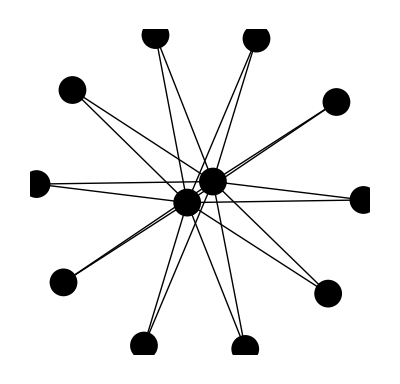

```mathematica
GraphPlot[matrizadyacencia,PlotStyle->{Black,PointSize[.05]}]
```

```mathematica
PLANO[matrizadyacencia]
```

True

```mathematica
PlanarQ[FromAdjacencyMatrix[matrizadyacencia]]
```

True

#### Ejemplo 8.18.

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

```mathematica
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
```

```mathematica
<<Combinatorica`;
```

```mathematica
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
```

```mathematica
HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{i,k},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
HOMEOMORFOK5K33v2[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
lados=0;
Do[
Do[
If[Nueva[[t1,t2]]==1,lados++];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

If[Dimensions[Nueva][[1]]==6 &&lados==9,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];

If[Dimensions[Nueva][[1]]==5 &&lados ==10,homeo=False;];
homeo
]
```

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

```mathematica
matrizadyacencia={{0,1,1,1,0,0,0,1},{1,0,1,1,0,0,0,1},{1,1,0,1,0,0,0,1},{1,1,1,0,1,1,0,0},{0,0,0,1,0,1,0,0},{0,0,0,1,1,0,1,1},{0,0,0,0,0,1,0,1},{1,1,1,0,0,1,1,0}};
```

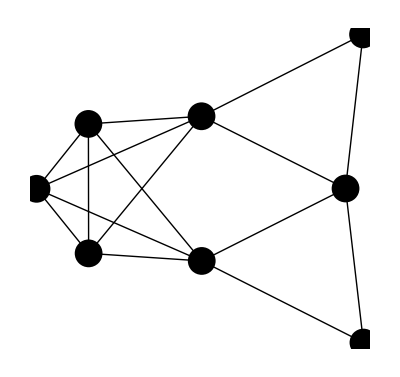

```mathematica
GraphPlot[matrizadyacencia,PlotStyle->{Black,PointSize[.05]}]
```

```mathematica
PLANO[matrizadyacencia]
```

False

```mathematica
subgrafo
```

{1→2,1→3,2→3,1→4,2→4,3→4,1→5,2→5,3→5,4→5}

#### Ejemplo 8.19.

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
Añadirlado2[matrizadyacencia_]:=Module[{},
listamatrices={};
grados={};

A=matrizadyacencia.matrizadyacencia;
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
AppendTo[grados,{A[[i,i]],A[[j,j]]}];

];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];

posiciones=Table[{i},{i,Length[grados]}];
Isomorfas={};Isomorfas2={};
While[posiciones≠{},
parte=Union[Position[grados,grados[[posiciones[[1,1]]]]],Position[grados,{grados[[posiciones[[1,1]],2]],grados[[posiciones[[1,1]],1]]}]];
parte2=parte;

If[Length[parte2]>1,

Do[
A1=listamatrices[[parte2[[1,1]]]].listamatrices[[parte2[[1,1]]]];
A2=listamatrices[[parte2[[k1,1]]]].listamatrices[[parte2[[k1,1]]]];

A3=A1.listamatrices[[parte2[[1,1]]]];
A4=A2.listamatrices[[parte2[[k1,1]]]];
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];
tabla4=Sort[Table[A4[[i1,i1]],{i1,n}]];

A5=A1.A1;
A6=A2.A2;
tabla5=Sort[Table[A5[[i1,i1]],{i1,n}]];
tabla6=Sort[Table[A6[[i1,i1]],{i1,n}]];


If[tabla3==tabla4 && tabla5==tabla6,
AppendTo[Isomorfas2,parte2[[k1]]];];

,{k1,2,Length[parte2]}];
parte2=Complement[parte2,Union[{parte[[1]]},Isomorfas2]];
Isomorfas=Union[Isomorfas,Isomorfas2];
Isomorfas2={};
];

posiciones=Complement[posiciones,parte];
];

listamatrices=Delete[listamatrices,Isomorfas]

];
```

```mathematica
nlados=9;
n=6;
matrizadyacencia={{0,1,0,0,0,1},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,0,0,0,1,0}};
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado2[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 4 *************

DIVIDIMOS EN 2 CLASES

0.. Total: 3

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 2 LADOS: 10 *************

DIVIDIMOS EN 6 CLASES

0.. Total: 9

-------> Añadimos nuevo lado a 6 grafos

Van 1

************* DE 3 LADOS: 24 *************

DIVIDIMOS EN 11 CLASES

0.016. Total: 20

-------> Añadimos nuevo lado a 11 grafos

Van 1

************* DE 4 LADOS: 28 *************

DIVIDIMOS EN 11 CLASES

0.031. Total: 31

-------> Añadimos nuevo lado a 11 grafos

Van 1

************* DE 5 LADOS: 26 *************

DIVIDIMOS EN 8 CLASES

0.031. Total: 39

-------> Añadimos nuevo lado a 8 grafos

Van 1

************* DE 6 LADOS: 14 *************

DIVIDIMOS EN 5 CLASES

0.047. Total: 44

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 7 LADOS: 7 *************

DIVIDIMOS EN 2 CLASES

0.047. Total: 46

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 8 LADOS: 2 *************

DIVIDIMOS EN 1 CLASES

0.047. Total: 47

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 9 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

0.047. Total: 48

Totales: 48 Tiempo empleado: 0.047

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

```mathematica
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
```

```mathematica
<<Combinatorica`;
```

```mathematica
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
```

```mathematica
HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

```mathematica
listaplanos={};
Do[
If[PLANO[listamatrices1[[i]]] 
,AppendTo[listaplanos,listamatrices1[[i]]]];
,{i,Length[listamatrices1]}];
Length[listaplanos]
```

36

1

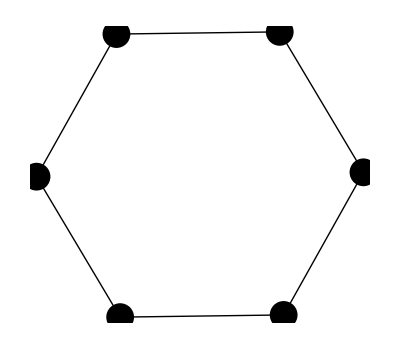

2

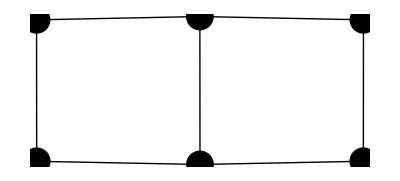

3

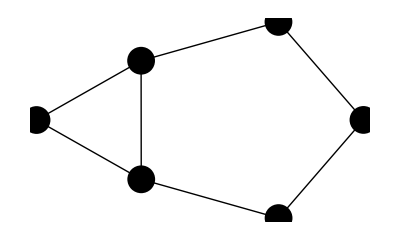

4

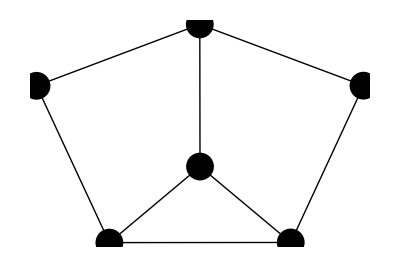

5

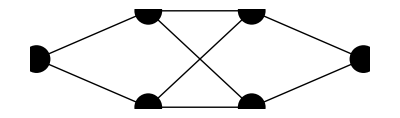

6

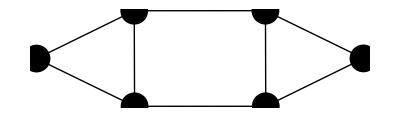

7

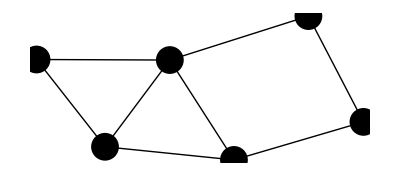

8

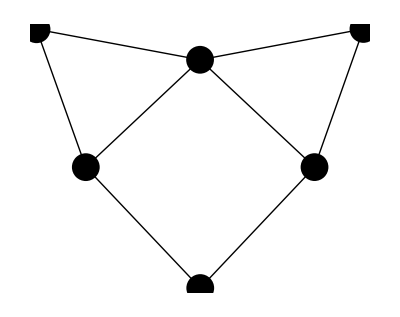

9

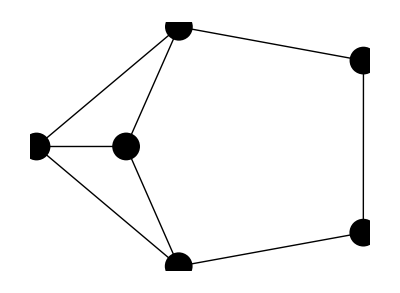

10

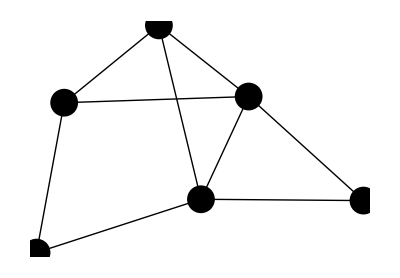

11

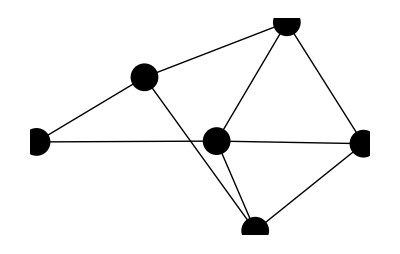

12

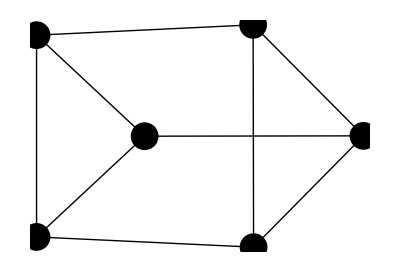

13

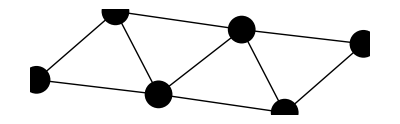

14

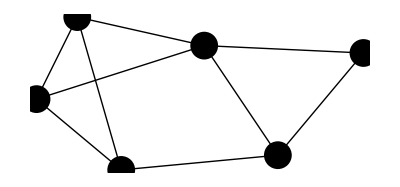

15

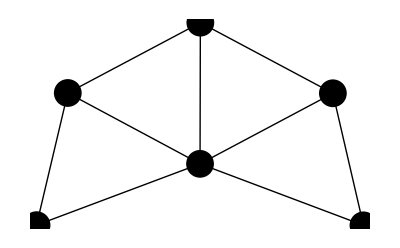

16

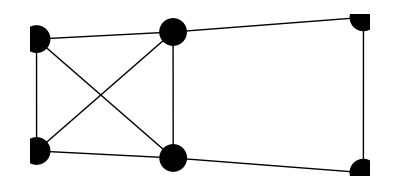

17

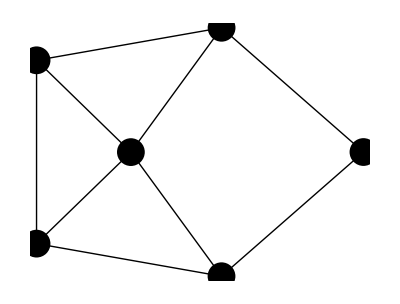

18

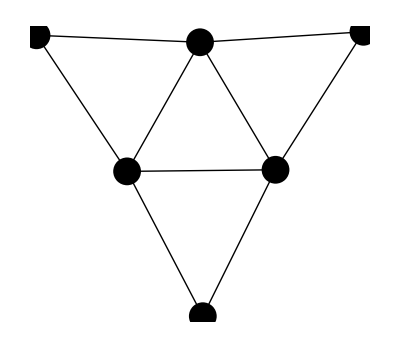

19

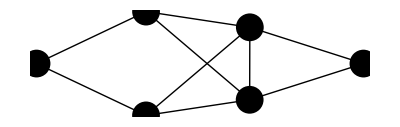

20

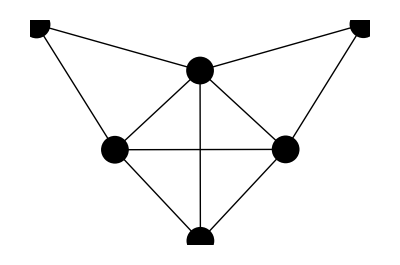

21

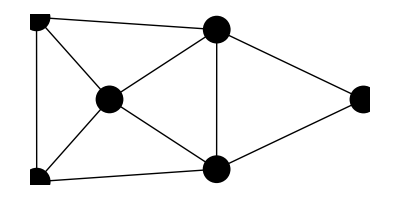

22

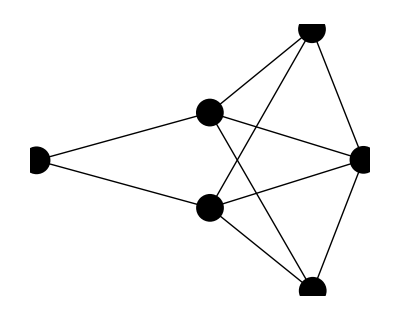

23

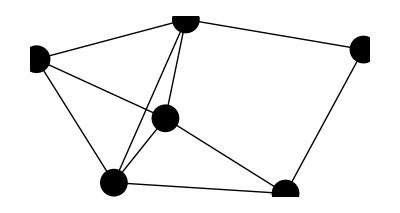

24

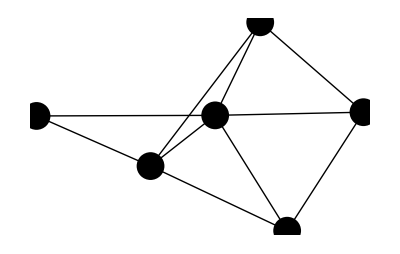

25

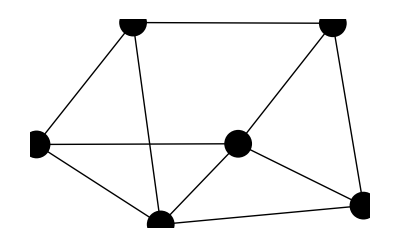

26

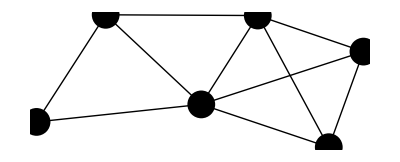

27

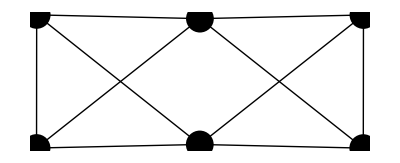

28

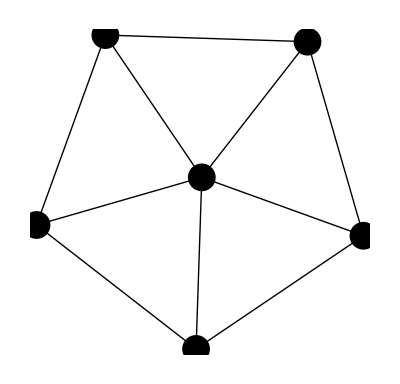

29

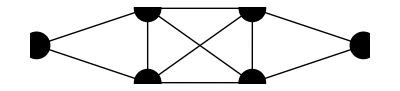

30

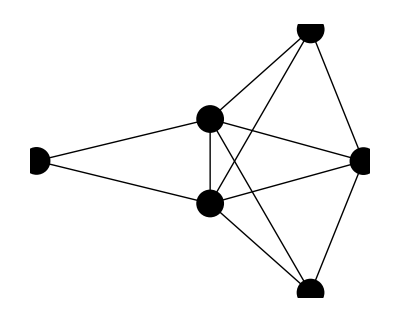

31

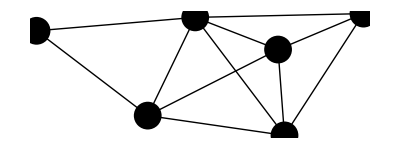

32

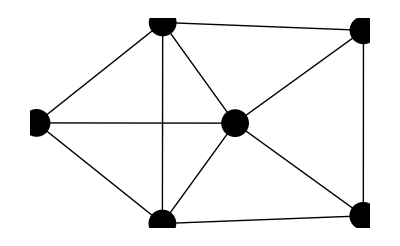

33

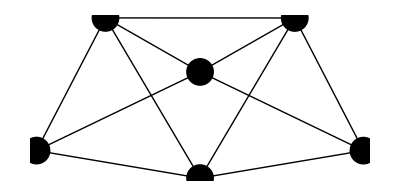

34

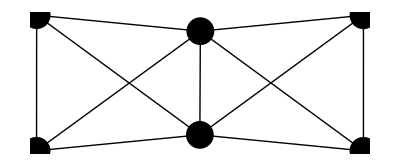

35

-Graphics-

36

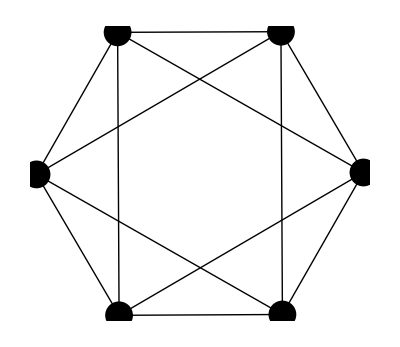

```mathematica
Do[
Print[i];
Print[GraphPlot[listaplanos[[i]],PlotStyle->{Black,PointSize[.05]}]]
,{i,Length[listaplanos]}]
```

### 2.1. EFICACIA

#### Ejemplo 8.20.

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

```mathematica
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
```

```mathematica
<<Combinatorica`;
```

```mathematica
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
```

```mathematica
HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{i,j,k},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

```mathematica
matrizadyacencia=Table[If[i==j,0,1],{i,10},{j,10}];
```

```mathematica
PLANO[matrizadyacencia]
```

33 14118

33 13949

$Aborted

#### Función 8.16. CDNECESARIAPLANO[]

```mathematica
<<"Combinatorica`";
```

```mathematica
IND2[W1_,matrizadyacencia_]:=Module[{n,i,j},
n=Length[W1];
matrizadyacencia2=Table[0,{i,n},{j,n}];
Do[Do[
matrizadyacencia2[[i,j]]=matrizadyacencia[[W1[[i]],W1[[j]]]];
,{i,n}];
,{j,n}];
matrizadyacencia2
];
```

```mathematica
CDNECESARIAPLANO[matrizadyacencia_]:=Module[{Subconjuntos,i,,cont1,matrizadyacenciaK5},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
Print["Comprobamos si puede ser plano"];
Print["Comprobamos si K_(3, 3) está contenido"];
plano=True;
Subconjuntos=KSubsets[Table[i,{i,Dimensions[Nueva][[1]]}],6];
Do[If[K33[Subconjuntos[[cont1]],Nueva],plano=False;Print["Está contenido"];Break[];];,{cont1,Length[Subconjuntos]}];
If[plano,
Print["No está contenido"];
Print["Comprobamos si K_5 está contenido"];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
Subconjuntos=KSubsets[Table[i,{i,Dimensions[Nueva][[1]]}],5];
Do[If[IND2[Subconjuntos[[cont1]],Nueva]==matrizadyacenciaK5,plano=False;Print["Está contenido"];Break[];];,{cont1,Length[Subconjuntos]}];];
If[plano,Print["No está contenido"]];
plano
]
```

#### Ejemplo 8.21.

```mathematica
matrizadyacencia=Table[If[i==j,0,1],{i,10},{j,10}];
```

```mathematica
<<Combinatorica`;
```

```mathematica
IND2[W1_,matrizadyacencia_]:=Module[{n,i,j},
n=Length[W1];
matrizadyacencia2=Table[0,{i,n},{j,n}];
Do[Do[
matrizadyacencia2[[i,j]]=matrizadyacencia[[W1[[i]],W1[[j]]]];
,{i,n}];
,{j,n}];
matrizadyacencia2
];
```

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

```mathematica
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
```

```mathematica
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
```

```mathematica
CDNECESARIAPLANO[matrizadyacencia_]:=Module[{Subconjuntos,i,,cont1,matrizadyacenciaK5},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
Print["Comprobamos si puede ser plano"];
Print["Comprobamos si K_(3, 3) está contenido"];
plano=True;
Subconjuntos=KSubsets[Table[i,{i,Dimensions[Nueva][[1]]}],6];
Do[If[K33[Subconjuntos[[cont1]],Nueva],plano=False;Print["Está contenido"];Break[];];,{cont1,Length[Subconjuntos]}];
If[plano,
Print["No está contenido"];
Print["Comprobamos si K_5 está contenido"];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
Subconjuntos=KSubsets[Table[i,{i,Dimensions[Nueva][[1]]}],5];
Do[If[IND2[Subconjuntos[[cont1]],Nueva]==matrizadyacenciaK5,plano=False;Print["Está contenido"];Break[];];,{cont1,Length[Subconjuntos]}];];
If[plano,Print["No está contenido"]];
plano
]
```

```mathematica
CDNECESARIAPLANO[matrizadyacencia]
```

Comprobamos si puede ser plano

Comprobamos si K_(3, 3) está contenido

Está contenido

False

#### Ejemplo 8.22.

```mathematica
matrizadyacencia={{0,1,1,0,0,1,0,0,0,0},{1,0,0,0,1,0,0,1,0,0},{1,0,0,1,0,0,1,0,0,0},{0,0,1,0,1,0,0,0,1,0},{0,1,0,1,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,1,1},{0,0,1,0,0,0,0,1,0,1},{0,1,0,0,0,0,1,0,1,0},{0,0,0,1,0,1,0,1,0,0},{0,0,0,0,1,1,1,0,0,0}};
```

```mathematica
<<Combinatorica`;
```

```mathematica
IND2[W1_,matrizadyacencia_]:=Module[{n,i,j},
n=Length[W1];
matrizadyacencia2=Table[0,{i,n},{j,n}];
Do[Do[
matrizadyacencia2[[i,j]]=matrizadyacencia[[W1[[i]],W1[[j]]]];
,{i,n}];
,{j,n}];
matrizadyacencia2
];
```

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

```mathematica
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
```

```mathematica
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
```

```mathematica
CDNECESARIAPLANO[matrizadyacencia_]:=Module[{Subconjuntos,i,,cont1,matrizadyacenciaK5},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
Print["Comprobamos si puede ser plano"];
Print["Comprobamos si K_(3, 3) está contenido"];
plano=True;
Subconjuntos=KSubsets[Table[i,{i,Dimensions[Nueva][[1]]}],6];
Do[If[K33[Subconjuntos[[cont1]],Nueva],plano=False;Print["Está contenido"];Break[];];,{cont1,Length[Subconjuntos]}];
If[plano,
Print["No está contenido"];
Print["Comprobamos si K_5 está contenido"];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
Subconjuntos=KSubsets[Table[i,{i,Dimensions[Nueva][[1]]}],5];
Do[If[IND2[Subconjuntos[[cont1]],Nueva]==matrizadyacenciaK5,plano=False;Print["Está contenido"];Break[];];,{cont1,Length[Subconjuntos]}];];
If[plano,Print["No está contenido"]];
plano
]
```

```mathematica
CDNECESARIAPLANO[matrizadyacencia]
```

Comprobamos si puede ser plano

Comprobamos si K_(3, 3) está contenido

No está contenido

Comprobamos si K_5 está contenido

No está contenido

True

```mathematica
HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

```mathematica
PLANO[matrizadyacencia]
```

False

```mathematica
subgrafo
```

{1→2,1→3,3→4,2→5,4→5,1→6,3→7,2→8,7→8,4→9,6→9,8→9,5→10}

```mathematica
matrizadyacencia={{0,1,1,0,0,1,0,0,0,0},{1,0,0,0,1,0,0,1,0,0},{1,0,0,1,0,0,1,0,0,0},{0,0,1,0,1,0,0,0,1,0},{0,1,0,1,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,1,1},{0,0,1,0,0,0,0,1,0,1},{0,1,0,0,0,0,1,0,1,0},{0,0,0,1,0,1,0,1,0,0},{0,0,0,0,1,1,1,0,0,0}};
```

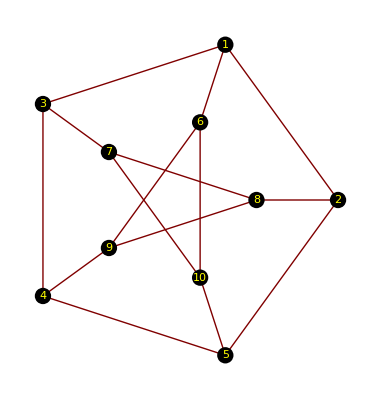

```mathematica
coordenadas=Table[{0,0},{i,10}];
coordenadas⟦1⟧={Cos[(2 π)/5] 2,Sin[(2 π)/5] 2};
coordenadas⟦3⟧={Cos[(2 2 π)/5] 2,Sin[(2 2 π)/5] 2};
coordenadas⟦4⟧={Cos[(3 2 π)/5] 2,Sin[(3 2 π)/5] 2};
coordenadas⟦5⟧={Cos[(4 2 π)/5] 2,Sin[(4 2 π)/5] 2};
coordenadas⟦2⟧={Cos[2 π] 2,Sin[2 π] 2};
coordenadas⟦6⟧={Cos[(2 π)/5],Sin[(2 π)/5]};
coordenadas⟦7⟧={Cos[(2 2 π)/5],Sin[(2 2 π)/5]};
coordenadas⟦9⟧={Cos[(3 2 π)/5],Sin[(3 2 π)/5]};
coordenadas⟦10⟧={Cos[(4 2 π)/5],Sin[(4 2 π)/5]};
coordenadas⟦8⟧={Cos[2 π],Sin[2 π]};
GraphPlot[matrizadyacencia,VertexRenderingFunction->({Black,Disk[#,.1],Yellow,Text[#2,#1]}&),VertexCoordinateRules->coordenadas]
```

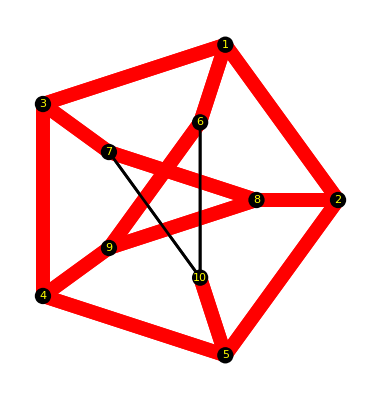

```mathematica
A=matrizadyacencia;
W=Table[i,{i,Dimensions[A]⟦1⟧}];
F={};
Do[Do[If[A⟦i,j⟧==1,AppendTo[F,i->j]];,{i,j}];,{j,Dimensions[A]⟦1⟧}];
subg=Table[If[{subgrafo⟦i⟧}∩F=={},subgrafo⟦i⟧⟦2⟧->subgrafo⟦i⟧⟦1⟧,subgrafo⟦i⟧⟦1⟧->subgrafo⟦i⟧⟦2⟧],{i,Length[subgrafo]}];
Do[If[subg∩{F⟦CONTADORi⟧}=={},colores[{F⟦CONTADORi⟧⟦1⟧,F⟦CONTADORi⟧⟦2⟧}]=Black;colores[{F⟦CONTADORi⟧⟦2⟧,F⟦CONTADORi⟧⟦1⟧}]=Black;grosor[{F⟦CONTADORi⟧⟦1⟧,F⟦CONTADORi⟧⟦2⟧}]=0.005;grosor[{F⟦CONTADORi⟧⟦2⟧,F⟦CONTADORi⟧⟦1⟧}]=0.005;,colores[{F⟦CONTADORi⟧⟦1⟧,F⟦CONTADORi⟧⟦2⟧}]=Red;colores[{F⟦CONTADORi⟧⟦2⟧,F⟦CONTADORi⟧⟦1⟧}]=Red;grosor[{F⟦CONTADORi⟧⟦1⟧,F⟦CONTADORi⟧⟦2⟧}]=0.025;grosor[{F⟦CONTADORi⟧⟦2⟧,F⟦CONTADORi⟧⟦1⟧}]=0.025;];,{CONTADORi,Length[F]}];
GraphPlot[A,VertexRenderingFunction->({Black,Disk[#,.1],Yellow,Text[#2,#1]}&),VertexCoordinateRules->coordenadas,EdgeRenderingFunction->({colores[{#2[[1]],#2[[2]]}],Thickness[grosor[{#2[[1]],#2[[2]]}]],Line[#1]}&)]
```

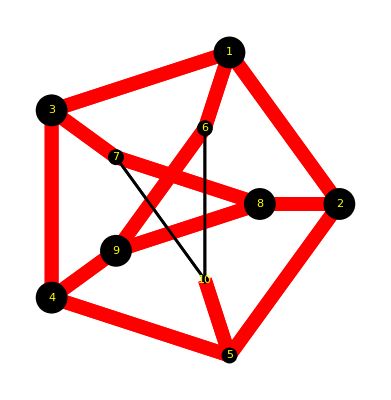

```mathematica
disco={0.2,0.2,0.2,0.2,0.1,0.1,0.1,0.2,0.2,0.05};
GraphPlot[A,VertexRenderingFunction->({Black,Disk[#,disco[[#2]]],Yellow,Text[#2,#1]}&),VertexCoordinateRules->coordenadas,EdgeRenderingFunction->({colores[{#2[[1]],#2[[2]]}],Thickness[grosor[{#2[[1]],#2[[2]]}]],Line[#1]}&)]
```

```mathematica
coordenadas[[9]]={1,0};
coordenadas[[3]]={2,0};
coordenadas[[2]]={3,0};
coordenadas[[1]]={1,2};
coordenadas[[8]]={2,2};
coordenadas[[4]]={3,2};
coordenadas[[6]]={1,1};
coordenadas[[7]]={2,.8};
coordenadas[[5]]={3,1};
coordenadas[[10]]={4,2};
```

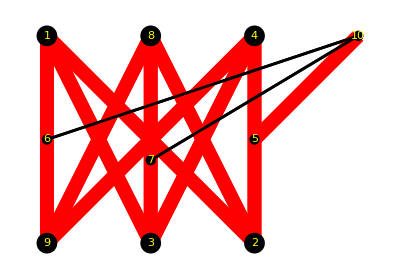

```mathematica
disco={0.1,0.1,0.1,0.1,0.05,0.05,0.05,0.1,0.1,0.05};
GraphPlot[A,VertexRenderingFunction->({Black,Disk[#,disco[[#2]]],Yellow,Text[#2,#1]}&),VertexCoordinateRules->coordenadas,EdgeRenderingFunction->({colores[{#2[[1]],#2[[2]]}],Thickness[grosor[{#2[[1]],#2[[2]]}]],Line[#1]}&)]
```

#### Ejemplo 8.23.

```mathematica
matrizadyacencia={{0,1,0,0,1,1,0,1,0,0,1,0},{1,0,1,0,0,1,1,0,0,0,0,0},
   {0,1,0,1,0,0,1,0,0,1,0,0},{0,0,1,0,1,0,0,0,1,1,0,0},{1,0,0,1,0,0,0,1,1,0,1,0},
   {1,1,0,0,0,0,0,1,0,0,0,1},{0,1,1,0,0,0,0,0,0,1,0,1},{1,0,0,0,1,1,0,0,1,0,0,0},
   {0,0,0,1,1,0,0,1,0,1,0,0},{0,0,1,1,0,0,1,0,1,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},
   {0,0,0,0,0,1,1,0,0,0,0,0}};
```

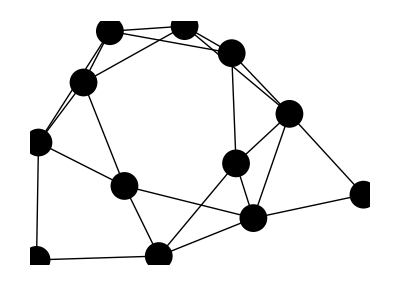

```mathematica
GraphPlot[matrizadyacencia,PlotStyle->{Black,PointSize[.05]}]
```

```mathematica
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
```

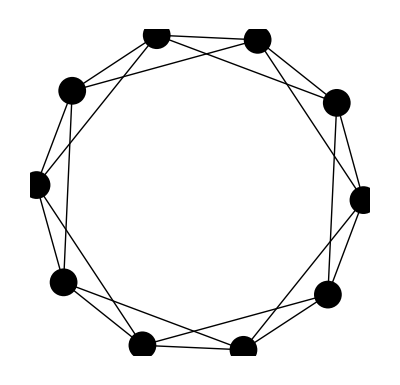

```mathematica
GraphPlot[Nueva,PlotStyle->{Black,PointSize[.05]}]
```

```mathematica
<<Combinatorica`;
```

```mathematica
IND2[W1_,matrizadyacencia_]:=Module[{n,i,j},
n=Length[W1];
matrizadyacencia2=Table[0,{i,n},{j,n}];
Do[Do[
matrizadyacencia2[[i,j]]=matrizadyacencia[[W1[[i]],W1[[j]]]];
,{i,n}];
,{j,n}];
matrizadyacencia2
];
```

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

```mathematica
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
```

```mathematica
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
```

```mathematica
CDNECESARIAPLANO[matrizadyacencia_]:=Module[{Subconjuntos,i,,cont1,matrizadyacenciaK5},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
Print["Comprobamos si puede ser plano"];
Print["Comprobamos si K_(3, 3) está contenido"];
plano=True;
Subconjuntos=KSubsets[Table[i,{i,Dimensions[Nueva][[1]]}],6];
Do[If[K33[Subconjuntos[[cont1]],Nueva],plano=False;Print["Está contenido"];Break[];];,{cont1,Length[Subconjuntos]}];
If[plano,
Print["No está contenido"];
Print["Comprobamos si K_5 está contenido"];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
Subconjuntos=KSubsets[Table[i,{i,Dimensions[Nueva][[1]]}],5];
Do[If[IND2[Subconjuntos[[cont1]],Nueva]==matrizadyacenciaK5,plano=False;Print["Está contenido"];Break[];];,{cont1,Length[Subconjuntos]}];];
If[plano,Print["No está contenido"]];
plano
]
```

```mathematica
CDNECESARIAPLANO[matrizadyacencia]
```

Comprobamos si puede ser plano

Comprobamos si K_(3, 3) está contenido

No está contenido

Comprobamos si K_5 está contenido

No está contenido

True

```mathematica
HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

```mathematica
PLANO[matrizadyacencia]
```

7 4473

7 3583

7 2695

7 1824

7 963

7 109

6 15205

6 14847

6 14470

6 14101

6 13739

6 13380

6 13023

6 12655

6 12302

6 11951

6 11599

6 11239

6 10874

6 10520

6 10153

6 9792

6 9434

6 9078

6 8714

6 8354

6 7986

6 7627

6 7274

6 6919

6 6552

6 6209

6 5851

6 5488

6 5132

6 4775

6 4414

6 4054

6 3689

6 3317

6 2960

6 2605

6 2249

6 1893

6 1537

6 1178

6 820

6 458

6 105

5 38648

5 38476

5 38306

5 38135

5 37965

5 37791

5 37617

5 37445

5 37274

5 37101

5 36929

5 36759

5 36588

5 36417

5 36246

5 36075

5 35904

5 35732

5 35562

5 35390

5 35220

5 35048

5 34876

5 34704

5 34532

5 34359

5 34187

5 34013

5 33842

5 33670

5 33499

5 33330

5 33160

5 32991

5 32821

5 32649

5 32477

5 32304

5 32132

5 31962

5 31792

5 31623

5 31453

5 31284

5 31113

5 30943

5 30770

5 30599

5 30430

5 30261

5 30092

5 29922

5 29755

5 29585

5 29416

5 29245

5 29072

5 28904

5 28735

5 28566

5 28394

5 28224

5 28054

5 27881

5 27711

5 27541

5 27370

5 27198

5 27028

5 26857

5 26687

5 26515

5 26345

5 26176

5 26006

5 25836

5 25666

5 25495

5 25326

5 25155

5 24985

5 24816

5 24645

5 24475

5 24308

5 24139

5 23971

5 23802

5 23630

5 23459

5 23286

5 23114

5 22943

5 22775

5 22605

5 22435

5 22265

5 22095

5 21925

5 21757

5 21586

5 21418

5 21249

5 21076

5 20907

5 20738

5 20571

5 20403

5 20236

5 20065

5 19894

5 19724

5 19555

5 19385

5 19217

5 19049

5 18878

5 18709

5 18540

5 18368

5 18198

5 18027

5 17854

5 17682

5 17512

5 17342

5 17173

5 17001

5 16831

5 16663

5 16497

5 16328

5 16157

5 15990

5 15821

5 15651

5 15481

5 15311

5 15143

5 14976

5 14805

5 14636

5 14466

5 14298

5 14130

5 13962

5 13792

5 13619

5 13451

5 13285

5 13116

5 12948

5 12777

5 12607

5 12437

5 12267

5 12098

5 11926

5 11757

5 11586

5 11416

5 11246

5 11074

5 10902

5 10730

5 10560

5 10390

5 10223

5 10055

5 9882

5 9712

5 9544

5 9376

5 9205

5 9037

5 8870

5 8702

5 8533

5 8363

5 8192

5 8024

5 7855

5 7687

5 7517

5 7348

5 7180

5 7011

5 6843

5 6672

5 6503

5 6335

5 6166

5 5995

5 5824

5 5651

5 5480

5 5310

5 5140

5 4970

5 4800

5 4632

5 4462

5 4294

5 4125

5 3956

5 3785

5 3617

5 3448

5 3280

5 3110

5 2941

5 2772

5 2602

5 2433

5 2262

5 2090

5 1923

5 1755

5 1586

5 1418

5 1250

5 1083

5 916

5 746

5 578

5 409

5 239

5 71

4 77471

4 77373

4 77276

4 77179

4 77082

4 76985

4 76888

4 76792

4 76696

4 76598

4 76499

4 76404

4 76308

4 76211

4 76114

4 76017

4 75920

4 75822

4 75726

4 75630

4 75531

4 75435

4 75339

4 75241

4 75145

4 75049

4 74954

4 74856

4 74759

4 74663

4 74567

4 74470

4 74373

4 74276

4 74181

4 74082

4 73986

4 73889

4 73792

4 73696

4 73599

4 73502

4 73405

4 73308

4 73210

4 73113

4 73016

4 72919

4 72821

4 72724

4 72628

4 72531

4 72434

4 72336

4 72239

4 72141

4 72044

4 71947

4 71850

4 71754

4 71656

4 71558

4 71460

4 71363

4 71266

4 71169

4 71071

4 70975

4 70878

4 70780

4 70683

4 70588

4 70491

4 70395

4 70298

4 70202

4 70106

4 70009

4 69911

4 69815

4 69719

4 69622

4 69524

4 69427

4 69330

4 69234

4 69137

4 69042

4 68945

4 68849

4 68753

4 68657

4 68560

4 68463

4 68366

4 68270

4 68174

4 68077

4 67980

4 67884

4 67786

4 67690

4 67593

4 67497

4 67401

4 67306

4 67209

4 67113

4 67016

4 66920

4 66823

4 66726

4 66629

4 66532

4 66436

4 66341

4 66245

4 66148

4 66051

4 65952

4 65856

4 65760

4 65663

4 65567

4 65470

4 65374

4 65277

4 65180

4 65083

4 64984

4 64887

4 64789

4 64691

4 64595

4 64499

4 64401

4 64303

4 64206

4 64107

4 64011

4 63914

4 63816

4 63720

4 63624

4 63527

4 63431

4 63334

4 63239

4 63145

4 63050

4 62956

4 62860

4 62763

4 62668

4 62571

4 62475

4 62380

4 62284

4 62187

4 62091

4 61996

4 61900

4 61808

4 61714

4 61622

4 61526

4 61431

4 61337

4 61246

4 61152

4 61059

4 60966

4 60872

4 60778

4 60685

4 60593

4 60501

4 60406

4 60312

4 60219

4 60126

4 60032

4 59936

4 59840

4 59744

4 59647

4 59555

4 59462

4 59365

4 59269

4 59173

4 59076

4 58979

4 58884

4 58788

4 58693

4 58597

4 58502

4 58405

4 58309

4 58213

4 58118

4 58022

4 57925

4 57828

4 57730

4 57633

4 57536

4 57442

4 57348

4 57253

4 57157

4 57078

4 56996

4 56899

4 56804

4 56709

4 56612

4 56517

4 56419

4 56322

4 56226

4 56128

4 56033

4 55937

4 55840

4 55745

4 55650

4 55555

4 55457

4 55362

4 55267

4 55171

4 55075

4 54979

4 54884

4 54789

4 54695

4 54598

4 54502

4 54407

4 54312

4 54216

4 54121

4 54025

4 53930

4 53834

4 53737

4 53641

4 53544

4 53449

4 53354

4 53259

4 53165

4 53069

4 52973

4 52875

4 52779

4 52683

4 52588

4 52492

4 52396

4 52301

4 52204

4 52108

4 52010

4 51915

4 51819

4 51724

4 51629

4 51535

4 51438

4 51342

4 51246

4 51150

4 51054

4 50958

4 50862

4 50765

4 50669

4 50573

4 50477

4 50381

4 50287

4 50191

4 50096

4 49999

4 49904

4 49808

4 49713

4 49616

4 49520

4 49422

4 49328

4 49231

4 49137

4 49041

4 48946

4 48849

4 48752

4 48658

4 48565

4 48470

4 48376

4 48280

4 48186

4 48090

4 47995

4 47897

4 47802

4 47707

4 47611

4 47516

4 47420

4 47325

4 47230

4 47132

4 47036

4 46939

4 46845

4 46749

4 46655

4 46560

4 46465

4 46369

4 46274

4 46177

4 46081

4 45984

4 45888

4 45793

4 45697

4 45601

4 45506

4 45410

4 45316

4 45220

4 45125

4 45029

4 44932

4 44837

4 44740

4 44643

4 44548

4 44452

4 44356

4 44261

4 44166

4 44072

4 43975

4 43878

4 43782

4 43689

4 43593

4 43498

4 43402

4 43307

4 43213

4 43118

4 43023

4 42926

4 42830

4 42735

4 42641

4 42546

4 42452

4 42357

4 42261

4 42165

4 42069

4 41974

4 41880

4 41786

4 41690

4 41593

4 41498

4 41403

4 41307

4 41211

4 41114

4 41017

4 40922

4 40828

4 40733

4 40636

4 40541

4 40447

4 40351

4 40257

4 40162

4 40066

4 39969

4 39873

4 39778

4 39683

4 39587

4 39492

4 39395

4 39300

4 39203

4 39108

4 39012

4 38916

4 38820

4 38725

4 38628

4 38534

4 38438

4 38345

4 38250

4 38153

4 38057

4 37962

4 37867

4 37770

4 37673

4 37577

4 37481

4 37387

4 37292

4 37197

4 37101

4 37004

4 36909

4 36813

4 36716

4 36619

4 36523

4 36428

4 36332

4 36237

4 36142

4 36045

4 35949

4 35852

4 35756

4 35660

4 35564

4 35469

4 35373

4 35278

4 35181

4 35085

4 34989

4 34893

4 34795

4 34700

4 34605

4 34511

4 34416

4 34319

4 34223

4 34127

4 34033

4 33936

4 33841

4 33746

4 33649

4 33551

4 33454

4 33359

4 33263

4 33166

4 33071

4 32974

4 32878

4 32781

4 32684

4 32586

4 32490

4 32396

4 32301

4 32204

4 32109

4 32012

4 31916

4 31818

4 31721

4 31625

4 31529

4 31435

4 31340

4 31244

4 31148

4 31052

4 30956

4 30859

4 30762

4 30666

4 30571

4 30476

4 30378

4 30280

4 30184

4 30088

4 29993

4 29896

4 29801

4 29705

4 29608

4 29512

4 29416

4 29319

4 29223

4 29127

4 29030

4 28935

4 28838

4 28741

4 28646

4 28550

4 28453

4 28357

4 28261

4 28164

4 28068

4 27973

4 27878

4 27781

4 27685

4 27589

4 27492

4 27396

4 27300

4 27204

4 27109

4 27012

4 26915

4 26820

4 26725

4 26627

4 26531

4 26435

4 26338

4 26242

4 26146

4 26050

4 25958

4 25863

4 25766

4 25670

4 25576

4 25478

4 25382

4 25286

4 25190

4 25095

4 24999

4 24904

4 24810

4 24715

4 24620

4 24523

4 24426

4 24329

4 24232

4 24136

4 24039

4 23943

4 23847

4 23751

4 23654

4 23558

4 23462

4 23366

4 23268

4 23173

4 23076

4 22979

4 22882

4 22786

4 22691

4 22592

4 22496

4 22397

4 22299

4 22204

4 22107

4 22011

4 21915

4 21819

4 21723

4 21628

4 21531

4 21434

4 21337

4 21241

4 21145

4 21051

4 20955

4 20858

4 20763

4 20667

4 20569

4 20473

4 20376

4 20279

4 20182

4 20085

4 19989

4 19893

4 19797

4 19702

4 19604

4 19509

4 19413

4 19316

4 19220

4 19123

4 19025

4 18930

4 18832

4 18735

4 18638

4 18542

4 18446

4 18351

4 18256

4 18162

4 18066

4 17971

4 17877

4 17782

4 17688

4 17594

4 17497

4 17400

4 17305

4 17209

4 17113

4 17017

4 16919

4 16822

4 16725

4 16628

4 16530

4 16434

4 16338

4 16241

4 16144

4 16049

4 15953

4 15858

4 15760

4 15664

4 15569

4 15472

4 15376

4 15281

4 15186

4 15091

4 14994

4 14898

4 14802

4 14707

4 14611

4 14514

4 14418

4 14322

4 14225

4 14126

4 14027

4 13928

4 13832

4 13738

4 13641

4 13544

4 13448

4 13352

4 13256

4 13161

4 13065

4 12968

4 12873

4 12777

4 12680

4 12585

4 12487

4 12393

4 12297

4 12202

4 12106

4 12011

4 11916

4 11820

4 11724

4 11629

4 11533

4 11439

4 11342

4 11247

4 11153

4 11058

4 10964

4 10868

4 10771

4 10676

4 10582

4 10487

4 10393

4 10297

4 10200

4 10105

4 10011

4 9916

4 9821

4 9725

4 9631

4 9537

4 9442

4 9346

4 9252

4 9157

4 9061

4 8965

4 8870

4 8777

4 8682

4 8586

4 8491

4 8394

4 8299

4 8204

4 8109

4 8015

4 7919

4 7825

4 7727

4 7632

4 7537

4 7441

4 7345

4 7248

4 7153

4 7055

4 6958

4 6863

4 6767

4 6671

4 6576

4 6480

4 6385

4 6288

4 6191

4 6094

4 5999

4 5904

4 5808

4 5712

4 5615

4 5519

4 5423

4 5327

4 5230

4 5134

4 5038

4 4940

4 4843

4 4746

4 4650

4 4552

4 4457

4 4359

4 4263

4 4166

4 4071

4 3973

4 3878

4 3783

4 3686

4 3589

4 3494

4 3397

4 3300

4 3203

4 3106

4 3009

4 2913

4 2816

4 2720

4 2624

4 2527

4 2431

4 2333

4 2237

4 2141

4 2044

4 1948

4 1851

4 1755

4 1659

4 1563

4 1466

4 1369

4 1275

4 1179

4 1082

4 985

4 887

4 790

4 694

4 596

4 499

4 404

4 308

4 211

4 114

4 18

3 125925

3 125859

3 125793

3 125727

3 125661

3 125595

3 125529

3 125464

3 125398

3 125331

3 125264

3 125198

3 125133

3 125067

3 125000

3 124934

3 124868

3 124802

3 124737

3 124671

3 124605

3 124538

3 124472

3 124405

3 124339

3 124273

3 124207

3 124141

3 124075

3 124010

3 123944

3 123878

3 123812

3 123746

3 123680

3 123614

3 123548

3 123482

3 123416

3 123350

3 123284

3 123219

3 123153

3 123087

3 123021

3 122956

3 122889

3 122823

3 122758

3 122692

3 122626

3 122560

3 122493

3 122427

3 122361

3 122295

3 122230

3 122164

3 122099

3 122034

3 121968

3 121903

3 121837

3 121770

3 121704

3 121638

3 121572

3 121505

3 121439

3 121373

3 121308

3 121243

3 121176

3 121110

3 121044

3 120979

3 120913

3 120861

3 120796

3 120730

3 120664

3 120598

3 120532

3 120466

3 120400

3 120334

3 120267

3 120201

3 120135

3 120069

3 120003

3 119936

3 119870

3 119803

3 119737

3 119671

3 119605

3 119539

3 119473

3 119407

3 119341

3 119276

3 119211

3 119146

3 119080

3 119014

3 118948

3 118883

3 118817

3 118751

3 118684

3 118618

3 118552

3 118486

3 118421

3 118355

3 118289

3 118223

3 118157

3 118091

3 118025

3 117959

3 117893

3 117827

3 117760

3 117694

3 117627

3 117561

3 117495

3 117429

3 117363

3 117297

3 117232

3 117165

3 117100

3 117034

3 116968

3 116902

3 116836

3 116771

3 116706

3 116640

3 116574

3 116508

3 116443

3 116377

3 116311

3 116244

3 116178

3 116112

3 116046

3 115979

3 115913

3 115847

3 115782

3 115716

3 115650

3 115584

3 115519

3 115452

3 115385

3 115319

3 115253

3 115187

3 115122

3 115056

3 114991

3 114925

3 114859

3 114793

3 114727

3 114662

3 114597

3 114531

3 114465

3 114399

3 114334

3 114267

3 114201

3 114134

3 114068

3 114002

3 113935

3 113868

3 113801

3 113735

3 113669

3 113602

3 113536

3 113470

3 113404

3 113338

3 113273

3 113207

3 113141

3 113075

3 113008

3 112942

3 112876

3 112809

3 112742

3 112676

3 112610

3 112544

3 112478

3 112413

3 112347

3 112281

3 112215

3 112149

3 112082

3 112016

3 111950

3 111884

3 111817

3 111751

3 111685

3 111620

3 111553

3 111488

3 111423

3 111357

3 111291

3 111226

3 111160

3 111094

3 111028

3 110961

3 110896

3 110830

3 110765

3 110699

3 110633

3 110567

3 110500

3 110434

3 110369

3 110304

3 110238

3 110171

3 110105

3 110039

3 109973

3 109907

3 109842

3 109777

3 109711

3 109645

3 109580

3 109513

3 109447

3 109381

3 109314

3 109248

3 109182

3 109116

3 109050

3 108985

3 108919

3 108853

3 108787

3 108721

3 108656

3 108590

3 108523

3 108458

3 108392

3 108327

3 108262

3 108196

3 108131

3 108065

3 107999

3 107933

3 107867

3 107801

3 107736

3 107670

3 107604

3 107538

3 107472

3 107406

3 107340

3 107274

3 107209

3 107143

3 107078

3 107013

3 106947

3 106881

3 106815

3 106750

3 106685

3 106619

3 106553

3 106487

3 106421

3 106355

3 106289

3 106221

3 106155

3 106089

3 106023

3 105958

3 105893

3 105827

3 105762

3 105696

3 105630

3 105565

3 105499

3 105433

3 105367

3 105302

3 105236

3 105170

3 105104

3 105038

3 104971

3 104906

3 104841

3 104776

3 104710

3 104643

3 104578

3 104513

3 104447

3 104382

3 104316

3 104250

3 104184

3 104118

3 104053

3 103987

3 103920

3 103854

3 103789

3 103723

3 103656

3 103590

3 103524

3 103459

3 103394

3 103330

3 103264

3 103198

3 103132

3 103066

3 103001

3 102935

3 102870

3 102803

3 102737

3 102671

3 102604

3 102538

3 102472

3 102406

3 102340

3 102274

3 102208

3 102142

3 102076

3 102010

3 101944

3 101879

3 101813

3 101747

3 101681

3 101614

3 101548

3 101482

3 101416

3 101350

3 101284

3 101218

3 101152

3 101086

3 101021

3 100955

3 100889

3 100823

3 100757

3 100692

3 100625

3 100560

3 100495

3 100430

3 100364

3 100298

3 100232

3 100166

3 100100

3 100035

3 99969

3 99903

3 99837

3 99771

3 99705

3 99640

3 99575

3 99509

3 99444

3 99378

3 99313

3 99247

3 99181

3 99115

3 99049

3 98983

3 98918

3 98852

3 98786

3 98721

3 98656

3 98590

3 98525

3 98459

3 98393

3 98327

3 98261

3 98195

3 98129

3 98064

3 97998

3 97932

3 97867

3 97800

3 97734

3 97668

3 97602

3 97536

3 97470

3 97405

3 97339

3 97274

3 97209

3 97143

3 97077

3 97011

3 96946

3 96880

3 96814

3 96749

3 96683

3 96618

3 96552

3 96487

3 96422

3 96356

3 96290

3 96224

3 96159

3 96093

3 96027

3 95962

3 95896

3 95830

3 95765

3 95699

3 95635

3 95570

3 95504

3 95438

3 95372

3 95307

3 95241

3 95174

3 95108

3 95042

3 94975

3 94909

3 94843

3 94777

3 94711

3 94646

3 94580

3 94514

3 94448

3 94382

3 94316

3 94250

3 94184

3 94117

3 94051

3 93985

3 93919

3 93854

3 93788

3 93722

3 93657

3 93590

3 93524

3 93457

3 93390

3 93324

3 93259

3 93193

3 93127

3 93062

3 92996

3 92930

3 92863

3 92797

3 92730

3 92665

3 92599

3 92533

3 92467

3 92401

3 92335

3 92269

3 92203

3 92137

3 92071

3 92006

3 91940

3 91875

3 91810

3 91744

3 91678

3 91611

3 91544

3 91478

3 91413

3 91347

3 91281

3 91216

3 91150

3 91084

3 91019

3 90953

3 90887

3 90822

3 90756

3 90690

3 90624

3 90558

3 90492

3 90427

3 90362

3 90296

3 90230

3 90163

3 90096

3 90029

3 89964

3 89899

3 89832

3 89767

3 89701

3 89635

3 89568

3 89503

3 89438

3 89371

3 89306

3 89240

3 89174

3 89108

3 89042

3 88977

3 88910

3 88845

3 88778

3 88712

3 88645

3 88578

3 88512

3 88446

3 88379

3 88313

3 88248

3 88182

3 88116

3 88050

3 87983

3 87918

3 87853

3 87787

3 87721

3 87655

3 87590

3 87524

3 87459

3 87393

3 87327

3 87261

3 87195

3 87129

3 87063

3 86997

3 86931

3 86865

3 86800

3 86734

3 86669

3 86603

3 86537

3 86471

3 86405

3 86340

3 86274

3 86208

3 86143

3 86077

3 86011

3 85947

3 85881

3 85815

3 85749

3 85683

3 85616

3 85550

3 85484

3 85419

3 85353

3 85287

3 85221

3 85155

3 85088

3 85022

3 84955

3 84888

3 84822

3 84757

3 84690

3 84624

3 84558

3 84492

3 84426

3 84360

3 84293

3 84227

3 84161

3 84096

3 84031

3 83965

3 83899

3 83834

3 83769

3 83703

3 83637

3 83571

3 83505

3 83439

3 83373

3 83307

3 83242

3 83177

3 83110

3 83044

3 82978

3 82912

3 82845

3 82780

3 82715

3 82649

3 82584

3 82519

3 82453

3 82387

3 82321

3 82255

3 82189

3 82124

3 82058

3 81992

3 81925

3 81858

3 81792

3 81727

3 81661

3 81595

3 81529

3 81464

3 81398

3 81333

3 81267

3 81201

3 81134

3 81068

3 81002

3 80936

3 80869

3 80803

3 80737

3 80671

3 80606

3 80540

3 80473

3 80407

3 80342

3 80276

3 80210

3 80144

3 80078

3 80011

3 79946

3 79880

3 79815

3 79750

3 79684

3 79619

3 79554

3 79488

3 79422

3 79356

3 79289

3 79222

3 79156

3 79089

3 79023

3 78957

3 78891

3 78824

3 78758

3 78693

3 78627

3 78561

3 78495

3 78429

3 78362

3 78296

3 78231

3 78165

3 78100

3 78034

3 77968

3 77902

3 77836

3 77771

3 77705

3 77639

3 77573

3 77507

3 77442

3 77376

3 77309

3 77243

3 77177

3 77111

3 77045

3 76979

3 76913

3 76847

3 76782

3 76717

3 76650

3 76585

3 76519

3 76454

3 76388

3 76323

3 76257

3 76191

3 76125

3 76059

3 75993

3 75927

3 75861

3 75796

3 75730

3 75663

3 75597

3 75532

3 75466

3 75400

3 75334

3 75268

3 75203

3 75137

3 75072

3 75007

3 74942

3 74877

3 74811

3 74744

3 74678

3 74613

3 74546

3 74480

3 74414

3 74349

3 74283

3 74218

3 74153

3 74087

3 74021

3 73955

3 73888

3 73822

3 73756

3 73690

3 73624

3 73558

3 73492

3 73427

3 73360

3 73294

3 73228

3 73162

3 73096

3 73030

3 72964

3 72899

3 72834

3 72768

3 72702

3 72636

3 72569

3 72503

3 72437

3 72371

3 72304

3 72238

3 72172

3 72106

3 72040

3 71974

3 71908

3 71841

3 71775

3 71708

3 71642

3 71576

3 71510

3 71444

3 71379

3 71313

3 71247

3 71181

3 71115

3 71049

3 70983

3 70917

3 70851

3 70785

3 70719

3 70653

3 70587

3 70520

3 70454

3 70388

3 70322

3 70256

3 70190

3 70123

3 70056

3 69989

3 69924

3 69858

3 69792

3 69726

3 69660

3 69593

3 69527

3 69462

3 69396

3 69330

3 69264

3 69198

3 69132

3 69066

3 69000

3 68934

3 68869

3 68803

3 68738

3 68673

3 68606

3 68540

3 68475

3 68409

3 68343

3 68278

3 68212

3 68146

3 68080

3 68014

3 67948

3 67882

3 67816

3 67750

3 67684

3 67618

3 67553

3 67487

3 67421

3 67355

3 67289

3 67223

3 67157

3 67091

3 67025

3 66959

3 66893

3 66827

3 66761

3 66696

3 66631

3 66565

3 66499

3 66433

3 66367

3 66301

3 66235

3 66169

3 66104

3 66039

3 65973

3 65907

3 65842

3 65776

3 65710

3 65644

3 65579

3 65512

3 65446

3 65380

3 65314

3 65248

3 65182

3 65116

3 65050

3 64984

3 64918

3 64851

3 64785

3 64719

3 64653

3 64587

3 64520

3 64454

3 64388

3 64322

3 64256

3 64191

3 64125

3 64059

3 63993

3 63927

3 63861

3 63795

3 63729

3 63663

3 63597

3 63531

3 63465

3 63399

3 63333

3 63267

3 63201

3 63135

3 63070

3 63003

3 62937

3 62870

3 62804

3 62737

3 62671

3 62605

3 62539

3 62473

3 62407

3 62341

3 62275

3 62209

3 62142

3 62076

3 62009

3 61943

3 61877

3 61811

3 61744

3 61678

3 61612

3 61545

3 61479

3 61413

3 61347

3 61280

3 61213

3 61146

3 61079

3 61013

3 60947

3 60881

3 60815

3 60750

3 60684

3 60618

3 60552

3 60486

3 60419

3 60354

3 60288

3 60221

3 60156

3 60091

3 60024

3 59958

3 59892

3 59825

3 59759

3 59693

3 59627

3 59561

3 59494

3 59428

3 59362

3 59296

3 59230

3 59164

3 59097

3 59030

3 58964

3 58899

3 58833

3 58767

3 58701

3 58636

3 58570

3 58504

3 58438

3 58373

3 58307

3 58241

3 58175

3 58109

3 58043

3 57978

3 57912

3 57846

3 57780

3 57714

3 57647

3 57581

3 57514

3 57448

3 57382

3 57316

3 57250

3 57184

3 57117

3 57050

3 56984

3 56918

3 56853

3 56788

3 56722

3 56656

3 56590

3 56524

3 56458

3 56392

3 56326

3 56261

3 56196

3 56130

3 56064

3 55998

3 55932

3 55866

3 55800

3 55734

3 55668

3 55602

3 55536

3 55470

3 55403

3 55337

3 55272

3 55207

3 55141

3 55075

3 55009

3 54943

3 54877

3 54811

3 54745

3 54679

3 54613

3 54547

3 54481

3 54415

3 54350

3 54284

3 54220

3 54157

3 54093

3 54027

3 53961

3 53896

3 53831

3 53766

3 53701

3 53638

3 53573

3 53508

3 53443

3 53378

3 53312

3 53246

3 53182

3 53118

3 53052

3 52986

3 52921

3 52854

3 52789

3 52724

3 52659

3 52594

3 52529

3 52463

3 52398

3 52333

3 52267

3 52202

3 52137

3 52071

3 52006

3 51941

3 51876

3 51810

3 51744

3 51678

3 51613

3 51547

3 51482

3 51417

3 51356

3 51295

3 51232

3 51167

3 51105

3 51040

3 50975

3 50910

3 50845

3 50780

3 50714

3 50649

3 50586

3 50521

3 50456

3 50391

3 50324

3 50259

3 50194

3 50129

3 50065

3 49999

3 49933

3 49867

3 49801

3 49735

3 49672

3 49606

3 49540

3 49474

3 49408

3 49342

3 49277

3 49211

3 49145

3 49079

3 49014

3 48951

3 48887

3 48823

3 48758

3 48694

3 48630

3 48566

3 48502

3 48436

3 48371

3 48305

3 48239

3 48173

3 48107

3 48041

3 47975

3 47908

3 47842

3 47776

3 47710

3 47644

3 47578

3 47512

3 47446

3 47380

3 47314

3 47248

3 47182

3 47116

3 47050

3 46983

3 46916

3 46850

3 46784

3 46718

3 46652

3 46586

3 46520

3 46454

3 46388

3 46322

3 46257

3 46191

3 46125

3 46060

3 45994

3 45928

3 45862

3 45798

3 45734

3 45669

3 45604

3 45539

3 45476

3 45413

3 45349

3 45286

3 45223

3 45158

3 45095

3 45031

3 44966

3 44902

3 44837

3 44771

3 44705

3 44639

3 44573

3 44507

3 44441

3 44375

3 44309

3 44242

3 44176

3 44110

3 44044

3 43978

3 43911

3 43845

3 43779

3 43713

3 43647

3 43581

3 43515

3 43449

3 43382

3 43316

3 43250

3 43184

3 43118

3 43051

3 42984

3 42918

3 42851

3 42784

3 42717

3 42650

3 42585

3 42519

3 42452

3 42386

3 42320

3 42254

3 42188

3 42122

3 42056

3 41990

3 41924

3 41858

3 41792

3 41726

3 41660

3 41594

3 41528

3 41462

3 41396

3 41330

3 41265

3 41199

3 41133

3 41066

3 41000

3 40934

3 40868

3 40802

3 40736

3 40670

3 40604

3 40538

3 40471

3 40405

3 40339

3 40272

3 40205

3 40139

3 40073

3 40006

3 39940

3 39874

3 39808

3 39741

3 39675

3 39609

3 39544

3 39478

3 39412

3 39346

3 39281

3 39215

3 39148

3 39081

3 39014

3 38947

3 38880

3 38814

3 38747

3 38681

3 38615

3 38549

3 38482

3 38415

3 38349

3 38283

3 38217

3 38151

3 38085

3 38018

3 37952

3 37886

3 37820

3 37753

3 37687

3 37621

3 37554

3 37488

3 37422

3 37355

3 37289

3 37223

3 37157

3 37091

3 37024

3 36959

3 36892

3 36826

3 36759

3 36693

3 36626

3 36560

3 36494

3 36429

3 36363

3 36297

3 36231

3 36165

3 36100

3 36035

3 35969

3 35902

3 35836

3 35770

3 35703

3 35638

3 35572

3 35507

3 35441

3 35375

3 35310

3 35243

3 35176

3 35110

3 35043

3 34976

3 34910

3 34844

3 34777

3 34711

3 34645

3 34579

3 34513

3 34446

3 34380

3 34314

3 34247

3 34181

3 34115

3 34048

3 33982

3 33915

3 33849

3 33783

3 33717

3 33650

3 33584

3 33518

3 33452

3 33386

3 33320

3 33253

3 33187

3 33121

3 33055

3 32989

3 32923

3 32857

3 32791

3 32725

3 32660

3 32593

3 32526

3 32460

3 32394

3 32328

3 32262

3 32196

3 32131

3 32064

3 31997

3 31931

3 31864

3 31797

3 31731

3 31665

3 31598

3 31531

3 31464

3 31398

3 31332

3 31266

3 31200

3 31134

3 31068

3 31002

3 30935

3 30869

3 30803

3 30737

3 30671

3 30605

3 30539

3 30471

3 30405

3 30339

3 30273

3 30207

3 30141

3 30075

3 30009

3 29942

3 29875

3 29810

3 29743

3 29677

3 29611

3 29545

3 29478

3 29412

3 29346

3 29280

3 29214

3 29147

3 29082

3 29016

3 28950

3 28883

3 28817

3 28751

3 28685

3 28619

3 28553

3 28487

3 28421

3 28354

3 28288

3 28222

3 28156

3 28090

3 28025

3 27958

3 27892

3 27826

3 27760

3 27693

3 27628

3 27562

3 27495

3 27429

3 27364

3 27298

3 27233

3 27167

3 27101

3 27036

3 26969

3 26903

3 26837

3 26772

3 26706

3 26640

3 26574

3 26508

3 26442

3 26376

3 26310

3 26244

3 26178

3 26112

3 26045

3 25979

3 25913

3 25846

3 25780

3 25713

3 25648

3 25582

3 25517

3 25451

3 25384

3 25318

3 25252

3 25186

3 25120

3 25054

3 24988

3 24922

3 24855

3 24790

3 24724

3 24658

3 24591

3 24525

3 24460

3 24394

3 24328

3 24262

3 24196

3 24130

3 24064

3 23997

3 23930

3 23864

3 23798

3 23732

3 23665

3 23599

3 23533

3 23467

3 23402

3 23335

3 23269

3 23203

3 23137

3 23071

3 23004

3 22938

3 22872

3 22806

3 22740

3 22673

3 22606

3 22540

3 22474

3 22407

3 22341

3 22274

3 22208

3 22142

3 22076

3 22010

3 21945

3 21879

3 21814

3 21748

3 21682

3 21616

3 21550

3 21484

3 21417

3 21351

3 21285

3 21219

3 21153

3 21087

3 21020

3 20953

3 20886

3 20819

3 20753

3 20688

3 20621

3 20555

3 20489

3 20423

3 20356

3 20290

3 20223

3 20157

3 20091

3 20024

3 19958

3 19892

3 19826

3 19759

3 19693

3 19626

3 19560

3 19494

3 19428

3 19362

3 19296

3 19230

3 19163

3 19097

3 19031

3 18965

3 18899

3 18833

3 18767

3 18701

3 18635

3 18569

3 18503

3 18437

3 18371

3 18305

3 18239

3 18173

3 18107

3 18040

3 17973

3 17906

3 17840

3 17775

3 17707

3 17641

3 17575

3 17509

3 17443

3 17377

3 17311

3 17245

3 17179

3 17113

3 17047

3 16981

3 16915

3 16849

3 16782

3 16715

3 16649

3 16582

3 16516

3 16449

3 16383

3 16317

3 16250

3 16183

3 16117

3 16051

3 15985

3 15919

3 15853

3 15787

3 15720

3 15654

3 15588

3 15522

3 15456

3 15389

3 15323

3 15257

3 15191

3 15125

3 15059

3 14993

3 14927

3 14861

3 14796

3 14730

3 14664

3 14598

3 14532

3 14465

3 14399

3 14333

3 14266

3 14200

3 14133

3 14067

3 14001

3 13934

3 13868

3 13802

3 13735

3 13668

3 13602

3 13535

3 13468

3 13402

3 13336

3 13269

3 13203

3 13137

3 13070

3 13004

3 12939

3 12873

3 12807

3 12740

3 12674

3 12607

3 12541

3 12475

3 12409

3 12342

3 12277

3 12211

3 12145

3 12080

3 12014

3 11948

3 11882

3 11816

3 11750

3 11684

3 11618

3 11551

3 11484

3 11418

3 11351

3 11285

3 11219

3 11152

3 11086

3 11021

3 10955

3 10889

3 10823

3 10756

3 10689

3 10623

3 10556

3 10490

3 10425

3 10359

3 10293

3 10227

3 10161

3 10095

3 10029

3 9963

3 9897

3 9831

3 9765

3 9699

3 9633

3 9568

3 9502

3 9436

3 9370

3 9304

3 9238

3 9171

3 9104

3 9038

3 8971

3 8904

3 8838

3 8771

3 8706

3 8640

3 8574

3 8507

3 8440

3 8373

3 8307

3 8240

3 8174

3 8108

3 8042

3 7976

3 7908

3 7841

3 7774

3 7707

3 7641

3 7575

3 7509

3 7442

3 7376

3 7310

3 7243

3 7177

3 7111

3 7044

3 6978

3 6911

3 6846

3 6780

3 6714

3 6648

3 6582

3 6516

3 6449

3 6383

3 6317

3 6252

3 6186

3 6119

3 6053

3 5988

3 5921

3 5855

3 5789

3 5723

3 5657

3 5591

3 5524

3 5458

3 5392

3 5326

3 5260

3 5194

3 5128

3 5062

3 4996

3 4930

3 4863

3 4797

3 4731

3 4665

3 4599

3 4533

3 4466

3 4400

3 4334

3 4268

3 4202

3 4136

3 4070

3 4004

3 3939

3 3873

3 3807

3 3741

3 3675

3 3609

3 3543

3 3477

3 3411

3 3345

3 3278

3 3212

3 3145

3 3079

3 3013

3 2947

3 2880

3 2814

3 2747

3 2680

3 2613

3 2547

3 2481

3 2415

3 2349

3 2283

3 2217

3 2150

3 2084

3 2018

3 1951

3 1885

3 1819

3 1753

3 1687

3 1621

3 1555

3 1490

3 1424

3 1358

3 1292

3 1226

3 1160

3 1094

3 1028

3 962

3 896

3 830

3 764

3 698

3 631

3 564

3 498

3 432

3 366

3 299

3 233

3 167

3 100

3 34

2 167943

2 167891

2 167838

2 167784

2 167731

2 167678

2 167625

2 167572

2 167519

2 167467

2 167415

2 167362

2 167309

2 167256

2 167203

2 167150

2 167097

2 167044

2 166991

2 166939

2 166886

2 166833

2 166780

2 166727

2 166674

2 166621

2 166568

2 166515

2 166462

2 166409

2 166356

2 166303

2 166250

2 166198

2 166145

2 166092

2 166039

2 165985

2 165932

2 165879

2 165826

2 165774

2 165721

2 165669

2 165617

2 165564

2 165511

2 165458

2 165405

2 165352

2 165299

2 165246

2 165193

2 165140

2 165087

2 165034

2 164981

2 164929

2 164876

2 164823

2 164770

2 164717

2 164664

2 164611

2 164558

2 164505

2 164452

2 164400

2 164347

2 164294

2 164242

2 164190

2 164137

2 164085

2 164032

2 163979

2 163926

2 163873

2 163820

2 163768

2 163715

2 163661

2 163608

2 163555

2 163502

2 163449

2 163396

2 163344

2 163292

2 163239

2 163186

2 163133

2 163080

2 163027

2 162974

2 162921

2 162868

2 162815

2 162762

2 162709

2 162656

2 162604

2 162551

2 162498

2 162445

2 162392

2 162339

2 162286

2 162234

2 162181

2 162128

2 162075

2 162022

2 161969

2 161916

2 161863

2 161811

2 161758

2 161705

2 161652

2 161599

2 161546

2 161493

2 161441

2 161388

2 161335

2 161282

2 161229

2 161176

2 161123

2 161070

2 161017

2 160964

2 160911

2 160858

2 160806

2 160753

2 160700

2 160647

2 160594

2 160541

2 160488

2 160436

2 160383

2 160330

2 160277

2 160224

2 160172

2 160119

2 160066

2 160013

2 159960

2 159906

2 159853

2 159800

2 159747

2 159694

2 159642

2 159589

2 159536

2 159483

2 159430

2 159377

2 159324

2 159271

2 159219

2 159166

2 159113

2 159060

2 159007

2 158954

2 158901

2 158848

2 158795

2 158742

2 158689

2 158636

2 158583

2 158530

2 158477

2 158424

2 158371

2 158318

2 158265

2 158212

2 158159

2 158106

2 158052

2 157999

2 157946

2 157893

2 157840

2 157787

2 157734

2 157682

2 157629

2 157576

2 157523

2 157470

2 157418

2 157365

2 157312

2 157260

2 157207

2 157154

2 157101

2 157048

2 156995

2 156942

2 156889

2 156837

2 156784

2 156731

2 156678

2 156625

2 156572

2 156519

2 156466

2 156413

2 156359

2 156307

2 156253

2 156200

2 156147

2 156094

2 156041

2 155988

2 155935

2 155882

2 155829

2 155776

2 155723

2 155670

2 155618

2 155565

2 155512

2 155460

2 155407

2 155355

2 155303

2 155251

2 155198

2 155145

2 155092

2 155039

2 154987

2 154934

2 154881

2 154828

2 154775

2 154722

2 154669

2 154616

2 154563

2 154510

2 154458

2 154405

2 154352

2 154300

2 154248

2 154195

2 154142

2 154089

2 154037

2 153984

2 153931

2 153879

2 153826

2 153773

2 153721

2 153668

2 153615

2 153563

2 153511

2 153457

2 153404

2 153351

2 153298

2 153245

2 153191

2 153138

2 153084

2 153031

2 152978

2 152925

2 152872

2 152820

2 152767

2 152714

2 152661

2 152609

2 152556

2 152503

2 152450

2 152397

2 152344

2 152291

2 152238

2 152185

2 152133

2 152081

2 152028

2 151975

2 151922

2 151869

2 151816

2 151764

2 151711

2 151659

2 151606

2 151553

2 151499

2 151446

2 151393

2 151341

2 151289

2 151236

2 151183

2 151131

2 151078

2 151025

2 150972

2 150919

2 150866

2 150813

2 150760

2 150707

2 150655

2 150602

2 150549

2 150496

2 150444

2 150392

2 150339

2 150287

2 150235

2 150183

2 150130

2 150078

2 150025

2 149973

2 149920

2 149868

2 149815

2 149762

2 149709

2 149656

2 149603

2 149550

2 149498

2 149446

2 149394

2 149341

2 149288

2 149235

2 149183

2 149131

2 149078

2 149025

2 148972

2 148919

2 148867

2 148815

2 148762

2 148710

2 148657

2 148604

2 148552

2 148499

2 148447

2 148395

2 148342

2 148289

2 148235

2 148182

2 148130

2 148077

2 148024

2 147971

2 147918

2 147865

2 147812

2 147760

2 147707

2 147654

2 147602

2 147549

2 147497

2 147444

2 147392

2 147339

2 147286

2 147234

2 147181

2 147129

2 147076

2 147024

2 146972

2 146919

2 146867

2 146814

2 146761

2 146708

2 146655

2 146602

2 146549

2 146496

2 146443

2 146390

2 146337

2 146285

2 146233

2 146180

2 146127

2 146074

2 146022

2 145969

2 145916

2 145863

2 145811

2 145758

2 145706

2 145654

2 145601

2 145548

2 145495

2 145442

2 145389

2 145337

2 145284

2 145231

2 145178

2 145126

2 145073

2 145021

2 144968

2 144915

2 144863

2 144811

2 144758

2 144705

2 144652

2 144599

2 144546

2 144493

2 144440

2 144387

2 144334

2 144281

2 144228

2 144175

2 144123

2 144070

2 144018

2 143965

2 143913

2 143860

2 143807

2 143754

2 143701

2 143648

2 143595

2 143542

2 143489

2 143437

2 143385

2 143333

2 143280

2 143227

2 143175

2 143123

2 143070

2 143017

2 142964

2 142912

2 142859

2 142806

2 142754

2 142701

2 142648

2 142595

2 142542

2 142489

2 142436

2 142384

2 142331

2 142278

2 142225

2 142172

2 142119

2 142067

2 142014

2 141962

2 141909

2 141856

2 141804

2 141751

2 141698

2 141645

2 141593

2 141541

2 141488

2 141436

2 141384

2 141332

2 141279

2 141227

2 141175

2 141122

2 141068

2 141015

2 140962

2 140909

2 140856

2 140802

2 140749

2 140697

2 140643

2 140590

2 140537

2 140484

2 140431

2 140378

2 140325

2 140271

2 140218

2 140164

2 140112

2 140059

2 140006

2 139954

2 139901

2 139848

2 139795

2 139743

2 139690

2 139637

2 139585

2 139532

2 139480

2 139427

2 139375

2 139322

2 139269

2 139217

2 139164

2 139112

2 139059

2 139006

2 138953

2 138900

2 138847

2 138795

2 138742

2 138689

2 138636

2 138583

2 138530

2 138477

2 138425

2 138373

2 138320

2 138267

2 138214

2 138161

2 138108

2 138055

2 138002

2 137949

2 137896

2 137844

2 137791

2 137738

2 137685

2 137633

2 137580

2 137527

2 137474

2 137421

2 137368

2 137316

2 137263

2 137210

2 137157

2 137104

2 137051

2 136998

2 136945

2 136892

2 136839

2 136786

2 136733

2 136680

2 136627

2 136574

2 136521

2 136469

2 136416

2 136363

2 136310

2 136258

2 136205

2 136152

2 136099

2 136046

2 135993

2 135940

2 135887

2 135834

2 135781

2 135729

2 135677

2 135624

2 135571

2 135518

2 135465

2 135412

2 135360

2 135307

2 135254

2 135202

2 135149

2 135096

2 135043

2 134990

2 134937

2 134884

2 134831

2 134778

2 134725

2 134673

2 134621

2 134568

2 134516

2 134464

2 134411

2 134359

2 134306

2 134254

2 134201

2 134148

2 134096

2 134043

2 133990

2 133937

2 133884

2 133832

2 133779

2 133726

2 133673

2 133620

2 133567

2 133514

2 133461

2 133408

2 133355

2 133302

2 133249

2 133196

2 133143

2 133091

2 133038

2 132985

2 132932

2 132880

2 132827

2 132775

2 132723

2 132671

2 132619

2 132566

2 132514

2 132461

2 132408

2 132355

2 132302

2 132249

2 132197

2 132145

2 132092

2 132039

2 131987

2 131935

2 131883

2 131830

2 131778

2 131726

2 131673

2 131620

2 131568

2 131516

2 131463

2 131410

2 131357

2 131304

2 131252

2 131199

2 131146

2 131094

2 131041

2 130988

2 130936

2 130883

2 130831

2 130778

2 130725

2 130672

2 130619

2 130566

2 130514

2 130461

2 130409

2 130356

2 130303

2 130251

2 130198

2 130145

2 130092

2 130039

2 129986

2 129934

2 129881

2 129828

2 129775

2 129723

2 129671

2 129619

2 129566

2 129513

2 129460

2 129407

2 129355

2 129303

2 129250

2 129197

2 129144

2 129092

2 129039

2 128987

2 128935

2 128882

2 128830

2 128777

2 128724

2 128672

2 128620

2 128567

2 128515

2 128462

2 128409

2 128357

2 128304

2 128251

2 128198

2 128145

2 128092

2 128039

2 127987

2 127934

2 127882

2 127829

2 127776

2 127723

2 127670

2 127618

2 127565

2 127512

2 127459

2 127406

2 127353

2 127300

2 127247

2 127194

2 127140

2 127087

2 127033

2 126981

2 126928

2 126875

2 126822

2 126769

2 126715

2 126662

2 126609

2 126557

2 126504

2 126452

2 126399

2 126346

2 126292

2 126239

2 126187

2 126134

2 126081

2 126029

2 125977

2 125924

2 125871

2 125819

2 125766

2 125713

2 125660

2 125607

2 125554

2 125501

2 125448

2 125395

2 125343

2 125290

2 125237

2 125184

2 125131

2 125079

2 125027

2 124974

2 124922

2 124869

2 124816

2 124763

2 124710

2 124658

2 124605

2 124553

2 124501

2 124448

2 124396

2 124344

2 124292

2 124239

2 124186

2 124133

2 124080

2 124027

2 123974

2 123922

2 123869

2 123816

2 123764

2 123711

2 123657

2 123604

2 123551

2 123498

2 123446

2 123393

2 123340

2 123287

2 123235

2 123182

2 123130

2 123077

2 123024

2 122971

2 122918

2 122865

2 122813

2 122760

2 122707

2 122654

2 122602

2 122550

2 122497

2 122445

2 122392

2 122339

2 122285

2 122232

2 122180

2 122127

2 122074

2 122021

2 121968

2 121915

2 121862

2 121809

2 121757

2 121704

2 121651

2 121599

2 121547

2 121494

2 121441

2 121388

2 121335

2 121283

2 121230

2 121177

2 121124

2 121071

2 121018

2 120965

2 120912

2 120859

2 120807

2 120754

2 120701

2 120648

2 120595

2 120542

2 120489

2 120436

2 120383

2 120330

2 120277

2 120224

2 120171

2 120118

2 120065

2 120012

2 119959

2 119906

2 119853

2 119800

2 119747

2 119695

2 119642

2 119589

2 119537

2 119484

2 119431

2 119378

2 119325

2 119272

2 119219

2 119167

2 119115

2 119062

2 119009

2 118956

2 118903

2 118850

2 118797

2 118745

2 118692

2 118639

2 118586

2 118533

2 118480

2 118426

2 118373

2 118320

2 118267

2 118214

2 118161

2 118109

2 118057

2 118004

2 117952

2 117899

2 117846

2 117794

2 117741

2 117688

2 117635

2 117582

2 117529

2 117476

2 117424

2 117372

2 117319

2 117266

2 117213

2 117161

2 117108

2 117055

2 117002

2 116949

2 116896

2 116843

2 116791

2 116738

2 116685

2 116632

2 116579

2 116526

2 116473

2 116420

2 116366

2 116313

2 116260

2 116208

2 116156

2 116104

2 116053

2 116001

2 115949

2 115897

2 115845

2 115793

2 115740

2 115689

2 115637

2 115585

2 115534

2 115483

2 115433

2 115383

2 115332

2 115281

2 115230

2 115178

2 115125

2 115072

2 115019

2 114966

2 114914

2 114862

2 114808

2 114756

2 114704

2 114651

2 114598

2 114545

2 114492

2 114439

2 114386

2 114333

2 114279

2 114227

2 114174

2 114121

2 114068

2 114015

2 113962

2 113909

2 113856

2 113803

2 113750

2 113698

2 113645

2 113592

2 113539

2 113487

2 113434

2 113381

2 113328

2 113276

2 113223

2 113170

2 113117

2 113063

2 113010

2 112957

2 112904

2 112851

2 112798

2 112745

2 112692

2 112639

2 112586

2 112533

2 112480

2 112427

2 112374

2 112322

2 112269

2 112216

2 112163

2 112110

2 112057

2 112004

2 111951

2 111899

2 111847

2 111794

2 111742

2 111688

2 111635

2 111582

2 111529

2 111475

2 111422

2 111369

2 111316

2 111263

2 111209

2 111156

2 111103

2 111050

2 110997

2 110944

2 110891

2 110838

2 110785

2 110733

2 110680

2 110628

2 110576

2 110524

2 110471

2 110418

2 110365

2 110312

2 110259

2 110207

2 110154

2 110101

2 110048

2 109996

2 109943

2 109890

2 109837

2 109783

2 109730

2 109677

2 109624

2 109571

2 109518

2 109465

2 109413

2 109360

2 109307

2 109255

2 109202

2 109149

2 109097

2 109044

2 108991

2 108938

2 108885

2 108832

2 108779

2 108727

2 108675

2 108622

2 108569

2 108517

2 108464

2 108412

2 108359

2 108307

2 108255

2 108204

2 108152

2 108100

2 108047

2 107996

2 107943

2 107890

2 107837

2 107784

2 107731

2 107679

2 107627

2 107574

2 107521

2 107468

2 107416

2 107363

2 107310

2 107257

2 107205

2 107152

2 107099

2 107046

2 106992

2 106940

2 106887

2 106834

2 106782

2 106730

2 106676

2 106623

2 106570

2 106517

2 106464

2 106411

2 106358

2 106305

2 106252

2 106199

2 106146

2 106093

2 106040

2 105987

2 105935

2 105882

2 105831

2 105779

2 105727

2 105675

2 105622

2 105569

2 105516

2 105463

2 105410

2 105357

2 105305

2 105252

2 105200

2 105147

2 105095

2 105043

2 104990

2 104937

2 104884

2 104832

2 104779

2 104727

2 104674

2 104621

2 104568

2 104515

2 104462

2 104409

2 104356

2 104303

2 104251

2 104198

2 104145

2 104092

2 104040

2 103988

2 103936

2 103884

2 103831

2 103778

2 103725

2 103672

2 103619

2 103565

2 103511

2 103458

2 103404

2 103352

2 103299

2 103247

2 103195

2 103142

2 103089

2 103036

2 102983

2 102930

2 102878

2 102825

2 102773

2 102721

2 102668

2 102615

2 102562

2 102509

2 102457

2 102404

2 102351

2 102298

2 102245

2 102192

2 102139

2 102086

2 102033

2 101980

2 101927

2 101874

2 101821

2 101768

2 101715

2 101662

2 101609

2 101556

2 101503

2 101450

2 101397

2 101344

2 101291

2 101238

2 101186

2 101133

2 101080

2 101027

2 100974

2 100922

2 100870

2 100817

2 100765

2 100712

2 100660

2 100607

2 100554

2 100501

2 100449

2 100396

2 100344

2 100291

2 100238

2 100186

2 100133

2 100080

2 100026

2 99973

2 99920

2 99867

2 99814

2 99761

2 99708

2 99655

2 99603

2 99550

2 99497

2 99444

2 99392

2 99340

2 99287

2 99234

2 99181

2 99129

2 99076

2 99023

2 98971

2 98918

2 98865

2 98812

2 98759

2 98706

2 98653

2 98601

2 98548

2 98496

2 98444

2 98392

2 98340

2 98287

2 98234

2 98181

2 98128

2 98075

2 98022

2 97970

2 97918

2 97866

2 97814

2 97761

2 97709

2 97656

2 97603

2 97550

2 97498

2 97445

2 97393

2 97340

2 97287

2 97234

2 97181

2 97128

2 97076

2 97024

2 96971

2 96919

2 96866

2 96813

2 96760

2 96707

2 96654

2 96601

2 96548

2 96495

2 96442

2 96389

2 96336

2 96284

2 96231

2 96179

2 96126

2 96073

2 96020

2 95967

2 95914

2 95861

2 95809

2 95756

2 95703

2 95651

2 95599

2 95546

2 95493

2 95441

2 95388

2 95335

2 95282

2 95230

2 95177

2 95124

2 95072

2 95019

2 94966

2 94913

2 94860

2 94807

2 94754

2 94701

2 94647

2 94594

2 94541

2 94487

2 94434

2 94381

2 94328

2 94276

2 94223

2 94170

2 94117

2 94065

2 94012

2 93959

2 93907

2 93854

2 93801

2 93748

2 93696

2 93643

2 93591

2 93538

2 93485

2 93432

2 93380

2 93327

2 93274

2 93221

2 93168

2 93116

2 93063

2 93011

2 92958

2 92905

2 92852

2 92800

2 92747

2 92694

2 92641

2 92589

2 92535

2 92482

2 92429

2 92376

2 92324

2 92272

2 92219

2 92167

2 92114

2 92061

2 92008

2 91956

2 91903

2 91850

2 91798

2 91746

2 91693

2 91640

2 91587

2 91534

2 91481

2 91428

2 91376

2 91324

2 91271

2 91218

2 91165

2 91112

2 91059

2 91007

2 90954

2 90901

2 90848

2 90795

2 90743

2 90691

2 90638

2 90585

2 90532

2 90479

2 90427

2 90375

2 90322

2 90270

2 90217

2 90165

2 90113

2 90060

2 90007

2 89954

2 89901

2 89848

2 89794

2 89741

2 89689

2 89637

2 89584

2 89531

2 89478

2 89426

2 89373

2 89321

2 89268

2 89215

2 89162

2 89110

2 89057

2 89005

2 88953

2 88901

2 88849

2 88796

2 88743

2 88690

2 88637

2 88584

2 88532

2 88479

2 88426

2 88373

2 88320

2 88267

2 88214

2 88161

2 88108

2 88055

2 88002

2 87949

2 87896

2 87843

2 87790

2 87737

2 87685

2 87632

2 87580

2 87527

2 87474

2 87422

2 87369

2 87317

2 87264

2 87211

2 87158

2 87105

2 87053

2 87000

2 86947

2 86894

2 86841

2 86788

2 86735

2 86682

2 86629

2 86576

2 86523

2 86471

2 86419

2 86366

2 86313

2 86260

2 86207

2 86154

2 86102

2 86049

2 85997

2 85945

2 85892

2 85840

2 85787

2 85734

2 85681

2 85628

2 85576

2 85523

2 85470

2 85417

2 85364

2 85312

2 85259

2 85206

2 85154

2 85101

2 85048

2 84995

2 84942

2 84890

2 84838

2 84786

2 84733

2 84680

2 84627

2 84575

2 84522

2 84469

2 84416

2 84363

2 84309

2 84257

2 84204

2 84151

2 84098

2 84045

2 83992

2 83940

2 83887

2 83835

2 83783

2 83730

2 83678

2 83626

2 83574

2 83522

2 83470

2 83417

2 83365

2 83312

2 83260

2 83207

2 83154

2 83101

2 83048

2 82996

2 82943

2 82890

2 82837

2 82784

2 82732

2 82679

2 82627

2 82575

2 82523

2 82470

2 82417

2 82364

2 82311

2 82258

2 82205

2 82152

2 82099

2 82046

2 81993

2 81940

2 81887

2 81834

2 81782

2 81729

2 81677

2 81625

2 81572

2 81519

2 81466

2 81414

2 81362

2 81310

2 81258

2 81205

2 81152

2 81099

2 81046

2 80993

2 80940

2 80887

2 80835

2 80783

2 80731

2 80678

2 80626

2 80573

2 80521

2 80469

2 80416

2 80364

2 80312

2 80260

2 80208

2 80155

2 80103

2 80051

2 79998

2 79946

2 79894

2 79841

2 79788

2 79735

2 79683

2 79630

2 79577

2 79524

2 79471

2 79418

2 79366

2 79314

2 79261

2 79209

2 79156

2 79103

2 79050

2 78997

2 78944

2 78892

2 78839

2 78786

2 78733

2 78681

2 78628

2 78576

2 78523

2 78470

2 78417

2 78365

2 78313

2 78261

2 78208

2 78155

2 78102

2 78049

2 77998

2 77947

2 77894

2 77841

2 77789

2 77736

2 77683

2 77630

2 77578

2 77526

2 77473

2 77421

2 77369

2 77316

2 77264

2 77211

2 77158

2 77105

2 77052

2 77000

2 76948

2 76895

2 76843

2 76789

2 76736

2 76684

2 76632

2 76580

2 76528

2 76475

2 76423

2 76371

2 76319

2 76267

2 76214

2 76161

2 76108

2 76055

2 76002

2 75950

2 75898

2 75845

2 75792

2 75740

2 75688

2 75635

2 75584

2 75531

2 75478

2 75425

2 75372

2 75319

2 75266

2 75214

2 75161

2 75109

2 75057

2 75004

2 74951

2 74899

2 74847

2 74795

2 74743

2 74690

2 74637

2 74584

2 74531

2 74478

2 74425

2 74373

2 74321

2 74269

2 74216

2 74163

2 74111

2 74059

2 74006

2 73953

2 73901

2 73848

2 73795

2 73743

2 73690

2 73638

2 73586

2 73533

2 73480

2 73428

2 73375

2 73322

2 73270

2 73219

2 73167

2 73115

2 73062

2 73009

2 72956

2 72903

2 72850

2 72797

2 72744

2 72691

2 72639

2 72586

2 72533

2 72480

2 72428

2 72376

2 72323

2 72270

2 72218

2 72165

2 72112

2 72059

2 72007

2 71954

2 71901

2 71848

2 71795

2 71742

2 71690

2 71637

2 71584

2 71531

2 71478

2 71425

2 71373

2 71320

2 71268

2 71216

2 71164

2 71112

2 71060

2 71008

2 70955

2 70903

2 70850

2 70797

2 70744

2 70691

2 70639

2 70586

2 70533

2 70480

2 70427

2 70375

2 70323

2 70271

2 70218

2 70165

2 70113

2 70060

2 70008

2 69956

2 69903

2 69850

2 69798

2 69746

2 69693

2 69640

2 69587

2 69534

2 69481

2 69428

2 69375

2 69323

2 69270

2 69217

2 69165

2 69112

2 69059

2 69006

2 68953

2 68900

2 68848

2 68795

2 68742

2 68689

2 68636

2 68583

2 68530

2 68477

2 68425

2 68372

2 68319

2 68267

2 68214

2 68161

2 68108

2 68055

2 68002

2 67949

2 67896

2 67843

2 67790

2 67738

2 67686

2 67633

2 67581

2 67529

2 67476

2 67423

2 67370

2 67317

2 67264

2 67211

2 67158

2 67105

2 67052

2 66999

2 66947

2 66895

2 66842

2 66790

2 66737

2 66684

2 66631

2 66578

2 66525

2 66473

2 66421

2 66369

2 66316

2 66262

2 66209

2 66156

2 66104

2 66051

2 65998

2 65945

2 65893

2 65841

2 65789

2 65736

2 65684

2 65632

2 65579

2 65526

2 65473

2 65420

2 65367

2 65314

2 65261

2 65209

2 65156

2 65104

2 65052

2 64999

2 64946

2 64894

2 64841

2 64788

2 64735

2 64682

2 64629

2 64577

2 64524

2 64471

2 64418

2 64365

2 64313

2 64260

2 64207

2 64154

2 64101

2 64049

2 63996

2 63943

2 63891

2 63839

2 63786

2 63733

2 63680

2 63628

2 63576

2 63524

2 63471

2 63419

2 63366

2 63314

2 63262

2 63209

2 63157

2 63105

2 63053

2 63000

2 62947

2 62894

2 62842

2 62789

2 62736

2 62683

2 62630

2 62578

2 62526

2 62474

2 62422

2 62369

2 62317

2 62264

2 62211

2 62158

2 62105

2 62052

2 61998

2 61945

2 61893

2 61841

2 61789

2 61737

2 61684

2 61631

2 61579

2 61526

2 61473

2 61419

2 61367

2 61315

2 61262

2 61210

2 61157

2 61105

2 61052

2 60999

2 60946

2 60893

2 60840

2 60787

2 60734

2 60681

2 60629

2 60576

2 60524

2 60472

2 60420

2 60368

2 60316

2 60263

2 60210

2 60157

2 60105

2 60053

2 60000

2 59947

2 59894

2 59842

2 59789

2 59737

2 59685

2 59633

2 59580

2 59527

2 59474

2 59422

2 59369

2 59317

2 59264

2 59211

2 59159

2 59106

2 59053

2 59000

2 58947

2 58894

2 58841

2 58788

2 58735

2 58683

2 58630

2 58578

2 58526

2 58473

2 58420

2 58367

2 58314

2 58261

2 58208

2 58156

2 58104

2 58051

2 57999

2 57946

2 57892

2 57839

2 57786

2 57734

2 57681

2 57628

2 57575

2 57522

2 57470

2 57418

2 57365

2 57313

2 57260

2 57207

2 57155

2 57103

2 57050

2 56997

2 56945

2 56893

2 56840

2 56788

2 56736

2 56684

2 56631

2 56579

2 56526

2 56472

2 56419

2 56367

2 56315

2 56262

2 56210

2 56157

2 56104

2 56051

2 55999

2 55946

2 55894

2 55842

2 55789

2 55737

2 55684

2 55632

2 55579

2 55526

2 55474

2 55422

2 55369

2 55317

2 55265

2 55213

2 55161

2 55108

2 55056

2 55003

2 54950

2 54898

2 54846

2 54794

2 54742

2 54690

2 54637

2 54584

2 54531

2 54478

2 54426

2 54373

2 54321

2 54269

2 54216

2 54164

2 54112

2 54059

2 54007

2 53954

2 53901

2 53849

2 53797

2 53745

2 53692

2 53639

2 53585

2 53532

2 53480

2 53427

2 53374

2 53321

2 53269

2 53216

2 53163

2 53110

2 53058

2 53005

2 52952

2 52900

2 52848

2 52796

2 52743

2 52691

2 52639

2 52587

2 52534

2 52482

2 52430

2 52378

2 52325

2 52272

2 52219

2 52166

2 52113

2 52060

2 52007

2 51954

2 51901

2 51849

2 51796

2 51744

2 51691

2 51639

2 51586

2 51533

2 51481

2 51428

2 51375

2 51322

2 51269

2 51216

2 51164

2 51112

2 51060

2 51007

2 50954

2 50901

2 50848

2 50795

2 50742

2 50689

2 50636

2 50583

2 50530

2 50477

2 50425

2 50373

2 50319

2 50267

2 50215

2 50162

2 50109

2 50057

2 50004

2 49952

2 49899

2 49847

2 49794

2 49741

2 49688

2 49635

2 49583

2 49531

2 49478

2 49425

2 49373

2 49320

2 49267

2 49214

2 49162

2 49109

2 49056

2 49004

2 48951

2 48899

2 48846

2 48794

2 48741

2 48689

2 48637

2 48585

2 48533

2 48481

2 48429

2 48376

2 48323

2 48270

2 48218

2 48166

2 48113

2 48061

2 48009

2 47957

2 47904

2 47851

2 47798

2 47746

2 47693

2 47641

2 47588

2 47535

2 47482

2 47429

2 47376

2 47323

2 47270

2 47217

2 47164

2 47112

2 47059

2 47007

2 46955

2 46902

2 46849

2 46797

2 46744

2 46692

2 46640

2 46588

2 46535

2 46482

2 46429

2 46376

2 46323

2 46270

2 46218

2 46165

2 46113

2 46061

2 46008

2 45955

2 45903

2 45851

2 45799

2 45746

2 45693

2 45640

2 45588

2 45536

2 45483

2 45429

2 45376

2 45324

2 45272

2 45220

2 45168

2 45115

2 45062

2 45010

2 44957

2 44905

2 44852

2 44799

2 44746

2 44693

2 44641

2 44588

2 44535

2 44483

2 44431

2 44379

2 44326

2 44273

2 44220

2 44168

2 44115

2 44062

2 44009

2 43957

2 43905

2 43853

2 43801

2 43749

2 43696

2 43644

2 43591

2 43538

2 43486

2 43433

2 43381

2 43328

2 43275

2 43222

2 43169

2 43116

2 43064

2 43011

2 42959

2 42907

2 42854

2 42801

2 42749

2 42696

2 42643

2 42590

2 42538

2 42486

2 42433

2 42381

2 42328

2 42276

2 42223

2 42171

2 42118

2 42065

2 42013

2 41961

2 41909

2 41857

2 41804

2 41751

2 41698

2 41645

2 41592

2 41540

2 41487

2 41435

2 41383

2 41331

2 41278

2 41226

2 41173

2 41121

2 41069

2 41017

2 40964

2 40911

2 40858

2 40806

2 40754

2 40701

2 40648

2 40595

2 40543

2 40490

2 40437

2 40384

2 40331

2 40278

2 40225

2 40173

2 40120

2 40068

2 40015

2 39962

2 39909

2 39857

2 39804

2 39751

2 39699

2 39646

2 39594

2 39541

2 39488

2 39436

2 39383

2 39330

2 39277

2 39224

2 39171

2 39119

2 39066

2 39013

2 38960

2 38907

2 38854

2 38801

2 38749

2 38696

2 38643

2 38591

2 38538

2 38486

2 38434

2 38382

2 38329

2 38277

2 38224

2 38172

2 38119

2 38066

2 38013

2 37961

2 37909

2 37856

2 37803

2 37751

2 37698

2 37645

2 37592

2 37540

2 37488

2 37436

2 37383

2 37330

2 37277

2 37225

2 37173

2 37121

2 37068

2 37016

2 36963

2 36910

2 36858

2 36805

2 36752

2 36699

2 36646

2 36594

2 36542

2 36489

2 36436

2 36384

2 36331

2 36278

2 36226

2 36173

2 36120

2 36067

2 36014

2 35961

2 35909

2 35857

2 35804

2 35751

2 35698

2 35645

2 35592

2 35539

2 35487

2 35434

2 35381

2 35328

2 35275

2 35222

2 35170

2 35117

2 35064

2 35011

2 34958

2 34905

2 34852

2 34800

2 34747

2 34694

2 34642

2 34589

2 34536

2 34484

2 34432

2 34380

2 34327

2 34274

2 34222

2 34169

2 34116

2 34063

2 34011

2 33958

2 33906

2 33854

2 33801

2 33749

2 33696

2 33644

2 33592

2 33540

2 33487

2 33435

2 33383

2 33330

2 33277

2 33224

2 33172

2 33120

2 33068

2 33016

2 32964

2 32912

2 32860

2 32807

2 32755

2 32701

2 32649

2 32596

2 32544

2 32491

2 32438

2 32386

2 32333

2 32281

2 32228

2 32175

2 32122

2 32069

2 32016

2 31964

2 31912

2 31860

2 31807

2 31754

2 31701

2 31648

2 31595

2 31543

2 31491

2 31437

2 31385

2 31332

2 31280

2 31227

2 31174

2 31122

2 31069

2 31017

2 30964

2 30911

2 30859

2 30806

2 30753

2 30700

2 30647

2 30594

2 30541

2 30488

2 30436

2 30383

2 30331

2 30278

2 30225

2 30172

2 30120

2 30067

2 30014

2 29961

2 29908

2 29856

2 29803

2 29750

2 29697

2 29644

2 29591

2 29539

2 29486

2 29434

2 29382

2 29329

2 29276

2 29223

2 29170

2 29117

2 29065

2 29012

2 28959

2 28906

2 28853

2 28801

2 28749

2 28696

2 28643

2 28590

2 28537

2 28484

2 28432

2 28379

2 28327

2 28274

2 28221

2 28168

2 28116

2 28063

2 28010

2 27958

2 27905

2 27853

2 27801

2 27748

2 27695

2 27643

2 27590

2 27537

2 27485

2 27432

2 27379

2 27327

2 27275

2 27222

2 27170

2 27117

2 27064

2 27011

2 26958

2 26905

2 26853

2 26800

2 26747

2 26694

2 26641

2 26589

2 26537

2 26485

2 26432

2 26380

2 26327

2 26275

2 26223

2 26171

2 26118

2 26066

2 26014

2 25961

2 25908

2 25855

2 25803

2 25750

2 25697

2 25645

2 25593

2 25540

2 25488

2 25435

2 25382

2 25330

2 25277

2 25224

2 25171

2 25118

2 25066

2 25013

2 24960

2 24908

2 24856

2 24804

2 24751

2 24699

2 24646

2 24594

2 24542

2 24490

2 24438

2 24385

2 24332

2 24279

2 24226

2 24174

2 24121

2 24068

2 24016

2 23963

2 23911

2 23857

2 23805

2 23753

2 23700

2 23647

2 23595

2 23542

2 23490

2 23438

2 23385

2 23333

2 23281

2 23228

2 23176

2 23124

2 23072

2 23019

2 22966

2 22913

2 22860

2 22808

2 22755

2 22702

2 22649

2 22597

2 22544

2 22491

2 22439

2 22386

2 22333

2 22280

2 22227

2 22174

2 22121

2 22068

2 22015

2 21963

2 21911

2 21859

2 21806

2 21754

2 21701

2 21648

2 21596

2 21544

2 21491

2 21439

2 21386

2 21334

2 21281

2 21229

2 21176

2 21124

2 21071

2 21019

2 20966

2 20914

2 20862

2 20809

2 20755

2 20702

2 20650

2 20598

2 20546

2 20493

2 20441

2 20389

2 20336

2 20284

2 20232

2 20180

2 20128

2 20075

2 20022

2 19970

2 19917

2 19864

2 19811

2 19758

2 19705

2 19652

2 19599

2 19547

2 19494

2 19441

2 19389

2 19335

2 19282

2 19230

2 19177

2 19124

2 19072

2 19019

2 18966

2 18913

2 18861

2 18808

2 18755

2 18703

2 18651

2 18598

2 18546

2 18493

2 18440

2 18387

2 18334

2 18282

2 18229

2 18176

2 18123

2 18071

2 18018

2 17965

2 17912

2 17860

2 17807

2 17755

2 17702

2 17649

2 17596

2 17543

2 17491

2 17438

2 17385

2 17333

2 17280

2 17228

2 17175

2 17123

2 17071

2 17018

2 16965

2 16912

2 16859

2 16806

2 16754

2 16701

2 16649

2 16596

2 16544

2 16491

2 16438

2 16385

2 16333

2 16280

2 16228

2 16176

2 16124

2 16071

2 16019

2 15966

2 15913

2 15861

2 15808

2 15756

2 15703

2 15651

2 15598

2 15546

2 15493

2 15440

2 15387

2 15334

2 15282

2 15229

2 15177

2 15125

2 15073

2 15020

2 14968

2 14915

2 14862

2 14809

2 14756

2 14703

2 14650

2 14598

2 14545

2 14493

2 14440

2 14387

2 14334

2 14281

2 14229

2 14177

2 14124

2 14071

2 14019

2 13967

2 13914

2 13861

2 13808

2 13755

2 13703

2 13650

2 13598

2 13545

2 13493

2 13440

2 13387

2 13334

2 13281

2 13229

2 13176

2 13123

2 13071

2 13019

2 12967

2 12914

2 12861

2 12808

2 12755

2 12702

2 12649

2 12596

2 12544

2 12492

2 12440

2 12388

2 12335

2 12282

2 12229

2 12177

2 12125

2 12072

2 12019

2 11966

2 11914

2 11861

2 11808

2 11756

2 11703

2 11650

2 11598

2 11545

2 11492

2 11439

2 11386

2 11333

2 11280

2 11228

2 11175

2 11122

2 11069

2 11017

2 10964

2 10912

2 10859

2 10807

2 10754

2 10701

2 10648

2 10595

2 10543

2 10490

2 10437

2 10385

2 10333

2 10281

2 10229

2 10176

2 10123

2 10070

2 10018

2 9966

2 9913

2 9861

2 9808

2 9755

2 9702

2 9650

2 9597

2 9544

2 9491

2 9438

2 9385

2 9331

2 9279

2 9226

2 9173

2 9120

2 9068

2 9015

2 8963

2 8910

2 8858

2 8805

2 8753

2 8701

2 8648

2 8595

2 8542

2 8489

2 8437

2 8384

2 8331

2 8279

2 8227

2 8173

2 8121

2 8069

2 8016

2 7964

2 7911

2 7858

2 7805

2 7753

2 7700

2 7647

2 7594

2 7541

2 7488

2 7434

2 7381

2 7328

2 7275

2 7223

2 7170

2 7117

2 7064

2 7012

2 6959

2 6907

2 6855

2 6803

2 6751

2 6699

2 6646

2 6593

2 6540

2 6487

2 6435

2 6382

2 6329

2 6277

2 6224

2 6171

2 6118

2 6066

2 6013

2 5960

2 5907

2 5855

2 5803

2 5751

2 5699

2 5647

2 5594

2 5542

2 5490

2 5438

2 5385

2 5333

2 5281

2 5228

2 5175

2 5123

2 5070

2 5017

2 4965

2 4912

2 4859

2 4806

2 4753

2 4700

2 4647

2 4595

2 4543

2 4490

2 4438

2 4385

2 4333

2 4281

2 4228

2 4176

2 4123

2 4070

2 4017

2 3964

2 3912

2 3858

2 3805

2 3752

2 3698

2 3645

2 3592

2 3539

2 3486

2 3433

2 3380

2 3327

2 3275

2 3222

2 3169

2 3117

2 3064

2 3011

2 2959

2 2907

2 2854

2 2801

2 2748

2 2695

2 2643

2 2591

2 2539

2 2486

2 2432

2 2380

2 2328

2 2277

2 2224

2 2171

2 2119

2 2066

2 2014

2 1961

2 1909

2 1857

2 1805

2 1753

2 1701

2 1648

2 1596

2 1543

2 1491

2 1438

2 1386

2 1334

2 1282

2 1230

2 1177

2 1125

2 1073

2 1021

2 968

2 916

2 863

2 811

2 759

2 706

2 653

2 600

2 547

2 494

2 441

2 389

2 336

2 284

2 231

2 179

2 127

2 75

2 23

1 184735

1 184681

1 184627

1 184573

1 184519

1 184465

1 184411

1 184357

1 184303

1 184250

1 184196

1 184142

1 184088

1 184034

1 183980

1 183926

1 183872

1 183818

1 183764

1 183710

1 183656

1 183602

1 183548

1 183493

1 183439

1 183386

1 183332

1 183278

1 183224

1 183171

1 183118

1 183064

1 183010

1 182956

1 182902

1 182847

1 182793

1 182739

1 182685

1 182632

1 182578

1 182525

1 182471

1 182418

1 182364

1 182311

1 182258

1 182204

1 182150

1 182097

1 182044

1 181990

1 181936

1 181881

1 181827

1 181773

1 181719

1 181665

1 181612

1 181558

1 181504

1 181450

1 181396

1 181342

1 181288

1 181234

1 181180

1 181126

1 181072

1 181018

1 180964

1 180910

1 180856

1 180802

1 180748

1 180695

1 180641

1 180587

1 180533

1 180480

1 180426

1 180373

1 180319

1 180265

1 180211

1 180157

1 180104

1 180050

1 179996

1 179942

1 179888

1 179835

1 179781

1 179728

1 179673

1 179620

1 179566

1 179513

1 179459

1 179405

1 179352

1 179299

1 179246

1 179192

1 179138

1 179084

1 179030

1 178977

1 178923

1 178869

1 178815

1 178762

1 178708

1 178654

1 178600

1 178547

1 178494

1 178440

1 178385

1 178331

1 178277

1 178224

1 178170

1 178117

1 178063

1 178010

1 177957

1 177904

1 177850

1 177797

1 177742

1 177689

1 177635

1 177581

1 177527

1 177474

1 177421

1 177368

1 177314

1 177260

1 177207

1 177153

1 177099

1 177045

1 176991

1 176936

1 176882

1 176828

1 176775

1 176721

1 176668

1 176614

1 176560

1 176506

1 176453

1 176399

1 176344

1 176290

1 176237

1 176183

1 176129

1 176075

1 176021

1 175966

1 175912

1 175858

1 175804

1 175750

1 175696

1 175642

1 175589

1 175535

1 175482

1 175428

1 175375

1 175321

1 175267

1 175213

1 175159

1 175106

1 175052

1 174998

1 174944

1 174890

1 174836

1 174782

1 174728

1 174674

1 174621

1 174567

1 174513

1 174460

1 174407

1 174353

1 174299

1 174245

1 174191

1 174138

1 174084

1 174031

1 173977

1 173923

1 173870

1 173816

1 173762

1 173708

1 173655

1 173601

1 173548

1 173494

1 173440

1 173386

1 173332

1 173278

1 173224

1 173170

1 173116

1 173062

1 173009

1 172955

1 172901

1 172847

1 172793

1 172739

1 172685

1 172631

1 172577

1 172523

1 172469

1 172415

1 172362

1 172309

1 172254

1 172201

1 172147

1 172094

1 172040

1 171986

1 171932

1 171878

1 171824

1 171770

1 171716

1 171662

1 171608

1 171554

1 171500

1 171446

1 171392

1 171338

1 171283

1 171229

1 171175

1 171122

1 171068

1 171014

1 170960

1 170906

1 170852

1 170798

1 170745

1 170691

1 170637

1 170583

1 170530

1 170477

1 170423

1 170369

1 170315

1 170261

1 170207

1 170153

1 170099

1 170045

1 169991

1 169937

1 169883

1 169829

1 169775

1 169720

1 169666

1 169613

1 169559

1 169506

1 169452

1 169399

1 169345

1 169292

1 169238

1 169184

1 169130

1 169076

1 169023

1 168969

1 168915

1 168862

1 168808

1 168754

1 168700

1 168646

1 168592

1 168539

1 168486

1 168432

1 168378

1 168324

1 168269

1 168216

1 168162

1 168108

1 168055

1 168001

1 167947

1 167893

1 167839

1 167785

1 167731

1 167677

1 167623

1 167570

1 167516

1 167462

1 167408

1 167354

1 167299

1 167244

1 167191

1 167138

1 167084

1 167031

1 166977

1 166923

1 166870

1 166816

1 166762

1 166708

1 166654

1 166600

1 166547

1 166493

1 166439

1 166386

1 166332

1 166279

1 166226

1 166172

1 166119

1 166065

1 166011

1 165958

1 165904

1 165849

1 165795

1 165741

1 165687

1 165633

1 165580

1 165526

1 165472

1 165418

1 165364

1 165310

1 165256

1 165202

1 165148

1 165094

1 165040

1 164986

1 164933

1 164879

1 164824

1 164770

1 164716

1 164663

1 164609

1 164555

1 164501

1 164446

1 164392

1 164338

1 164284

1 164230

1 164176

1 164122

1 164068

1 164014

1 163960

1 163906

1 163852

1 163799

1 163745

1 163691

1 163636

1 163583

1 163529

1 163475

1 163421

1 163367

1 163313

1 163259

1 163205

1 163151

1 163096

1 163042

1 162987

1 162933

1 162880

1 162827

1 162774

1 162720

1 162666

1 162612

1 162558

1 162504

1 162450

1 162396

1 162342

1 162289

1 162235

1 162181

1 162127

1 162073

1 162019

1 161965

1 161910

1 161855

1 161801

1 161747

1 161693

1 161639

1 161585

1 161531

1 161477

1 161422

1 161368

1 161315

1 161262

1 161208

1 161154

1 161100

1 161046

1 160992

1 160939

1 160885

1 160831

1 160777

1 160723

1 160669

1 160615

1 160561

1 160507

1 160453

1 160400

1 160346

1 160292

1 160238

1 160184

1 160130

1 160075

1 160021

1 159967

1 159912

1 159858

1 159804

1 159751

1 159697

1 159643

1 159589

1 159535

1 159482

1 159429

1 159375

1 159321

1 159267

1 159213

1 159160

1 159106

1 159053

1 158999

1 158945

1 158892

1 158837

1 158782

1 158728

1 158674

1 158621

1 158567

1 158513

1 158459

1 158406

1 158352

1 158299

1 158246

1 158191

1 158137

1 158083

1 158030

1 157975

1 157921

1 157867

1 157813

1 157759

1 157705

1 157651

1 157597

1 157543

1 157489

1 157435

1 157381

1 157327

1 157273

1 157219

1 157165

1 157111

1 157057

1 157004

1 156951

1 156897

1 156844

1 156790

1 156737

1 156684

1 156630

1 156576

1 156523

1 156470

1 156416

1 156362

1 156308

1 156254

1 156200

1 156146

1 156092

1 156037

1 155983

1 155929

1 155875

1 155822

1 155769

1 155715

1 155661

1 155608

1 155554

1 155500

1 155446

1 155392

1 155337

1 155284

1 155231

1 155178

1 155125

1 155071

1 155018

1 154964

1 154910

1 154856

1 154802

1 154748

1 154695

1 154641

1 154587

1 154533

1 154479

1 154425

1 154372

1 154318

1 154265

1 154210

1 154156

1 154103

1 154050

1 153997

1 153944

1 153890

1 153836

1 153782

1 153728

1 153674

1 153620

1 153567

1 153513

1 153459

1 153405

1 153351

1 153296

1 153243

1 153189

1 153135

1 153081

1 153027

1 152974

1 152920

1 152866

1 152812

1 152758

1 152703

1 152650

1 152596

1 152543

1 152489

1 152434

1 152380

1 152326

1 152272

1 152219

1 152165

1 152111

1 152057

1 152003

1 151948

1 151894

1 151840

1 151787

1 151733

1 151679

1 151625

1 151572

1 151518

1 151464

1 151410

1 151356

1 151301

1 151247

1 151193

1 151140

1 151087

1 151033

1 150979

1 150925

1 150871

1 150817

1 150763

1 150709

1 150655

1 150601

1 150547

1 150493

1 150439

1 150386

1 150333

1 150279

1 150225

1 150171

1 150117

1 150063

1 150009

1 149956

1 149902

1 149848

1 149795

1 149741

1 149687

1 149633

1 149579

1 149526

1 149472

1 149419

1 149365

1 149312

1 149258

1 149205

1 149152

1 149098

1 149044

1 148990

1 148936

1 148882

1 148828

1 148774

1 148720

1 148666

1 148612

1 148558

1 148504

1 148450

1 148396

1 148342

1 148288

1 148234

1 148180

1 148125

1 148072

1 148019

1 147964

1 147911

1 147857

1 147803

1 147750

1 147696

1 147642

1 147588

1 147534

1 147480

1 147425

1 147371

1 147317

1 147262

1 147208

1 147154

1 147100

1 147046

1 146992

1 146938

1 146885

1 146831

1 146778

1 146725

1 146672

1 146619

1 146565

1 146511

1 146457

1 146404

1 146350

1 146296

1 146242

1 146188

1 146134

1 146080

1 146026

1 145973

1 145919

1 145865

1 145811

1 145757

1 145703

1 145649

1 145595

1 145541

1 145487

1 145433

1 145379

1 145325

1 145271

1 145217

1 145164

1 145110

1 145056

1 145002

1 144948

1 144894

1 144840

1 144786

1 144732

1 144678

1 144624

1 144569

1 144515

1 144461

1 144407

1 144354

1 144300

1 144247

1 144193

1 144139

1 144085

1 144032

1 143978

1 143924

1 143870

1 143816

1 143761

1 143707

1 143653

1 143598

1 143544

1 143489

1 143434

1 143381

1 143327

1 143273

1 143220

1 143167

1 143113

1 143058

1 143004

1 142950

1 142897

1 142843

1 142789

1 142736

1 142682

1 142627

1 142573

1 142519

1 142465

1 142410

1 142356

1 142302

1 142248

1 142194

1 142139

1 142085

1 142031

1 141977

1 141923

1 141869

1 141815

1 141762

1 141708

1 141655

1 141601

1 141547

1 141494

1 141440

1 141386

1 141333

1 141279

1 141224

1 141170

1 141116

1 141063

1 141008

1 140954

1 140900

1 140846

1 140793

1 140740

1 140686

1 140632

1 140578

1 140524

1 140470

1 140416

1 140362

1 140308

1 140254

1 140200

1 140146

1 140092

1 140038

1 139984

1 139930

1 139876

1 139822

1 139768

1 139714

1 139661

1 139607

1 139553

1 139499

1 139445

1 139391

1 139337

1 139283

1 139228

1 139174

1 139121

1 139067

1 139013

1 138959

1 138905

1 138851

1 138797

1 138743

1 138689

1 138635

1 138581

1 138527

1 138473

1 138420

1 138367

1 138312

1 138258

1 138204

1 138150

1 138096

1 138042

1 137989

1 137936

1 137882

1 137829

1 137775

1 137722

1 137667

1 137614

1 137560

1 137506

1 137452

1 137399

1 137345

1 137292

1 137239

1 137185

1 137131

1 137078

1 137024

1 136970

1 136917

1 136864

1 136810

1 136756

1 136703

1 136649

1 136596

1 136542

1 136489

1 136435

1 136381

1 136327

1 136273

1 136219

1 136165

1 136111

1 136057

1 136003

1 135949

1 135895

1 135842

1 135788

1 135734

1 135680

1 135627

1 135573

1 135519

1 135466

1 135412

1 135358

1 135304

1 135250

1 135197

1 135143

1 135090

1 135036

1 134982

1 134928

1 134874

1 134820

1 134767

1 134713

1 134660

1 134606

1 134553

1 134500

1 134447

1 134393

1 134340

1 134286

1 134232

1 134179

1 134125

1 134071

1 134018

1 133964

1 133911

1 133857

1 133803

1 133750

1 133696

1 133642

1 133588

1 133534

1 133480

1 133426

1 133372

1 133317

1 133263

1 133210

1 133156

1 133103

1 133049

1 132995

1 132941

1 132886

1 132832

1 132778

1 132724

1 132671

1 132617

1 132563

1 132510

1 132456

1 132402

1 132348

1 132295

1 132242

1 132188

1 132134

1 132080

1 132026

1 131973

1 131919

1 131866

1 131813

1 131759

1 131705

1 131652

1 131598

1 131544

1 131490

1 131436

1 131382

1 131329

1 131275

1 131221

1 131167

1 131113

1 131059

1 131006

1 130953

1 130900

1 130846

1 130793

1 130739

1 130685

1 130631

1 130577

1 130523

1 130470

1 130416

1 130362

1 130308

1 130255

1 130201

1 130148

1 130095

1 130041

1 129987

1 129933

1 129879

1 129826

1 129772

1 129718

1 129664

1 129610

1 129557

1 129503

1 129449

1 129395

1 129341

1 129287

1 129233

1 129179

1 129125

1 129071

1 129016

1 128962

1 128909

1 128855

1 128801

1 128747

1 128693

1 128639

1 128585

1 128531

1 128477

1 128424

1 128370

1 128316

1 128262

1 128208

1 128154

1 128100

1 128047

1 127993

1 127939

1 127885

1 127832

1 127778

1 127724

1 127671

1 127618

1 127564

1 127510

1 127457

1 127404

1 127350

1 127296

1 127243

1 127189

1 127135

1 127081

1 127027

1 126973

1 126919

1 126864

1 126810

1 126757

1 126703

1 126650

1 126596

1 126543

1 126489

1 126436

1 126383

1 126329

1 126275

1 126221

1 126167

1 126113

1 126059

1 126005

1 125951

1 125897

1 125843

1 125790

1 125736

1 125682

1 125628

1 125574

1 125521

1 125467

1 125413

1 125359

1 125305

1 125251

1 125197

1 125143

1 125089

1 125035

1 124981

1 124927

1 124873

1 124819

1 124766

1 124712

1 124658

1 124605

1 124551

1 124498

1 124445

1 124391

1 124337

1 124284

1 124230

1 124176

1 124122

1 124068

1 124015

1 123961

1 123907

1 123854

1 123800

1 123747

1 123694

1 123641

1 123587

1 123532

1 123478

1 123425

1 123371

1 123318

1 123265

1 123212

1 123158

1 123105

1 123051

1 122998

1 122943

1 122889

1 122835

1 122781

1 122727

1 122673

1 122619

1 122566

1 122512

1 122459

1 122405

1 122352

1 122298

1 122245

1 122192

1 122138

1 122084

1 122030

1 121976

1 121922

1 121869

1 121815

1 121761

1 121707

1 121653

1 121600

1 121546

1 121492

1 121438

1 121384

1 121330

1 121276

1 121223

1 121169

1 121116

1 121062

1 121008

1 120955

1 120901

1 120848

1 120794

1 120740

1 120687

1 120634

1 120580

1 120527

1 120473

1 120420

1 120367

1 120313

1 120259

1 120206

1 120153

1 120100

1 120046

1 119993

1 119939

1 119885

1 119831

1 119777

1 119724

1 119671

1 119618

1 119564

1 119510

1 119457

1 119404

1 119350

1 119296

1 119242

1 119188

1 119135

1 119081

1 119028

1 118974

1 118920

1 118866

1 118812

1 118759

1 118705

1 118652

1 118598

1 118544

1 118491

1 118437

1 118384

1 118330

1 118276

1 118223

1 118169

1 118115

1 118062

1 118009

1 117955

1 117901

1 117848

1 117794

1 117740

1 117686

1 117633

1 117580

1 117526

1 117472

1 117418

1 117365

1 117312

1 117259

1 117206

1 117153

1 117099

1 117046

1 116992

1 116938

1 116884

1 116831

1 116778

1 116725

1 116673

1 116620

1 116566

1 116512

1 116459

1 116406

1 116353

1 116300

1 116248

1 116198

1 116147

1 116096

1 116045

1 115994

1 115941

1 115890

1 115837

1 115783

1 115731

1 115678

1 115626

1 115572

1 115519

1 115466

1 115412

1 115358

1 115304

1 115250

1 115196

1 115142

1 115088

1 115034

1 114980

1 114926

1 114872

1 114819

1 114765

1 114711

1 114658

1 114604

1 114550

1 114496

1 114442

1 114388

1 114335

1 114281

1 114228

1 114174

1 114119

1 114064

1 114010

1 113956

1 113902

1 113848

1 113793

1 113740

1 113686

1 113632

1 113578

1 113524

1 113470

1 113416

1 113362

1 113308

1 113255

1 113201

1 113148

1 113095

1 113042

1 112989

1 112935

1 112882

1 112828

1 112775

1 112721

1 112667

1 112613

1 112559

1 112505

1 112452

1 112398

1 112344

1 112290

1 112237

1 112184

1 112130

1 112076

1 112023

1 111969

1 111916

1 111862

1 111808

1 111755

1 111700

1 111647

1 111593

1 111540

1 111486

1 111432

1 111379

1 111325

1 111272

1 111218

1 111165

1 111111

1 111057

1 111004

1 110950

1 110896

1 110843

1 110790

1 110736

1 110682

1 110628

1 110574

1 110520

1 110467

1 110413

1 110359

1 110305

1 110251

1 110197

1 110143

1 110089

1 110035

1 109981

1 109927

1 109872

1 109818

1 109764

1 109710

1 109656

1 109601

1 109547

1 109493

1 109439

1 109385

1 109331

1 109277

1 109224

1 109170

1 109115

1 109061

1 109007

1 108953

1 108899

1 108845

1 108791

1 108737

1 108684

1 108631

1 108578

1 108524

1 108470

1 108416

1 108363

1 108309

1 108256

1 108203

1 108150

1 108097

1 108043

1 107989

1 107936

1 107883

1 107830

1 107777

1 107723

1 107669

1 107616

1 107562

1 107509

1 107455

1 107400

1 107346

1 107292

1 107239

1 107186

1 107132

1 107077

1 107023

1 106969

1 106915

1 106861

1 106807

1 106753

1 106699

1 106645

1 106591

1 106538

1 106484

1 106430

1 106377

1 106323

1 106270

1 106216

1 106162

1 106108

1 106054

1 106000

1 105946

1 105893

1 105840

1 105787

1 105734

1 105681

1 105626

1 105572

1 105518

1 105464

1 105410

1 105356

1 105303

1 105249

1 105195

1 105142

1 105089

1 105036

1 104982

1 104928

1 104875

1 104821

1 104767

1 104714

1 104661

1 104608

1 104555

1 104501

1 104448

1 104395

1 104342

1 104288

1 104234

1 104180

1 104127

1 104073

1 104019

1 103965

1 103911

1 103858

1 103805

1 103751

1 103696

1 103642

1 103588

1 103534

1 103481

1 103427

1 103373

1 103319

1 103266

1 103212

1 103158

1 103104

1 103051

1 102997

1 102943

1 102889

1 102835

1 102781

1 102727

1 102673

1 102619

1 102565

1 102512

1 102459

1 102405

1 102351

1 102297

1 102244

1 102191

1 102137

1 102084

1 102030

1 101976

1 101922

1 101868

1 101814

1 101760

1 101706

1 101653

1 101599

1 101545

1 101491

1 101437

1 101383

1 101329

1 101276

1 101223

1 101169

1 101116

1 101063

1 101010

1 100956

1 100902

1 100848

1 100794

1 100741

1 100688

1 100635

1 100581

1 100527

1 100474

1 100420

1 100366

1 100313

1 100260

1 100206

1 100152

1 100098

1 100044

1 99991

1 99937

1 99884

1 99831

1 99777

1 99724

1 99670

1 99617

1 99564

1 99510

1 99456

1 99402

1 99348

1 99295

1 99241

1 99187

1 99133

1 99080

1 99026

1 98972

1 98918

1 98864

1 98810

1 98757

1 98703

1 98649

1 98596

1 98542

1 98488

1 98435

1 98381

1 98327

1 98274

1 98221

1 98167

1 98114

1 98061

1 98008

1 97954

1 97901

1 97847

1 97793

1 97740

1 97687

1 97633

1 97579

1 97525

1 97471

1 97417

1 97363

1 97310

1 97255

1 97201

1 97147

1 97093

1 97040

1 96986

1 96933

1 96879

1 96825

1 96771

1 96718

1 96664

1 96609

1 96555

1 96501

1 96447

1 96393

1 96340

1 96286

1 96233

1 96179

1 96124

1 96070

1 96017

1 95963

1 95909

1 95855

1 95801

1 95747

1 95693

1 95639

1 95585

1 95531

1 95477

1 95423

1 95369

1 95315

1 95262

1 95208

1 95154

1 95101

1 95048

1 94994

1 94940

1 94887

1 94834

1 94781

1 94728

1 94675

1 94621

1 94567

1 94512

1 94459

1 94405

1 94351

1 94297

1 94244

1 94190

1 94136

1 94083

1 94029

1 93975

1 93921

1 93867

1 93813

1 93760

1 93707

1 93654

1 93600

1 93546

1 93493

1 93439

1 93386

1 93333

1 93279

1 93225

1 93171

1 93117

1 93063

1 93009

1 92956

1 92902

1 92848

1 92794

1 92740

1 92687

1 92634

1 92581

1 92528

1 92475

1 92421

1 92367

1 92313

1 92259

1 92205

1 92151

1 92096

1 92042

1 91989

1 91935

1 91881

1 91827

1 91774

1 91720

1 91666

1 91612

1 91558

1 91504

1 91450

1 91397

1 91344

1 91290

1 91236

1 91181

1 91127

1 91074

1 91020

1 90966

1 90912

1 90859

1 90805

1 90752

1 90698

1 90645

1 90592

1 90539

1 90486

1 90432

1 90378

1 90324

1 90270

1 90216

1 90163

1 90109

1 90056

1 90002

1 89948

1 89894

1 89840

1 89786

1 89732

1 89678

1 89625

1 89571

1 89518

1 89464

1 89411

1 89357

1 89304

1 89250

1 89196

1 89143

1 89089

1 89035

1 88982

1 88928

1 88874

1 88820

1 88766

1 88712

1 88658

1 88604

1 88550

1 88496

1 88443

1 88390

1 88336

1 88282

1 88229

1 88175

1 88121

1 88067

1 88013

1 87959

1 87905

1 87852

1 87798

1 87745

1 87692

1 87638

1 87584

1 87530

1 87477

1 87424

1 87370

1 87316

1 87262

1 87208

1 87155

1 87101

1 87047

1 86993

1 86938

1 86884

1 86830

1 86776

1 86722

1 86667

1 86613

1 86559

1 86505

1 86451

1 86397

1 86344

1 86291

1 86237

1 86183

1 86129

1 86075

1 86021

1 85967

1 85913

1 85859

1 85806

1 85752

1 85698

1 85645

1 85591

1 85537

1 85484

1 85430

1 85376

1 85323

1 85269

1 85216

1 85162

1 85109

1 85055

1 85002

1 84948

1 84895

1 84841

1 84787

1 84733

1 84679

1 84625

1 84572

1 84518

1 84464

1 84410

1 84357

1 84303

1 84249

1 84196

1 84142

1 84089

1 84036

1 83982

1 83928

1 83874

1 83820

1 83766

1 83713

1 83660

1 83606

1 83553

1 83499

1 83446

1 83392

1 83339

1 83286

1 83233

1 83179

1 83126

1 83072

1 83018

1 82964

1 82911

1 82858

1 82804

1 82751

1 82697

1 82644

1 82590

1 82537

1 82484

1 82431

1 82378

1 82324

1 82270

1 82217

1 82163

1 82109

1 82056

1 82002

1 81949

1 81895

1 81841

1 81788

1 81735

1 81681

1 81628

1 81574

1 81520

1 81466

1 81412

1 81358

1 81305

1 81251

1 81197

1 81144

1 81090

1 81036

1 80982

1 80928

1 80874

1 80820

1 80766

1 80712

1 80657

1 80603

1 80550

1 80496

1 80442

1 80388

1 80335

1 80281

1 80227

1 80174

1 80120

1 80066

1 80013

1 79960

1 79906

1 79852

1 79799

1 79745

1 79691

1 79638

1 79584

1 79530

1 79476

1 79423

1 79369

1 79316

1 79262

1 79209

1 79155

1 79102

1 79048

1 78994

1 78940

1 78886

1 78832

1 78778

1 78725

1 78671

1 78617

1 78564

1 78510

1 78456

1 78402

1 78348

1 78294

1 78240

1 78186

1 78132

1 78078

1 78024

1 77971

1 77916

1 77863

1 77809

1 77755

1 77701

1 77647

1 77593

1 77539

1 77486

1 77431

1 77377

1 77324

1 77270

1 77217

1 77163

1 77109

1 77055

1 77001

1 76947

1 76894

1 76840

1 76785

1 76732

1 76679

1 76625

1 76571

1 76518

1 76465

1 76411

1 76357

1 76303

1 76249

1 76195

1 76141

1 76088

1 76035

1 75981

1 75927

1 75873

1 75820

1 75766

1 75713

1 75659

1 75605

1 75551

1 75497

1 75443

1 75390

1 75336

1 75282

1 75228

1 75174

1 75120

1 75066

1 75012

1 74958

1 74904

1 74850

1 74796

1 74743

1 74689

1 74635

1 74581

1 74527

1 74473

1 74419

1 74365

1 74311

1 74257

1 74203

1 74149

1 74095

1 74041

1 73987

1 73933

1 73879

1 73826

1 73772

1 73718

1 73664

1 73611

1 73558

1 73505

1 73451

1 73397

1 73343

1 73290

1 73237

1 73183

1 73129

1 73075

1 73021

1 72967

1 72914

1 72861

1 72807

1 72754

1 72701

1 72647

1 72593

1 72540

1 72486

1 72433

1 72380

1 72326

1 72272

1 72218

1 72165

1 72112

1 72058

1 72005

1 71952

1 71898

1 71845

1 71792

1 71739

1 71686

1 71632

1 71579

1 71527

1 71474

1 71421

1 71368

1 71315

1 71262

1 71209

1 71156

1 71102

1 71048

1 70994

1 70940

1 70887

1 70834

1 70781

1 70728

1 70675

1 70621

1 70568

1 70517

1 70464

1 70411

1 70357

1 70303

1 70250

1 70197

1 70143

1 70089

1 70035

1 69981

1 69927

1 69873

1 69820

1 69766

1 69712

1 69659

1 69606

1 69553

1 69499

1 69445

1 69391

1 69337

1 69283

1 69229

1 69176

1 69122

1 69067

1 69013

1 68959

1 68906

1 68852

1 68799

1 68745

1 68691

1 68637

1 68583

1 68529

1 68476

1 68423

1 68369

1 68315

1 68261

1 68207

1 68153

1 68100

1 68046

1 67993

1 67939

1 67884

1 67830

1 67776

1 67722

1 67668

1 67614

1 67560

1 67506

1 67453

1 67398

1 67344

1 67290

1 67236

1 67181

1 67127

1 67072

1 67017

1 66963

1 66909

1 66855

1 66801

1 66747

1 66693

1 66639

1 66584

1 66530

1 66476

1 66422

1 66368

1 66314

1 66260

1 66206

1 66152

1 66098

1 66044

1 65991

1 65937

1 65883

1 65830

1 65777

1 65723

1 65669

1 65616

1 65563

1 65509

1 65455

1 65401

1 65347

1 65293

1 65239

1 65186

1 65132

1 65078

1 65024

1 64970

1 64916

1 64862

1 64809

1 64755

1 64702

1 64648

1 64594

1 64540

1 64486

1 64432

1 64378

1 64324

1 64270

1 64216

1 64163

1 64109

1 64056

1 64002

1 63948

1 63895

1 63841

1 63787

1 63733

1 63679

1 63625

1 63571

1 63517

1 63463

1 63410

1 63356

1 63301

1 63248

1 63194

1 63140

1 63086

1 63033

1 62979

1 62926

1 62872

1 62819

1 62765

1 62711

1 62658

1 62604

1 62550

1 62496

1 62443

1 62389

1 62335

1 62281

1 62228

1 62175

1 62121

1 62067

1 62014

1 61960

1 61907

1 61854

1 61801

1 61748

1 61694

1 61640

1 61586

1 61532

1 61478

1 61425

1 61371

1 61317

1 61263

1 61210

1 61156

1 61102

1 61048

1 60994

1 60940

1 60886

1 60832

1 60778

1 60724

1 60671

1 60617

1 60562

1 60508

1 60455

1 60400

1 60346

1 60292

1 60238

1 60185

1 60132

1 60078

1 60024

1 59970

1 59916

1 59862

1 59808

1 59754

1 59701

1 59647

1 59593

1 59539

1 59486

1 59432

1 59379

1 59325

1 59271

1 59217

1 59163

1 59109

1 59055

1 59002

1 58948

1 58894

1 58840

1 58786

1 58732

1 58678

1 58624

1 58570

1 58516

1 58462

1 58408

1 58354

1 58301

1 58248

1 58194

1 58139

1 58085

1 58031

1 57977

1 57923

1 57869

1 57815

1 57761

1 57707

1 57653

1 57599

1 57545

1 57492

1 57438

1 57384

1 57330

1 57276

1 57222

1 57168

1 57114

1 57060

1 57006

1 56952

1 56898

1 56844

1 56790

1 56736

1 56682

1 56628

1 56574

1 56520

1 56466

1 56412

1 56358

1 56304

1 56250

1 56196

1 56142

1 56088

1 56034

1 55980

1 55926

1 55872

1 55818

1 55765

1 55710

1 55656

1 55603

1 55549

1 55495

1 55441

1 55387

1 55334

1 55280

1 55226

1 55171

1 55117

1 55063

1 55009

1 54955

1 54901

1 54847

1 54793

1 54739

1 54685

1 54631

1 54577

1 54524

1 54471

1 54417

1 54364

1 54310

1 54256

1 54203

1 54149

1 54094

1 54040

1 53986

1 53932

1 53878

1 53825

1 53771

1 53717

1 53663

1 53609

1 53555

1 53501

1 53447

1 53393

1 53339

1 53285

1 53230

1 53176

1 53122

1 53067

1 53013

1 52959

1 52905

1 52851

1 52797

1 52743

1 52689

1 52635

1 52581

1 52527

1 52473

1 52419

1 52365

1 52311

1 52257

1 52204

1 52151

1 52097

1 52044

1 51990

1 51936

1 51882

1 51829

1 51775

1 51720

1 51666

1 51612

1 51558

1 51504

1 51449

1 51395

1 51342

1 51288

1 51234

1 51180

1 51127

1 51074

1 51020

1 50966

1 50913

1 50859

1 50806

1 50752

1 50698

1 50644

1 50590

1 50536

1 50482

1 50429

1 50375

1 50321

1 50268

1 50214

1 50161

1 50107

1 50054

1 50000

1 49946

1 49892

1 49838

1 49784

1 49731

1 49677

1 49623

1 49569

1 49515

1 49461

1 49408

1 49354

1 49300

1 49246

1 49192

1 49138

1 49085

1 49031

1 48978

1 48924

1 48870

1 48816

1 48763

1 48709

1 48655

1 48601

1 48547

1 48493

1 48439

1 48385

1 48332

1 48279

1 48225

1 48171

1 48117

1 48063

1 48009

1 47955

1 47902

1 47848

1 47794

1 47740

1 47685

1 47631

1 47577

1 47524

1 47470

1 47416

1 47362

1 47308

1 47254

1 47201

1 47147

1 47093

1 47039

1 46985

1 46931

1 46877

1 46823

1 46769

1 46715

1 46661

1 46607

1 46554

1 46501

1 46448

1 46394

1 46340

1 46286

1 46232

1 46177

1 46123

1 46069

1 46015

1 45962

1 45908

1 45854

1 45800

1 45746

1 45692

1 45638

1 45584

1 45531

1 45477

1 45423

1 45369

1 45315

1 45261

1 45207

1 45154

1 45101

1 45047

1 44993

1 44939

1 44886

1 44832

1 44779

1 44725

1 44671

1 44618

1 44564

1 44510

1 44457

1 44404

1 44351

1 44297

1 44243

1 44189

1 44135

1 44081

1 44027

1 43973

1 43919

1 43866

1 43812

1 43758

1 43704

1 43650

1 43596

1 43542

1 43488

1 43434

1 43380

1 43326

1 43272

1 43218

1 43164

1 43111

1 43057

1 43003

1 42949

1 42894

1 42840

1 42787

1 42733

1 42680

1 42626

1 42572

1 42518

1 42464

1 42411

1 42357

1 42303

1 42249

1 42195

1 42141

1 42088

1 42035

1 41981

1 41928

1 41875

1 41821

1 41767

1 41713

1 41659

1 41605

1 41551

1 41497

1 41443

1 41389

1 41335

1 41282

1 41228

1 41174

1 41121

1 41067

1 41013

1 40959

1 40906

1 40853

1 40799

1 40745

1 40691

1 40637

1 40583

1 40530

1 40476

1 40422

1 40368

1 40314

1 40260

1 40206

1 40152

1 40099

1 40045

1 39991

1 39936

1 39883

1 39829

1 39775

1 39721

1 39668

1 39614

1 39560

1 39506

1 39452

1 39398

1 39344

1 39290

1 39236

1 39182

1 39128

1 39074

1 39020

1 38966

1 38912

1 38858

1 38805

1 38751

1 38697

1 38644

1 38591

1 38538

1 38484

1 38430

1 38377

1 38323

1 38270

1 38217

1 38163

1 38110

1 38057

1 38003

1 37949

1 37894

1 37840

1 37787

1 37733

1 37680

1 37626

1 37572

1 37518

1 37465

1 37411

1 37357

1 37303

1 37249

1 37195

1 37141

1 37087

1 37033

1 36979

1 36925

1 36872

1 36818

1 36764

1 36711

1 36657

1 36603

1 36549

1 36495

1 36441

1 36387

1 36333

1 36279

1 36225

1 36172

1 36118

1 36064

1 36010

1 35957

1 35904

1 35850

1 35796

1 35743

1 35689

1 35636

1 35582

1 35529

1 35475

1 35421

1 35368

1 35314

1 35260

1 35205

1 35151

1 35097

1 35043

1 34989

1 34935

1 34881

1 34827

1 34772

1 34718

1 34664

1 34611

1 34557

1 34503

1 34449

1 34395

1 34341

1 34287

1 34233

1 34179

1 34126

1 34073

1 34019

1 33966

1 33912

1 33857

1 33803

1 33749

1 33696

1 33643

1 33590

1 33537

1 33484

1 33429

1 33375

1 33321

1 33267

1 33213

1 33159

1 33105

1 33052

1 32998

1 32944

1 32891

1 32837

1 32784

1 32730

1 32676

1 32622

1 32568

1 32515

1 32461

1 32407

1 32354

1 32300

1 32245

1 32191

1 32137

1 32084

1 32030

1 31977

1 31923

1 31869

1 31816

1 31763

1 31709

1 31655

1 31601

1 31547

1 31493

1 31439

1 31385

1 31331

1 31278

1 31224

1 31170

1 31117

1 31064

1 31010

1 30956

1 30902

1 30848

1 30793

1 30739

1 30686

1 30632

1 30578

1 30524

1 30470

1 30417

1 30363

1 30309

1 30256

1 30203

1 30149

1 30096

1 30042

1 29989

1 29935

1 29881

1 29828

1 29775

1 29721

1 29667

1 29614

1 29560

1 29507

1 29453

1 29400

1 29347

1 29293

1 29240

1 29186

1 29132

1 29079

1 29026

1 28972

1 28918

1 28864

1 28810

1 28756

1 28702

1 28649

1 28595

1 28541

1 28487

1 28433

1 28379

1 28325

1 28271

1 28217

1 28164

1 28111

1 28058

1 28005

1 27951

1 27897

1 27844

1 27790

1 27736

1 27683

1 27629

1 27575

1 27521

1 27467

1 27414

1 27360

1 27306

1 27252

1 27198

1 27144

1 27090

1 27037

1 26983

1 26929

1 26875

1 26822

1 26769

1 26715

1 26661

1 26608

1 26554

1 26499

1 26445

1 26392

1 26339

1 26285

1 26232

1 26179

1 26126

1 26073

1 26020

1 25967

1 25913

1 25860

1 25806

1 25752

1 25697

1 25643

1 25589

1 25535

1 25481

1 25427

1 25374

1 25320

1 25266

1 25212

1 25159

1 25105

1 25051

1 24997

1 24943

1 24890

1 24836

1 24782

1 24729

1 24676

1 24623

1 24570

1 24516

1 24462

1 24408

1 24354

1 24300

1 24246

1 24192

1 24138

1 24084

1 24030

1 23976

1 23922

1 23868

1 23814

1 23760

1 23706

1 23653

1 23599

1 23545

1 23491

1 23438

1 23384

1 23329

1 23275

1 23221

1 23167

1 23113

1 23059

1 23005

1 22952

1 22898

1 22844

1 22790

1 22736

1 22682

1 22629

1 22575

1 22521

1 22467

1 22413

1 22359

1 22305

1 22251

1 22197

1 22143

1 22089

1 22036

1 21982

1 21928

1 21874

1 21821

1 21767

1 21713

1 21659

1 21606

1 21552

1 21499

1 21445

1 21391

1 21337

1 21283

1 21229

1 21175

1 21121

1 21067

1 21014

1 20960

1 20907

1 20853

1 20799

1 20745

1 20691

1 20637

1 20583

1 20529

1 20475

1 20421

1 20367

1 20313

1 20260

1 20206

1 20152

1 20098

1 20044

1 19990

1 19936

1 19882

1 19828

1 19774

1 19720

1 19666

1 19612

1 19558

1 19504

1 19450

1 19396

1 19342

1 19288

1 19234

1 19180

1 19126

1 19071

1 19017

1 18963

1 18909

1 18855

1 18801

1 18747

1 18694

1 18640

1 18586

1 18532

1 18479

1 18426

1 18372

1 18318

1 18264

1 18210

1 18156

1 18102

1 18048

1 17994

1 17940

1 17886

1 17832

1 17778

1 17724

1 17670

1 17616

1 17562

1 17508

1 17455

1 17401

1 17348

1 17294

1 17240

1 17186

1 17132

1 17078

1 17024

1 16970

1 16916

1 16862

1 16808

1 16754

1 16700

1 16646

1 16592

1 16538

1 16484

1 16431

1 16377

1 16323

1 16269

1 16215

1 16161

1 16107

1 16052

1 15998

1 15944

1 15890

1 15836

1 15781

1 15727

1 15673

1 15620

1 15566

1 15512

1 15458

1 15404

1 15350

1 15295

1 15241

1 15187

1 15133

1 15079

1 15025

1 14972

1 14918

1 14864

1 14810

1 14756

1 14702

1 14648

1 14594

1 14540

1 14486

1 14432

1 14378

1 14324

1 14269

1 14216

1 14162

1 14108

1 14055

1 14001

1 13947

1 13893

1 13839

1 13785

1 13731

1 13677

1 13623

1 13568

1 13514

1 13460

1 13407

1 13353

1 13299

1 13245

1 13191

1 13137

1 13084

1 13030

1 12976

1 12922

1 12868

1 12814

1 12760

1 12707

1 12653

1 12599

1 12545

1 12491

1 12437

1 12383

1 12330

1 12277

1 12223

1 12169

1 12116

1 12062

1 12008

1 11954

1 11900

1 11846

1 11792

1 11738

1 11685

1 11631

1 11578

1 11524

1 11470

1 11416

1 11362

1 11308

1 11254

1 11200

1 11146

1 11092

1 11038

1 10984

1 10930

1 10876

1 10822

1 10768

1 10715

1 10661

1 10607

1 10553

1 10499

1 10445

1 10391

1 10337

1 10284

1 10230

1 10176

1 10122

1 10068

1 10015

1 9961

1 9907

1 9854

1 9800

1 9746

1 9693

1 9639

1 9585

1 9531

1 9477

1 9423

1 9369

1 9316

1 9263

1 9209

1 9155

1 9101

1 9047

1 8993

1 8940

1 8887

1 8834

1 8780

1 8727

1 8673

1 8619

1 8565

1 8511

1 8457

1 8403

1 8349

1 8295

1 8241

1 8188

1 8135

1 8081

1 8028

1 7974

1 7920

1 7865

1 7811

1 7757

1 7703

1 7649

1 7595

1 7541

1 7487

1 7433

1 7379

1 7325

1 7271

1 7218

1 7164

1 7111

1 7057

1 7003

1 6949

1 6895

1 6841

1 6788

1 6734

1 6680

1 6627

1 6573

1 6520

1 6466

1 6412

1 6358

1 6304

1 6251

1 6198

1 6144

1 6090

1 6037

1 5984

1 5930

1 5876

1 5823

1 5770

1 5716

1 5663

1 5610

1 5556

1 5502

1 5449

1 5396

1 5342

1 5289

1 5235

1 5181

1 5127

1 5074

1 5021

1 4967

1 4913

1 4859

1 4805

1 4751

1 4698

1 4644

1 4591

1 4537

1 4484

1 4430

1 4376

1 4322

1 4268

1 4215

1 4161

1 4108

1 4054

1 4001

1 3947

1 3894

1 3840

1 3786

1 3732

1 3679

1 3625

1 3571

1 3518

1 3464

1 3410

1 3357

1 3303

1 3249

1 3195

1 3142

1 3088

1 3034

1 2980

1 2926

1 2872

1 2817

1 2763

1 2709

1 2656

1 2602

1 2548

1 2494

1 2440

1 2387

1 2333

1 2280

1 2226

1 2172

1 2118

1 2064

1 2010

1 1956

1 1902

1 1848

1 1794

1 1741

1 1686

1 1632

1 1578

1 1524

1 1470

1 1417

1 1363

1 1309

1 1256

1 1202

1 1148

1 1095

1 1041

1 987

1 933

1 880

1 826

1 772

1 718

1 664

1 610

1 556

1 503

1 449

1 395

1 341

1 287

1 233

1 179

1 125

1 71

1 17

0 167928

0 167866

0 167804

0 167741

0 167678

0 167616

0 167554

0 167492

0 167430

0 167367

0 167304

0 167242

0 167180

0 167117

0 167054

0 166992

0 166930

0 166867

0 166806

0 166743

0 166682

0 166619

0 166556

0 166494

0 166432

0 166369

0 166307

0 166244

0 166181

0 166119

0 166056

0 165993

0 165931

0 165868

0 165805

0 165743

0 165680

0 165618

0 165555

0 165493

0 165430

0 165368

0 165306

0 165243

0 165181

0 165119

0 165056

0 164993

0 164931

0 164869

0 164806

0 164744

0 164681

0 164619

0 164556

0 164494

0 164432

0 164370

0 164308

0 164245

0 164183

0 164120

0 164058

0 163996

0 163933

0 163870

0 163808

0 163746

0 163684

0 163622

0 163559

0 163497

0 163434

0 163371

0 163309

0 163247

0 163185

0 163123

0 163061

0 162999

0 162936

0 162873

0 162810

0 162748

0 162685

0 162623

0 162561

0 162499

0 162437

0 162375

0 162312

0 162250

0 162188

0 162124

0 162061

0 161999

0 161937

0 161874

0 161812

0 161749

0 161687

0 161624

0 161562

0 161500

0 161438

0 161376

0 161314

0 161251

0 161189

0 161127

0 161065

0 161002

0 160940

0 160878

0 160815

0 160753

0 160691

0 160629

0 160567

0 160504

0 160442

0 160380

0 160319

0 160258

0 160197

0 160134

0 160071

0 160008

0 159946

0 159883

0 159820

0 159758

0 159696

0 159633

0 159571

0 159509

0 159446

0 159383

0 159321

0 159259

0 159197

0 159134

0 159072

0 159009

0 158947

0 158885

0 158823

0 158761

0 158699

0 158637

0 158575

0 158512

0 158449

0 158386

0 158323

0 158261

0 158199

0 158137

0 158074

0 158011

0 157949

0 157887

0 157825

0 157763

0 157701

0 157638

0 157576

0 157514

0 157452

0 157390

0 157328

0 157266

0 157203

0 157141

0 157079

0 157016

0 156954

0 156892

0 156829

0 156767

0 156705

0 156643

0 156580

0 156518

0 156456

0 156393

0 156331

0 156269

0 156206

0 156144

0 156082

0 156019

0 155956

0 155894

0 155832

0 155770

0 155708

0 155647

0 155584

0 155521

0 155458

0 155396

0 155334

0 155272

0 155209

0 155147

0 155084

0 155022

0 154959

0 154897

0 154834

0 154772

0 154710

0 154647

0 154585

0 154522

0 154460

0 154397

0 154335

0 154273

0 154211

0 154149

0 154086

0 154024

0 153962

0 153900

0 153837

0 153775

0 153713

0 153651

0 153588

0 153525

0 153462

0 153399

0 153337

0 153275

0 153213

0 153151

0 153089

0 153026

0 152963

0 152899

0 152837

0 152775

0 152713

0 152651

0 152589

0 152526

0 152464

0 152402

0 152340

0 152278

0 152216

0 152154

0 152091

0 152028

0 151965

0 151902

0 151839

0 151777

0 151715

0 151653

0 151590

0 151528

0 151466

0 151404

0 151341

0 151279

0 151216

0 151153

0 151091

0 151029

0 150966

0 150903

0 150840

0 150778

0 150716

0 150654

0 150592

0 150529

0 150466

0 150403

0 150340

0 150278

0 150216

0 150153

0 150090

0 150027

0 149965

0 149903

0 149841

0 149779

0 149717

0 149655

0 149593

0 149530

0 149468

0 149406

0 149343

0 149280

0 149218

0 149156

0 149094

0 149031

0 148969

0 148906

0 148844

0 148781

0 148719

0 148656

0 148594

0 148532

0 148470

0 148408

0 148346

0 148284

0 148222

0 148160

0 148098

0 148036

0 147974

0 147913

0 147851

0 147789

0 147727

0 147665

0 147602

0 147540

0 147478

0 147415

0 147353

0 147291

0 147229

0 147166

0 147104

0 147042

0 146980

0 146918

0 146856

0 146793

0 146731

0 146669

0 146607

0 146545

0 146483

0 146421

0 146359

0 146297

0 146235

0 146173

0 146110

0 146047

0 145985

0 145923

0 145861

0 145799

0 145736

0 145674

0 145611

0 145548

0 145485

0 145422

0 145360

0 145297

0 145235

0 145172

0 145110

0 145047

0 144985

0 144923

0 144861

0 144799

0 144736

0 144673

0 144610

0 144548

0 144486

0 144423

0 144361

0 144299

0 144237

0 144175

0 144113

0 144050

0 143988

0 143925

0 143862

0 143800

0 143737

0 143674

0 143612

0 143551

0 143489

0 143427

0 143365

0 143303

0 143241

0 143178

0 143116

0 143053

0 142990

0 142928

0 142866

0 142804

0 142742

0 142679

0 142616

0 142553

0 142490

0 142428

0 142365

0 142303

0 142241

0 142179

0 142116

0 142054

0 141991

0 141929

0 141867

0 141805

0 141743

0 141680

0 141617

0 141554

0 141492

0 141429

0 141367

0 141305

0 141243

0 141181

0 141119

0 141057

0 140994

0 140931

0 140869

0 140806

0 140744

0 140682

0 140620

0 140559

0 140497

0 140434

0 140372

0 140310

0 140247

0 140185

0 140123

0 140061

0 139999

0 139936

0 139873

0 139811

0 139749

0 139686

0 139623

0 139560

0 139498

0 139436

0 139374

0 139311

0 139248

0 139185

0 139122

0 139060

0 138999

0 138937

0 138875

0 138813

0 138751

0 138688

0 138626

0 138564

0 138501

0 138439

0 138377

0 138315

0 138252

0 138190

0 138128

0 138066

0 138003

0 137941

0 137879

0 137817

0 137754

0 137691

0 137628

0 137566

0 137504

0 137442

0 137380

0 137317

0 137254

0 137192

0 137130

0 137068

0 137006

0 136943

0 136880

0 136818

0 136755

0 136693

0 136631

0 136569

0 136507

0 136445

0 136383

0 136321

0 136260

0 136197

0 136135

0 136073

0 136010

0 135948

0 135885

0 135822

0 135759

0 135697

0 135635

0 135573

0 135510

0 135448

0 135386

0 135323

0 135260

0 135198

0 135136

0 135074

0 135012

0 134949

0 134887

0 134825

0 134763

0 134701

0 134638

0 134576

0 134514

0 134452

0 134390

0 134327

0 134265

0 134203

0 134141

0 134079

0 134017

0 133956

0 133893

0 133830

0 133768

0 133706

0 133644

0 133582

0 133519

0 133457

0 133394

0 133332

0 133271

0 133209

0 133146

0 133084

0 133022

0 132960

0 132897

0 132834

0 132772

0 132709

0 132646

0 132584

0 132522

0 132460

0 132398

0 132336

0 132274

0 132212

0 132150

0 132088

0 132026

0 131965

0 131903

0 131840

0 131778

0 131715

0 131652

0 131590

0 131528

0 131466

0 131404

0 131341

0 131279

0 131216

0 131154

0 131092

0 131029

0 130967

0 130904

0 130842

0 130780

0 130718

0 130655

0 130593

0 130530

0 130467

0 130405

0 130342

0 130280

0 130217

0 130155

0 130092

0 130030

0 129968

0 129906

0 129843

0 129780

0 129717

0 129655

0 129593

0 129530

0 129468

0 129406

0 129343

0 129281

0 129219

0 129157

0 129095

0 129033

0 128970

0 128908

0 128846

0 128784

0 128721

0 128659

0 128597

0 128536

0 128474

0 128413

0 128350

0 128288

0 128227

0 128166

0 128105

0 128044

0 127981

0 127918

0 127856

0 127794

0 127732

0 127670

0 127608

0 127546

0 127484

0 127422

0 127358

0 127295

0 127233

0 127171

0 127109

0 127047

0 126984

0 126921

0 126859

0 126796

0 126733

0 126671

0 126609

0 126547

0 126484

0 126421

0 126359

0 126297

0 126235

0 126173

0 126110

0 126048

0 125986

0 125924

0 125862

0 125800

0 125737

0 125675

0 125613

0 125551

0 125489

0 125427

0 125364

0 125302

0 125240

0 125178

0 125116

0 125054

0 124992

0 124930

0 124868

0 124806

0 124744

0 124682

0 124620

0 124557

0 124495

0 124433

0 124371

0 124309

0 124247

0 124184

0 124122

0 124060

0 123998

0 123936

0 123874

0 123811

0 123749

0 123687

0 123625

0 123562

0 123500

0 123438

0 123376

0 123314

0 123252

0 123190

0 123127

0 123064

0 123001

0 122938

0 122875

0 122813

0 122750

0 122688

0 122626

0 122564

0 122501

0 122439

0 122377

0 122315

0 122252

0 122189

0 122126

0 122064

0 122001

0 121939

0 121876

0 121814

0 121751

0 121689

0 121626

0 121564

0 121502

0 121439

0 121376

0 121314

0 121252

0 121189

0 121127

0 121065

0 121002

0 120940

0 120878

0 120816

0 120754

0 120693

0 120631

0 120569

0 120506

0 120444

0 120382

0 120320

0 120257

0 120195

0 120133

0 120071

0 120009

0 119947

0 119885

0 119822

0 119760

0 119698

0 119636

0 119573

0 119510

0 119448

0 119385

0 119323

0 119261

0 119199

0 119137

0 119075

0 119013

0 118950

0 118888

0 118826

0 118764

0 118702

0 118640

0 118578

0 118516

0 118454

0 118392

0 118330

0 118268

0 118206

0 118144

0 118082

0 118020

0 117958

0 117896

0 117835

0 117773

0 117711

0 117648

0 117586

0 117524

0 117463

0 117401

0 117339

0 117277

0 117215

0 117152

0 117090

0 117028

0 116966

0 116903

0 116840

0 116778

0 116715

0 116653

0 116591

0 116528

0 116466

0 116403

0 116340

0 116278

0 116216

0 116154

0 116091

0 116029

0 115967

0 115904

0 115842

0 115780

0 115718

0 115656

0 115592

0 115530

0 115467

0 115405

0 115343

0 115280

0 115218

0 115156

0 115093

0 115030

0 114967

0 114904

0 114842

0 114780

0 114718

0 114656

0 114593

0 114531

0 114469

0 114407

0 114345

0 114282

0 114220

0 114158

0 114096

0 114034

0 113971

0 113908

0 113846

0 113783

0 113721

0 113658

0 113596

0 113534

0 113472

0 113410

0 113347

0 113284

0 113221

0 113159

0 113096

0 113034

0 112972

0 112910

0 112848

0 112786

0 112724

0 112662

0 112600

0 112538

0 112476

0 112413

0 112351

0 112289

0 112226

0 112164

0 112102

0 112040

0 111978

0 111916

0 111854

0 111792

0 111730

0 111668

0 111606

0 111544

0 111482

0 111420

0 111358

0 111296

0 111234

0 111172

0 111110

0 111048

0 110986

0 110924

0 110863

0 110801

0 110739

0 110677

0 110615

0 110553

0 110491

0 110429

0 110367

0 110304

0 110242

0 110180

0 110119

0 110057

0 109994

0 109932

0 109869

0 109806

0 109744

0 109682

0 109620

0 109557

0 109495

0 109433

0 109371

0 109309

0 109246

0 109184

0 109122

0 109060

0 108998

0 108936

0 108874

0 108812

0 108750

0 108688

0 108627

0 108565

0 108503

0 108441

0 108379

0 108316

0 108254

0 108192

0 108130

0 108067

0 108004

0 107942

0 107879

0 107817

0 107755

0 107693

0 107630

0 107568

0 107505

0 107443

0 107381

0 107319

0 107257

0 107195

0 107133

0 107070

0 107008

0 106945

0 106883

0 106821

0 106759

0 106697

0 106635

0 106573

0 106511

0 106449

0 106387

0 106325

0 106263

0 106201

0 106139

0 106077

0 106016

0 105953

0 105891

0 105828

0 105766

0 105704

0 105642

0 105579

0 105516

0 105454

0 105392

0 105330

0 105268

0 105204

0 105141

0 105078

0 105016

0 104953

0 104890

0 104827

0 104764

0 104702

0 104640

0 104578

0 104515

0 104453

0 104391

0 104329

0 104266

0 104204

0 104141

0 104079

0 104017

0 103954

0 103892

0 103829

0 103767

0 103704

0 103641

0 103579

0 103517

0 103455

0 103392

0 103330

0 103268

0 103205

0 103143

0 103080

0 103018

0 102955

0 102893

0 102831

0 102769

0 102706

0 102643

0 102581

0 102520

0 102457

0 102395

0 102333

0 102271

0 102209

0 102147

0 102085

0 102023

0 101960

0 101898

0 101836

0 101773

0 101711

0 101649

0 101588

0 101526

0 101464

0 101402

0 101340

0 101277

0 101214

0 101152

0 101090

0 101028

0 100966

0 100904

0 100841

0 100779

0 100717

0 100655

0 100592

0 100529

0 100467

0 100405

0 100342

0 100280

0 100218

0 100156

0 100094

0 100032

0 99970

0 99909

0 99847

0 99785

0 99723

0 99661

0 99598

0 99536

0 99474

0 99412

0 99351

0 99290

0 99228

0 99167

0 99105

0 99043

0 98982

0 98920

0 98858

0 98796

0 98734

0 98672

0 98611

0 98551

0 98489

0 98429

0 98369

0 98310

0 98251

0 98192

0 98134

0 98077

0 98018

0 97958

0 97898

0 97839

0 97778

0 97721

0 97662

0 97602

0 97542

0 97482

0 97421

0 97360

0 97299

0 97238

0 97178

0 97118

0 97060

0 97000

0 96942

0 96882

0 96821

0 96760

0 96700

0 96640

0 96583

0 96523

0 96463

0 96403

0 96343

0 96283

0 96223

0 96163

0 96102

0 96042

0 95983

0 95923

0 95864

0 95804

0 95744

0 95684

0 95624

0 95564

0 95503

0 95443

0 95383

0 95322

0 95261

0 95201

0 95141

0 95081

0 95021

0 94960

0 94899

0 94839

0 94779

0 94719

0 94658

0 94598

0 94538

0 94478

0 94417

0 94357

0 94297

0 94236

0 94176

0 94116

0 94056

0 93996

0 93936

0 93876

0 93816

0 93756

0 93696

0 93635

0 93575

0 93514

0 93454

0 93394

0 93333

0 93272

0 93211

0 93151

0 93090

0 93030

0 92970

0 92910

0 92849

0 92789

0 92728

0 92668

0 92608

0 92548

0 92488

0 92428

0 92367

0 92306

0 92246

0 92186

0 92126

0 92067

0 92008

0 91948

0 91888

0 91828

0 91768

0 91709

0 91649

0 91590

0 91529

0 91468

0 91408

0 91347

0 91286

0 91225

0 91165

0 91105

0 91044

0 90983

0 90922

0 90861

0 90799

0 90738

0 90677

0 90616

0 90555

0 90495

0 90435

0 90375

0 90315

0 90255

0 90197

0 90137

0 90077

0 90017

0 89957

0 89897

0 89838

0 89776

0 89714

0 89655

0 89594

0 89532

0 89472

0 89412

0 89352

0 89292

0 89231

0 89177

0 89125

0 89071

0 89017

0 88962

0 88904

0 88847

0 88793

0 88737

0 88679

0 88623

0 88565

0 88508

0 88450

0 88394

0 88336

0 88282

0 88226

0 88170

0 88113

0 88061

0 88002

0 87949

0 87891

0 87831

0 87776

0 87720

0 87661

0 87604

0 87545

0 87487

0 87430

0 87370

0 87309

0 87249

0 87188

0 87127

0 87067

0 87007

0 86946

0 86886

0 86825

0 86764

0 86703

0 86642

0 86581

0 86521

0 86460

0 86399

0 86338

0 86277

0 86217

0 86159

0 86101

0 86044

0 85986

0 85928

0 85872

0 85816

0 85758

0 85700

0 85643

0 85584

0 85527

0 85471

0 85416

0 85361

0 85304

0 85246

0 85190

0 85132

0 85075

0 85017

0 84958

0 84901

0 84844

0 84788

0 84731

0 84674

0 84617

0 84560

0 84504

0 84447

0 84390

0 84331

0 84275

0 84216

0 84157

0 84097

0 84036

0 83977

0 83917

0 83856

0 83796

0 83735

0 83674

0 83613

0 83552

0 83491

0 83430

0 83369

0 83308

0 83247

0 83187

0 83126

0 83065

0 83004

0 82943

0 82882

0 82821

0 82760

0 82699

0 82638

0 82577

0 82516

0 82455

0 82394

0 82333

0 82272

0 82211

0 82150

0 82089

0 82029

0 81969

0 81909

0 81848

0 81787

0 81726

0 81664

0 81603

0 81542

0 81481

0 81419

0 81358

0 81296

0 81235

0 81174

0 81113

0 81052

0 80991

0 80930

0 80868

0 80808

0 80747

0 80686

0 80625

0 80564

0 80503

0 80443

0 80382

0 80321

0 80260

0 80199

0 80138

0 80077

0 80017

0 79956

0 79896

0 79836

0 79775

0 79714

0 79654

0 79593

0 79533

0 79473

0 79413

0 79352

0 79291

0 79231

0 79170

0 79109

0 79048

0 78988

0 78928

0 78868

0 78808

0 78748

0 78687

0 78626

0 78565

0 78503

0 78442

0 78381

0 78320

0 78259

0 78199

0 78138

0 78077

0 78016

0 77954

0 77893

0 77833

0 77772

0 77711

0 77651

0 77590

0 77529

0 77468

0 77408

0 77348

0 77287

0 77227

0 77166

0 77106

0 77045

0 76984

0 76923

0 76863

0 76802

0 76741

0 76681

0 76621

0 76560

0 76499

0 76438

0 76377

0 76316

0 76255

0 76194

0 76133

0 76073

0 76013

0 75951

0 75890

0 75829

0 75768

0 75707

0 75646

0 75586

0 75525

0 75464

0 75404

0 75344

0 75283

0 75222

0 75162

0 75101

0 75040

0 74979

0 74919

0 74858

0 74797

0 74737

0 74676

0 74615

0 74554

0 74494

0 74433

0 74372

0 74312

0 74252

0 74192

0 74131

0 74071

0 74011

0 73950

0 73889

0 73829

0 73768

0 73707

0 73646

0 73585

0 73524

0 73463

0 73403

0 73342

0 73281

0 73220

0 73158

0 73097

0 73037

0 72976

0 72915

0 72853

0 72792

0 72730

0 72670

0 72609

0 72548

0 72486

0 72425

0 72364

0 72303

0 72242

0 72181

0 72119

0 72057

0 71996

0 71936

0 71874

0 71813

0 71753

0 71691

0 71630

0 71569

0 71509

0 71448

0 71387

0 71326

0 71267

0 71206

0 71145

0 71084

0 71023

0 70962

0 70902

0 70841

0 70780

0 70721

0 70661

0 70603

0 70543

0 70483

0 70423

0 70365

0 70306

0 70247

0 70189

0 70128

0 70068

0 70008

0 69946

0 69885

0 69825

0 69764

0 69704

0 69642

0 69581

0 69520

0 69462

0 69401

0 69341

0 69282

0 69222

0 69161

0 69101

0 69040

0 68981

0 68921

0 68861

0 68800

0 68741

0 68681

0 68620

0 68560

0 68499

0 68441

0 68381

0 68322

0 68260

0 68199

0 68138

0 68076

0 68015

0 67954

0 67893

0 67832

0 67771

0 67710

0 67649

0 67588

0 67528

0 67468

0 67408

0 67347

0 67286

0 67226

0 67164

0 67103

0 67042

0 66980

0 66919

0 66858

0 66797

0 66737

0 66676

0 66615

0 66553

0 66492

0 66431

0 66369

0 66307

0 66245

0 66184

0 66124

0 66063

0 66002

0 65942

0 65881

0 65820

0 65758

0 65698

0 65637

0 65577

0 65516

0 65455

0 65393

0 65333

0 65272

0 65213

0 65152

0 65091

0 65031

0 64971

0 64911

0 64851

0 64790

0 64729

0 64669

0 64608

0 64547

0 64487

0 64426

0 64365

0 64304

0 64243

0 64181

0 64120

0 64059

0 63998

0 63938

0 63878

0 63817

0 63757

0 63696

0 63635

0 63574

0 63514

0 63454

0 63393

0 63332

0 63271

0 63210

0 63148

0 63087

0 63026

0 62964

0 62903

0 62842

0 62781

0 62720

0 62659

0 62598

0 62537

0 62476

0 62415

0 62354

0 62293

0 62232

0 62170

0 62109

0 62048

0 61986

0 61925

0 61863

0 61802

0 61741

0 61680

0 61618

0 61558

0 61496

0 61435

0 61374

0 61313

0 61252

0 61191

0 61130

0 61069

0 61008

0 60947

0 60886

0 60825

0 60764

0 60702

0 60641

0 60580

0 60519

0 60458

0 60397

0 60335

0 60274

0 60213

0 60152

0 60091

0 60030

0 59969

0 59908

0 59847

0 59787

0 59726

0 59667

0 59606

0 59545

0 59485

0 59424

0 59363

0 59303

0 59242

0 59181

0 59121

0 59061

0 59000

0 58940

0 58879

0 58819

0 58759

0 58698

0 58638

0 58577

0 58517

0 58457

0 58396

0 58334

0 58273

0 58212

0 58152

0 58091

0 58031

0 57970

0 57910

0 57850

0 57790

0 57730

0 57669

0 57608

0 57547

0 57487

0 57426

0 57365

0 57304

0 57242

0 57182

0 57121

0 57060

0 57000

0 56939

0 56877

0 56816

0 56755

0 56693

0 56632

0 56571

0 56509

0 56448

0 56387

0 56325

0 56264

0 56203

0 56142

0 56080

0 56020

0 55959

0 55898

0 55838

0 55776

0 55716

0 55656

0 55595

0 55534

0 55473

0 55411

0 55350

0 55289

0 55228

0 55167

0 55106

0 55045

0 54983

0 54922

0 54861

0 54800

0 54739

0 54678

0 54617

0 54556

0 54496

0 54436

0 54375

0 54314

0 54253

0 54192

0 54131

0 54069

0 54008

0 53947

0 53886

0 53825

0 53763

0 53701

0 53641

0 53580

0 53518

0 53457

0 53396

0 53335

0 53274

0 53213

0 53152

0 53091

0 53031

0 52969

0 52908

0 52847

0 52786

0 52725

0 52664

0 52602

0 52541

0 52480

0 52419

0 52357

0 52296

0 52235

0 52174

0 52112

0 52050

0 51989

0 51928

0 51867

0 51806

0 51745

0 51684

0 51623

0 51562

0 51500

0 51439

0 51379

0 51319

0 51259

0 51198

0 51137

0 51076

0 51015

0 50954

0 50892

0 50831

0 50770

0 50709

0 50647

0 50586

0 50525

0 50464

0 50403

0 50342

0 50281

0 50220

0 50159

0 50098

0 50037

0 49976

0 49914

0 49853

0 49791

0 49730

0 49668

0 49608

0 49547

0 49486

0 49425

0 49365

0 49304

0 49242

0 49181

0 49120

0 49059

0 48998

0 48937

0 48876

0 48815

0 48754

0 48693

0 48632

0 48572

0 48511

0 48449

0 48388

0 48326

0 48266

0 48205

0 48144

0 48083

0 48022

0 47961

0 47900

0 47839

0 47778

0 47717

0 47656

0 47595

0 47534

0 47473

0 47412

0 47351

0 47290

0 47229

0 47168

0 47107

0 47045

0 46984

0 46923

0 46861

0 46799

0 46738

0 46678

0 46616

0 46555

0 46495

0 46434

0 46372

0 46311

0 46249

0 46188

0 46127

0 46065

0 46004

0 45942

0 45881

0 45819

0 45758

0 45697

0 45636

0 45574

0 45513

0 45451

0 45390

0 45328

0 45267

0 45205

0 45144

0 45083

0 45022

0 44961

0 44900

0 44839

0 44778

0 44716

0 44655

0 44594

0 44533

0 44472

0 44411

0 44350

0 44289

0 44228

0 44167

0 44105

0 44044

0 43983

0 43922

0 43861

0 43799

0 43738

0 43677

0 43616

0 43555

0 43493

0 43431

0 43370

0 43309

0 43247

0 43186

0 43125

0 43063

0 43002

0 42941

0 42880

0 42819

0 42758

0 42696

0 42635

0 42573

0 42512

0 42451

0 42390

0 42328

0 42267

0 42205

0 42144

0 42083

0 42022

0 41961

0 41900

0 41839

0 41778

0 41718

0 41657

0 41595

0 41534

0 41473

0 41412

0 41352

0 41291

0 41230

0 41168

0 41107

0 41046

0 40985

0 40924

0 40863

0 40802

0 40741

0 40679

0 40618

0 40557

0 40496

0 40435

0 40374

0 40313

0 40252

0 40190

0 40128

0 40067

0 40005

0 39944

0 39883

0 39823

0 39761

0 39700

0 39639

0 39578

0 39516

0 39455

0 39394

0 39332

0 39271

0 39209

0 39148

0 39087

0 39026

0 38965

0 38904

0 38842

0 38781

0 38720

0 38659

0 38598

0 38538

0 38477

0 38416

0 38355

0 38294

0 38232

0 38172

0 38110

0 38049

0 37988

0 37927

0 37866

0 37805

0 37744

0 37682

0 37620

0 37559

0 37498

0 37438

0 37377

0 37316

0 37255

0 37194

0 37133

0 37071

0 37010

0 36949

0 36888

0 36826

0 36765

0 36704

0 36643

0 36581

0 36520

0 36458

0 36397

0 36336

0 36275

0 36214

0 36152

0 36091

0 36030

0 35969

0 35909

0 35847

0 35786

0 35726

0 35666

0 35605

0 35544

0 35483

0 35422

0 35361

0 35300

0 35239

0 35178

0 35118

0 35057

0 34996

0 34936

0 34875

0 34814

0 34753

0 34692

0 34631

0 34570

0 34509

0 34448

0 34388

0 34327

0 34266

0 34205

0 34145

0 34083

0 34022

0 33961

0 33901

0 33839

0 33777

0 33716

0 33654

0 33594

0 33533

0 33472

0 33411

0 33350

0 33289

0 33228

0 33167

0 33107

0 33046

0 32985

0 32924

0 32863

0 32803

0 32742

0 32681

0 32620

0 32559

0 32498

0 32437

0 32376

0 32314

0 32252

0 32191

0 32130

0 32069

0 32008

0 31947

0 31886

0 31825

0 31764

0 31702

0 31642

0 31581

0 31519

0 31458

0 31397

0 31336

0 31275

0 31213

0 31152

0 31090

0 31029

0 30968

0 30906

0 30845

0 30784

0 30723

0 30661

0 30600

0 30539

0 30479

0 30418

0 30357

0 30295

0 30234

0 30172

0 30111

0 30050

0 29989

0 29928

0 29867

0 29806

0 29745

0 29684

0 29623

0 29562

0 29501

0 29440

0 29378

0 29316

0 29254

0 29193

0 29132

0 29071

0 29010

0 28949

0 28888

0 28826

0 28764

0 28703

0 28642

0 28581

0 28519

0 28458

0 28397

0 28336

0 28275

0 28213

0 28151

0 28089

0 28028

0 27966

0 27905

0 27845

0 27784

0 27723

0 27662

0 27602

0 27541

0 27479

0 27418

0 27356

0 27294

0 27233

0 27171

0 27110

0 27049

0 26988

0 26926

0 26866

0 26804

0 26743

0 26682

0 26621

0 26560

0 26499

0 26438

0 26377

0 26316

0 26255

0 26194

0 26132

0 26071

0 26010

0 25948

0 25886

0 25824

0 25763

0 25701

0 25640

0 25579

0 25517

0 25456

0 25394

0 25333

0 25272

0 25211

0 25150

0 25089

0 25028

0 24966

0 24905

0 24844

0 24783

0 24722

0 24661

0 24601

0 24540

0 24480

0 24419

0 24358

0 24296

0 24235

0 24175

0 24114

0 24053

0 23992

0 23931

0 23870

0 23809

0 23747

0 23686

0 23625

0 23564

0 23502

0 23441

0 23380

0 23319

0 23259

0 23198

0 23137

0 23076

0 23015

0 22954

0 22893

0 22832

0 22770

0 22709

0 22647

0 22586

0 22525

0 22464

0 22402

0 22341

0 22280

0 22219

0 22158

0 22096

0 22035

0 21974

0 21913

0 21852

0 21791

0 21730

0 21669

0 21607

0 21546

0 21486

0 21425

0 21364

0 21303

0 21242

0 21182

0 21122

0 21061

0 21000

0 20938

0 20877

0 20816

0 20755

0 20694

0 20633

0 20572

0 20511

0 20450

0 20389

0 20327

0 20266

0 20205

0 20145

0 20084

0 20022

0 19961

0 19901

0 19840

0 19779

0 19716

0 19655

0 19594

0 19532

0 19471

0 19410

0 19348

0 19287

0 19227

0 19167

0 19106

0 19045

0 18984

0 18923

0 18862

0 18801

0 18740

0 18679

0 18619

0 18559

0 18498

0 18437

0 18376

0 18315

0 18254

0 18193

0 18132

0 18071

0 18010

0 17949

0 17888

0 17827

0 17767

0 17706

0 17644

0 17583

0 17522

0 17461

0 17399

0 17338

0 17277

0 17216

0 17155

0 17093

0 17032

0 16971

0 16909

0 16848

0 16787

0 16726

0 16665

0 16604

0 16543

0 16482

0 16420

0 16360

0 16299

0 16237

0 16176

0 16114

0 16054

0 15993

0 15932

0 15871

0 15810

0 15749

0 15687

0 15626

0 15565

0 15504

0 15443

0 15382

0 15321

0 15260

0 15199

0 15138

0 15077

0 15016

0 14955

0 14894

0 14833

0 14772

0 14711

0 14651

0 14590

0 14529

0 14468

0 14407

0 14346

0 14286

0 14226

0 14165

0 14104

0 14043

0 13982

0 13921

0 13861

0 13799

0 13738

0 13677

0 13616

0 13555

0 13494

0 13433

0 13372

0 13311

0 13250

0 13189

0 13127

0 13067

0 13006

0 12945

0 12884

0 12823

0 12762

0 12701

0 12639

0 12577

0 12516

0 12454

0 12393

0 12332

0 12272

0 12211

0 12150

0 12089

0 12027

0 11966

0 11905

0 11844

0 11783

0 11723

0 11662

0 11601

0 11540

0 11479

0 11417

0 11355

0 11294

0 11234

0 11174

0 11113

0 11052

0 10991

0 10930

0 10870

0 10810

0 10749

0 10688

0 10627

0 10566

0 10505

0 10444

0 10383

0 10322

0 10261

0 10200

0 10139

0 10078

0 10017

0 9956

0 9895

0 9834

0 9773

0 9712

0 9650

0 9589

0 9528

0 9467

0 9406

0 9345

0 9284

0 9222

0 9162

0 9101

0 9041

0 8981

0 8920

0 8860

0 8799

0 8738

0 8677

0 8617

0 8556

0 8495

0 8434

0 8373

0 8312

0 8252

0 8191

0 8130

0 8068

0 8007

0 7945

0 7884

0 7823

0 7762

0 7701

0 7640

0 7579

0 7519

0 7458

0 7397

0 7336

0 7275

0 7214

0 7154

0 7093

0 7032

0 6971

0 6910

0 6849

0 6788

0 6727

0 6665

0 6604

0 6544

0 6483

0 6422

0 6361

0 6301

0 6240

0 6179

0 6118

0 6057

0 5996

0 5936

0 5875

0 5813

0 5752

0 5691

0 5630

0 5569

0 5509

0 5449

0 5388

0 5327

0 5266

0 5205

0 5144

0 5083

0 5022

0 4961

0 4900

0 4839

0 4778

0 4718

0 4657

0 4596

0 4535

0 4473

0 4412

0 4351

0 4291

0 4230

0 4170

0 4109

0 4047

0 3986

0 3925

0 3864

0 3802

0 3742

0 3681

0 3620

0 3558

0 3497

0 3436

0 3375

0 3314

0 3253

0 3191

0 3129

0 3069

0 3008

0 2947

0 2886

0 2826

0 2765

0 2704

0 2644

0 2584

0 2523

0 2463

0 2402

0 2342

0 2281

0 2219

0 2157

0 2096

0 2035

0 1974

0 1914

0 1853

0 1792

0 1731

0 1670

0 1609

0 1548

0 1486

0 1426

0 1364

0 1302

0 1241

0 1180

0 1119

0 1058

0 997

0 936

0 875

0 814

0 754

0 693

0 632

0 571

0 509

0 448

0 387

0 326

0 264

0 203

0 142

0 81

0 20

True

### 2.2. REPRESENTACIONES PLANAS. REGIONES DE UN GRAFO PLANO. REGIONES DE UN GRAFO PLANO

#### Ejemplo 8.24.

```mathematica
REGIONES={{1,2,4,6,5,3,1},{5,8,6,4,2,1,3,5},{5,6,7,5},{6,7,8,6},{7,8,10,12,11,9,7},{5,7,9,11,12,10,8,5}};
```

```mathematica
Length[REGIONES[[2]]]-1
```

7

#### Función 8.17. SUCLADOS2[]

```mathematica
SUCLADOS2[vertices_]:=Module[{i},
lados={};
Do[If[vertices[[i]]<vertices[[i+1]],AppendTo[lados,vertices[[i]]->vertices[[i+1]]],AppendTo[lados,vertices[[i+1]]->vertices[[i]]]];,{i,Length[vertices]-1}];
lados
]
```

#### Función 8.18. GRAFOREGIONES[]

```mathematica
GRAFOREGIONES[REGIONES_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[REGIONES]},{j,Length[REGIONES]}];
regioneslados={};
Do[AppendTo[regioneslados,SUCLADOS2[REGIONES[[i]]]],{i,Length[REGIONES]}];
ladosext={};
Do[
resto={};
Do[
If[i≠j,resto=Union[resto,regioneslados[[j]]]];
,{j,Length[regioneslados]}];
ladosext=Union[ladosext,Complement[regioneslados[[i]],resto]];
,{i,Length[regioneslados]}];
Do[Do[
If[i≠j,
If[Intersection[regioneslados[[i]],regioneslados[[j]]]≠{},
matrizadyacencia[[i,j]]=1;
matrizadyacencia[[j,i]]=1;
];
];
,{j,Length[REGIONES]}];
,{i,Length[REGIONES]}];
matrizadyacencia
];
```

#### Ejemplo 8.25.

a)

```mathematica
REGIONES={{5,7,9,11,12,10,8,5},{1,2,4,6,5,3,1},{5,8,6,4,2,1,3,5},{5,6,7,5},{6,7,8,6},{7,8,10,12,11,9,7}};
```

```mathematica
SUCLADOS2[vertices_]:=Module[{i},
lados={};
Do[If[vertices[[i]]<vertices[[i+1]],AppendTo[lados,vertices[[i]]->vertices[[i+1]]],AppendTo[lados,vertices[[i+1]]->vertices[[i]]]];,{i,Length[vertices]-1}];
lados
]
```

```mathematica
GRAFOREGIONES[REGIONES_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[REGIONES]},{j,Length[REGIONES]}];
regioneslados={};
Do[AppendTo[regioneslados,SUCLADOS2[REGIONES[[i]]]],{i,Length[REGIONES]}];
ladosext={};
Do[
resto={};
Do[
If[i≠j,resto=Union[resto,regioneslados[[j]]]];
,{j,Length[regioneslados]}];
ladosext=Union[ladosext,Complement[regioneslados[[i]],resto]];
,{i,Length[regioneslados]}];
Do[Do[
If[i≠j,
If[Intersection[regioneslados[[i]],regioneslados[[j]]]≠{},
matrizadyacencia[[i,j]]=1;
matrizadyacencia[[j,i]]=1;
];
];
,{j,Length[REGIONES]}];
,{i,Length[REGIONES]}];
matrizadyacencia
];
```

```mathematica
A=GRAFOREGIONES[REGIONES]
```

{{0,0,1,1,0,1},{0,0,1,1,0,0},{1,1,0,0,1,0},{1,1,0,0,1,0},{0,0,1,1,0,1},{1,0,0,0,1,0}}

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
NCOLORACIONES[A,2]
```

{{1,1,2,2,1,2},{2,2,1,1,2,1}}

b)

```mathematica
REGIONES2={{1,2,6,10,9,8,4,1},{1,3,5,4,1},{1,2,3,1},{2,3,6,2},{3,5,7,6,3},{4,5,8,4},{5,7,8,5},{7,8,9,7},{6,7,9,10,6}};
```

```mathematica
A2=GRAFOREGIONES[REGIONES2]
```

{{0,1,1,1,0,1,0,1,1},{1,0,1,0,1,1,0,0,0},{1,1,0,1,0,0,0,0,0},{1,0,1,0,1,0,0,0,0},{0,1,0,1,0,0,1,0,1},{1,1,0,0,0,0,1,0,0},{0,0,0,0,1,1,0,1,0},{1,0,0,0,0,0,1,0,1},{1,0,0,0,1,0,0,1,0}}

```mathematica
NCOLORACIONES[A2,3]
```

{{1,2,3,2,1,3,2,3,2},{1,2,3,2,3,3,1,3,2},{1,2,3,2,3,3,2,3,2},{1,3,2,3,1,2,3,2,3},{1,3,2,3,2,2,1,2,3},{1,3,2,3,2,2,3,2,3},{2,1,3,1,2,3,1,3,1},{2,1,3,1,3,3,1,3,1},{2,1,3,1,3,3,2,3,1},{2,3,1,3,1,1,2,1,3},{2,3,1,3,1,1,3,1,3},{2,3,1,3,2,1,3,1,3},{3,1,2,1,2,2,1,2,1},{3,1,2,1,2,2,3,2,1},{3,1,2,1,3,2,1,2,1},{3,2,1,2,1,1,2,1,2},{3,2,1,2,1,1,3,1,2},{3,2,1,2,3,1,2,1,2}}

## 3. ARBOLES

### 3.1. ÁRBOLES Y BOSQUES. CICLOS ELEMENTALES

#### Función 8.19. CICLOSELEMENTALES[]

```mathematica
CICLOSELEMENTALES[vertice1_,longitud_,A_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,caminos[[k]]];
If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud-1}];
caminostemp={};
Do[If[A[[caminos[[k]][[longitud]],vertice1]]==1,AppendTo[caminostemp,Append[caminos[[k]],vertice1]];];,{k,Length[caminos]}];
caminostemp
];
```

#### Ejemplo 8.26.

```mathematica
CICLOSELEMENTALES[vertice1_,longitud_,A_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,caminos[[k]]];
If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud-1}];
caminostemp={};
Do[If[A[[caminos[[k]][[longitud]],vertice1]]==1,AppendTo[caminostemp,Append[caminos[[k]],vertice1]];];,{k,Length[caminos]}];
caminostemp
];
```

```mathematica
CICLOSELEMENTALES[1,4,Table[If[i==j,0,1],{i,6},{j,6}]]
```

{{1,2,3,4,1},{1,2,3,5,1},{1,2,3,6,1},{1,2,4,3,1},{1,2,4,5,1},{1,2,4,6,1},{1,2,5,3,1},{1,2,5,4,1},{1,2,5,6,1},{1,2,6,3,1},{1,2,6,4,1},{1,2,6,5,1},{1,3,2,4,1},{1,3,2,5,1},{1,3,2,6,1},{1,3,4,2,1},{1,3,4,5,1},{1,3,4,6,1},{1,3,5,2,1},{1,3,5,4,1},{1,3,5,6,1},{1,3,6,2,1},{1,3,6,4,1},{1,3,6,5,1},{1,4,2,3,1},{1,4,2,5,1},{1,4,2,6,1},{1,4,3,2,1},{1,4,3,5,1},{1,4,3,6,1},{1,4,5,2,1},{1,4,5,3,1},{1,4,5,6,1},{1,4,6,2,1},{1,4,6,3,1},{1,4,6,5,1},{1,5,2,3,1},{1,5,2,4,1},{1,5,2,6,1},{1,5,3,2,1},{1,5,3,4,1},{1,5,3,6,1},{1,5,4,2,1},{1,5,4,3,1},{1,5,4,6,1},{1,5,6,2,1},{1,5,6,3,1},{1,5,6,4,1},{1,6,2,3,1},{1,6,2,4,1},{1,6,2,5,1},{1,6,3,2,1},{1,6,3,4,1},{1,6,3,5,1},{1,6,4,2,1},{1,6,4,3,1},{1,6,4,5,1},{1,6,5,2,1},{1,6,5,3,1},{1,6,5,4,1}}

```mathematica
<<Combinatorica`
```

```mathematica
FindCycle[CompleteGraph[6]]
```

{3,1,2,3}

```mathematica
ExtractCycles[CompleteGraph[6]]
```

{{5,3,4,5},{5,1,4,2,5},{3,1,2,3}}

```mathematica
AcyclicQ[CompleteGraph[6]]
```

False

```mathematica
TreeQ[CompleteGraph[6]]
```

False

#### Función 8.20. BOSQUE[]

```mathematica
BOSQUE[matrizadyacencia_]:=Module[{n,longitud,i,},
bosque=True;
n=Dimensions[matrizadyacencia][[1]];
Do[
potencia=MatrixPower[matrizadyacencia,longitud];
Do[
If[potencia[[i,i]]>0, 
If[CICLOSELEMENTALES[i,longitud,matrizadyacencia]≠{},bosque=False;Break[];];
];
,{i,n}];
If[bosque==False,Break[];];
,{longitud,3,n}];
bosque
];
```

#### Ejemplo 8.27.

```mathematica
n=4;
t=1;t1=1;F={};
Do[Do[Do[
t++;
AppendTo[F,t1->t];
,{k,i}];
t1++;
,{j,(i-1)!}];,{i,1,n}];
F
```

{1→2,2→3,2→4,3→5,3→6,3→7,4→8,4→9,4→10,5→11,5→12,5→13,5→14,6→15,6→16,6→17,6→18,7→19,7→20,7→21,7→22,8→23,8→24,8→25,8→26,9→27,9→28,9→29,9→30,10→31,10→32,10→33,10→34}

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
matriz=MATRIZADYACENCIA[Table[i,{i,34}],F];
```

```mathematica
CONEXO[A_]:=Module[{i,j,B},
B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
conexo=True;
Do[
Do[If[i≠j && B[[i,j]]==0,conexo=False;];
,{i,Dimensions[B][[1]]}];
,{j,Dimensions[B][[1]]}];
conexo
]
```

```mathematica
CICLOSELEMENTALES[vertice1_,longitud_,A_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,caminos[[k]]];
If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud-1}];
caminostemp={};
Do[If[A[[caminos[[k]][[longitud]],vertice1]]==1,AppendTo[caminostemp,Append[caminos[[k]],vertice1]];];,{k,Length[caminos]}];
caminostemp
];
```

```mathematica
BOSQUE[matrizadyacencia_]:=Module[{n,longitud,i,},
bosque=True;
n=Dimensions[matrizadyacencia][[1]];
Do[
potencia=MatrixPower[matrizadyacencia,longitud];
Do[
If[potencia[[i,i]]>0, 
If[CICLOSELEMENTALES[i,longitud,matrizadyacencia]≠{},bosque=False;Break[];];
];
,{i,n}];
If[bosque==False,Break[];];
,{longitud,3,n}];
bosque
];
```

```mathematica
CONEXO[matriz] && BOSQUE[matriz]
```

True

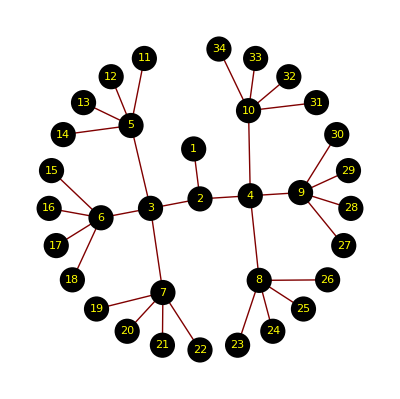

```mathematica
GraphPlot[F,VertexRenderingFunction->({Black,Disk[#,.2],Yellow,Text[#2,#]}&)]
```

```mathematica
<<GraphUtilities`
```

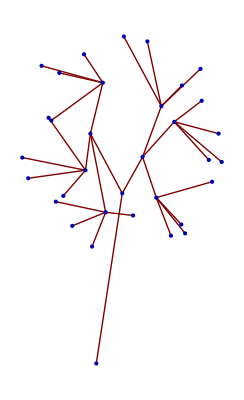

```mathematica
GRAFO=F;
vert=34;
coordenadas=Table[{GraphCoordinates[GRAFO]⟦i⟧⟦1⟧+RandomReal[{0,1}],GraphCoordinates[GRAFO]⟦i⟧⟦2⟧+RandomReal[{0,1}]},{i,vert}];
coordenadas⟦1,1⟧=2;
coordenadas⟦1,2⟧=-2;
Do[coordenadas⟦i,2⟧++;,{i,3,vert}]
GraphPlot[GRAFO,VertexCoordinateRules->coordenadas]
```

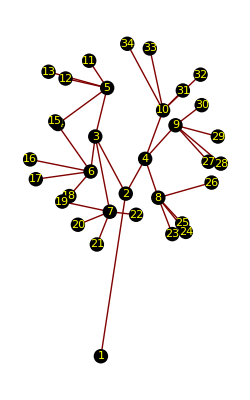

```mathematica
GraphPlot[GRAFO,VertexRenderingFunction->({Black,Disk[#,.2],Yellow,Text[#2,#]}&),VertexCoordinateRules->coordenadas]
```

#### Ejemplo 8.28.

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
Añadirlado2[matrizadyacencia_]:=Module[{},
listamatrices={};
grados={};

A=matrizadyacencia.matrizadyacencia;
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
AppendTo[grados,{A[[i,i]],A[[j,j]]}];

];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];

posiciones=Table[{i},{i,Length[grados]}];
Isomorfas={};Isomorfas2={};
While[posiciones≠{},
parte=Union[Position[grados,grados[[posiciones[[1,1]]]]],Position[grados,{grados[[posiciones[[1,1]],2]],grados[[posiciones[[1,1]],1]]}]];
parte2=parte;

If[Length[parte2]>1,

Do[
A1=listamatrices[[parte2[[1,1]]]].listamatrices[[parte2[[1,1]]]];
A2=listamatrices[[parte2[[k1,1]]]].listamatrices[[parte2[[k1,1]]]];

A3=A1.listamatrices[[parte2[[1,1]]]];
A4=A2.listamatrices[[parte2[[k1,1]]]];
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];
tabla4=Sort[Table[A4[[i1,i1]],{i1,n}]];

A5=A1.A1;
A6=A2.A2;
tabla5=Sort[Table[A5[[i1,i1]],{i1,n}]];
tabla6=Sort[Table[A6[[i1,i1]],{i1,n}]];


If[tabla3==tabla4 && tabla5==tabla6,
AppendTo[Isomorfas2,parte2[[k1]]];];

,{k1,2,Length[parte2]}];
parte2=Complement[parte2,Union[{parte[[1]]},Isomorfas2]];
Isomorfas=Union[Isomorfas,Isomorfas2];
Isomorfas2={};
];

posiciones=Complement[posiciones,parte];
];

listamatrices=Delete[listamatrices,Isomorfas]

];
```

```mathematica
tiempo=TimeUsed[];
nlados=8;
n=7;
matrizadyacencia=Table[0,{i,n},{j,n}];

listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado2[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

0.. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 2 *************

DIVIDIMOS EN 2 CLASES

0.. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 7 *************

DIVIDIMOS EN 5 CLASES

0.016. Total: 9

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 4 LADOS: 20 *************

DIVIDIMOS EN 10 CLASES

0.031. Total: 19

-------> Añadimos nuevo lado a 10 grafos

Van 1

************* DE 5 LADOS: 57 *************

DIVIDIMOS EN 21 CLASES

0.063. Total: 40

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 6 LADOS: 148 *************

DIVIDIMOS EN 41 CLASES

0.156. Total: 81

-------> Añadimos nuevo lado a 41 grafos

Van 1

************* DE 7 LADOS: 304 *************

DIVIDIMOS EN 65 CLASES

0.36. Total: 146

-------> Añadimos nuevo lado a 65 grafos

Van 1

************* DE 8 LADOS: 498 *************

DIVIDIMOS EN 97 CLASES

0.703. Total: 243

Totales: 243 Tiempo empleado: 0.703

```mathematica
CONEXO[A_]:=Module[{i,j,B},
B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
conexo=True;
Do[
Do[If[i≠j && B[[i,j]]==0,conexo=False;];
,{i,Dimensions[B][[1]]}];
,{j,Dimensions[B][[1]]}];
conexo
]
```

```mathematica
CICLOSELEMENTALES[vertice1_,longitud_,A_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,caminos[[k]]];
If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud-1}];
caminostemp={};
Do[If[A[[caminos[[k]][[longitud]],vertice1]]==1,AppendTo[caminostemp,Append[caminos[[k]],vertice1]];];,{k,Length[caminos]}];
caminostemp
];
```

```mathematica
BOSQUE[matrizadyacencia_]:=Module[{n,longitud,i,},
bosque=True;
n=Dimensions[matrizadyacencia][[1]];
Do[
potencia=MatrixPower[matrizadyacencia,longitud];
Do[
If[potencia[[i,i]]>0, 
If[CICLOSELEMENTALES[i,longitud,matrizadyacencia]≠{},bosque=False;Break[];];
];
,{i,n}];
If[bosque==False,Break[];];
,{longitud,3,n}];
bosque
];
```

41

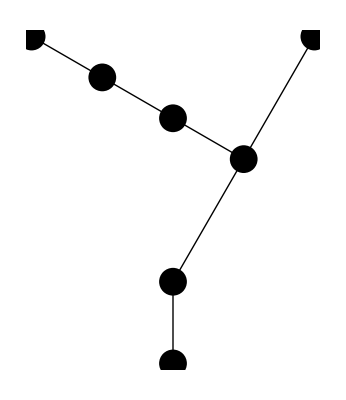

46

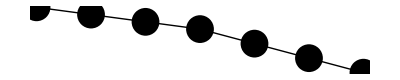

48

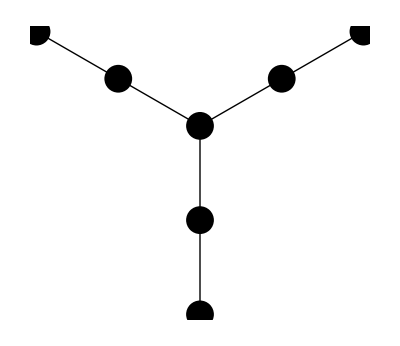

51

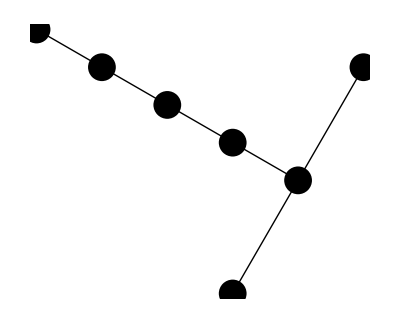

59

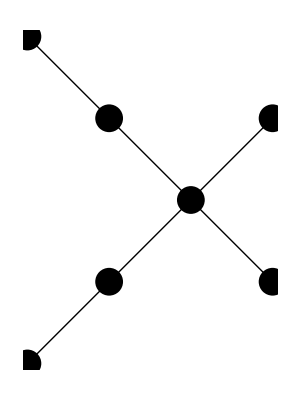

65

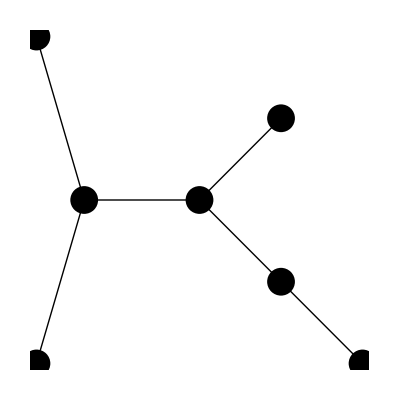

67

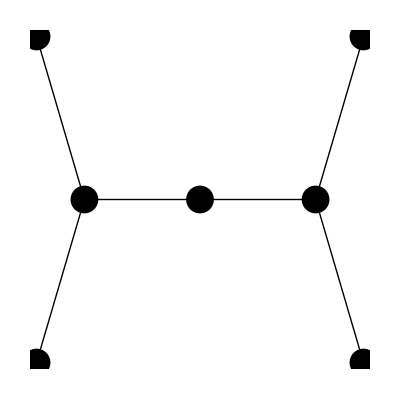

69

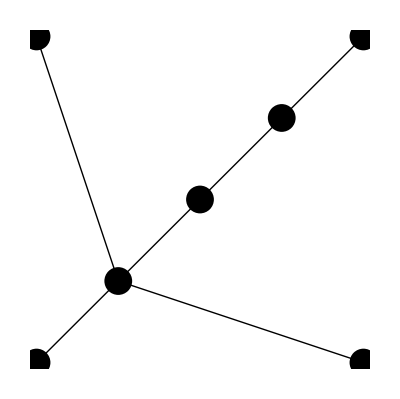

73

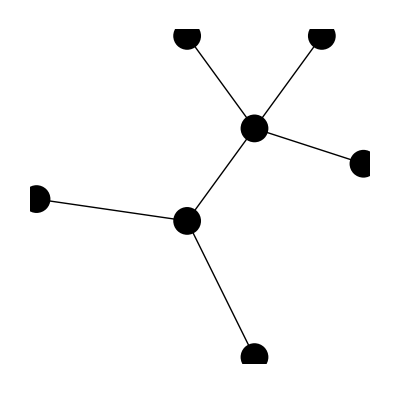

79

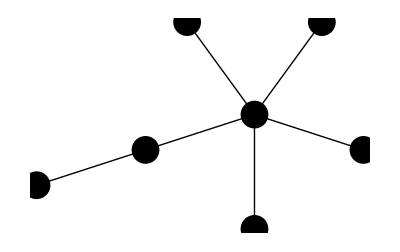

81

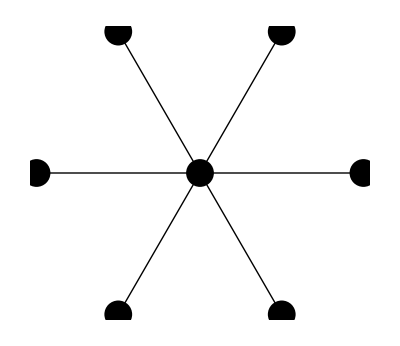

```mathematica
Do[
   If[CONEXO[listamatrices1[[i]]],
      If[BOSQUE[listamatrices1[[i]]],
         Print[i];
         Print[GraphPlot[listamatrices1[[i]],PlotStyle->{Black,PointSize[.05]}]];
];];
,{i,Length[listamatrices1]}];
```

### 3.2. ÁRBOLES Y BOSQUES. NÚMERO DE LADOS

#### Función 8.21. ARBOL[]

```mathematica
CONEXO[A_]:=Module[{i,j,B},
B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
conexo=True;
Do[
Do[If[i≠j && B[[i,j]]==0,conexo=False;];
,{i,Dimensions[B][[1]]}];
,{j,Dimensions[B][[1]]}];
conexo
]
```

```mathematica
ARBOL[matrizadyacencia_]:=Module[{i,j,lados},
arbol=False;
If[CONEXO[matrizadyacencia],
arbol=(Dimensions[matrizadyacencia][[1]]==(Sum[matrizadyacencia[[i,j]],{i,Dimensions[matrizadyacencia][[1]]},{j,Dimensions[matrizadyacencia][[2]]}]/2)+1);
];
arbol
]
```

#### Función 8.22. BOSQUE2[]

```mathematica
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto≠{},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]≠0,AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];
componentesconexas
]
```

```mathematica
IND2[W1_,matrizadyacencia_]:=Module[{n,i,j},
n=Length[W1];
matrizadyacencia2=Table[0,{i,n},{j,n}];
Do[Do[
matrizadyacencia2[[i,j]]=matrizadyacencia[[W1[[i]],W1[[j]]]];
,{i,n}];
,{j,n}];
matrizadyacencia2
];
```

```mathematica
BOSQUE2[matrizadyacencia_]:=Module[{componentes,i},
bosque=True;
componentes=COMPONENTESCONEXAS[matrizadyacencia];
Do[
If[ARBOL[IND2[componentes[[i]],matrizadyacencia]]==False,bosque=False];
,{i,Length[componentes]}];
bosque]
```

#### Ejemplo 8.29.

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
Añadirlado2[matrizadyacencia_]:=Module[{},
listamatrices={};
grados={};

A=matrizadyacencia.matrizadyacencia;
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
AppendTo[grados,{A[[i,i]],A[[j,j]]}];

];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];

posiciones=Table[{i},{i,Length[grados]}];
Isomorfas={};Isomorfas2={};
While[posiciones≠{},
parte=Union[Position[grados,grados[[posiciones[[1,1]]]]],Position[grados,{grados[[posiciones[[1,1]],2]],grados[[posiciones[[1,1]],1]]}]];
parte2=parte;

If[Length[parte2]>1,

Do[
A1=listamatrices[[parte2[[1,1]]]].listamatrices[[parte2[[1,1]]]];
A2=listamatrices[[parte2[[k1,1]]]].listamatrices[[parte2[[k1,1]]]];

A3=A1.listamatrices[[parte2[[1,1]]]];
A4=A2.listamatrices[[parte2[[k1,1]]]];
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];
tabla4=Sort[Table[A4[[i1,i1]],{i1,n}]];

A5=A1.A1;
A6=A2.A2;
tabla5=Sort[Table[A5[[i1,i1]],{i1,n}]];
tabla6=Sort[Table[A6[[i1,i1]],{i1,n}]];


If[tabla3==tabla4 && tabla5==tabla6,
AppendTo[Isomorfas2,parte2[[k1]]];];

,{k1,2,Length[parte2]}];
parte2=Complement[parte2,Union[{parte[[1]]},Isomorfas2]];
Isomorfas=Union[Isomorfas,Isomorfas2];
Isomorfas2={};
];

posiciones=Complement[posiciones,parte];
];

listamatrices=Delete[listamatrices,Isomorfas]

];
```

```mathematica
tiempo=TimeUsed[];
nlados=7;
n=8;
matrizadyacencia=Table[0,{i,n},{j,n}];

listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado2[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

0.. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 2 *************

DIVIDIMOS EN 2 CLASES

0.. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 7 *************

DIVIDIMOS EN 5 CLASES

0.015. Total: 9

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 4 LADOS: 23 *************

DIVIDIMOS EN 11 CLASES

0.047. Total: 20

-------> Añadimos nuevo lado a 11 grafos

Van 1

************* DE 5 LADOS: 73 *************

DIVIDIMOS EN 24 CLASES

0.125. Total: 44

-------> Añadimos nuevo lado a 24 grafos

Van 1

************* DE 6 LADOS: 228 *************

DIVIDIMOS EN 56 CLASES

0.297. Total: 100

-------> Añadimos nuevo lado a 56 grafos

Van 1

************* DE 7 LADOS: 595 *************

DIVIDIMOS EN 115 CLASES

0.844. Total: 215

Totales: 215 Tiempo empleado: 0.844

```mathematica
CONEXO[A_]:=Module[{i,j,B},
B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
conexo=True;
Do[
Do[If[i≠j && B[[i,j]]==0,conexo=False;];
,{i,Dimensions[B][[1]]}];
,{j,Dimensions[B][[1]]}];
conexo
]
```

```mathematica
ARBOL[matrizadyacencia_]:=Module[{i,j,lados},
arbol=False;
If[CONEXO[matrizadyacencia],
arbol=(Dimensions[matrizadyacencia][[1]]==(Sum[matrizadyacencia[[i,j]],{i,Dimensions[matrizadyacencia][[1]]},{j,Dimensions[matrizadyacencia][[2]]}]/2)+1);
];
arbol
]
```

```mathematica
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto≠{},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]≠0,AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];
componentesconexas
]
```

```mathematica
IND2[W1_,matrizadyacencia_]:=Module[{n,i,j},
n=Length[W1];
matrizadyacencia2=Table[0,{i,n},{j,n}];
Do[Do[
matrizadyacencia2[[i,j]]=matrizadyacencia[[W1[[i]],W1[[j]]]];
,{i,n}];
,{j,n}];
matrizadyacencia2
];
```

```mathematica
BOSQUE2[matrizadyacencia_]:=Module[{componentes,i},
bosque=True;
componentes=COMPONENTESCONEXAS[matrizadyacencia];
Do[
If[ARBOL[IND2[componentes[[i]],matrizadyacencia]]==False,bosque=False];
,{i,Length[componentes]}];
bosque]
```

1

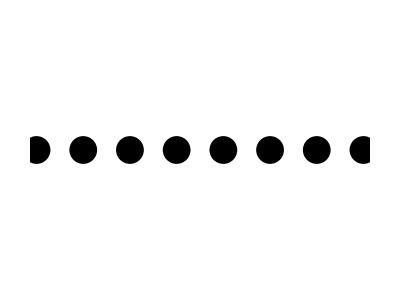

2

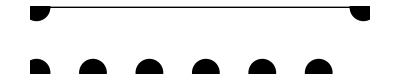

3

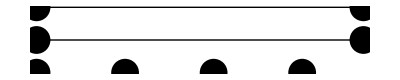

4

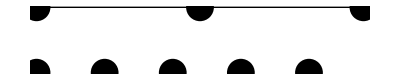

5

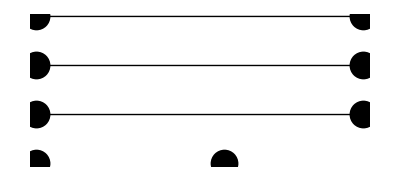

6

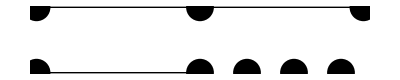

7

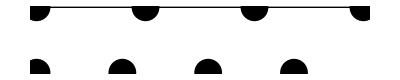

9

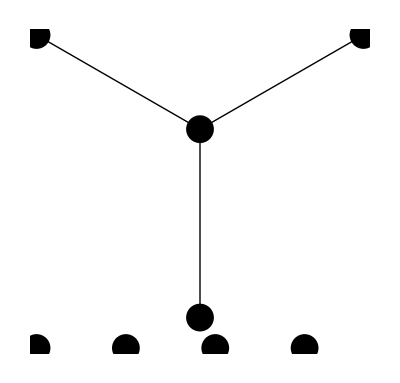

10

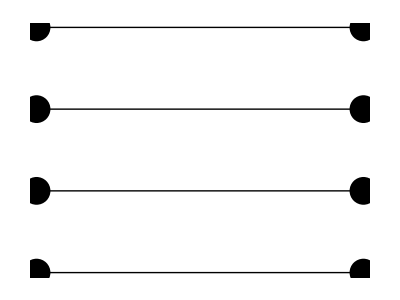

11

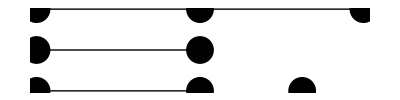

12

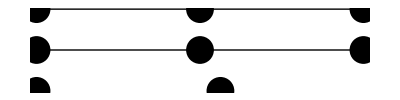

13

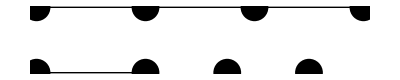

15

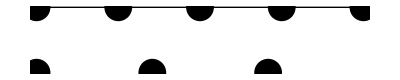

16

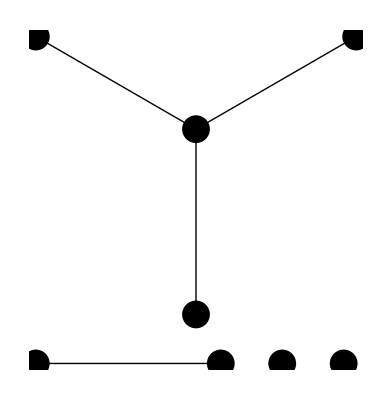

19

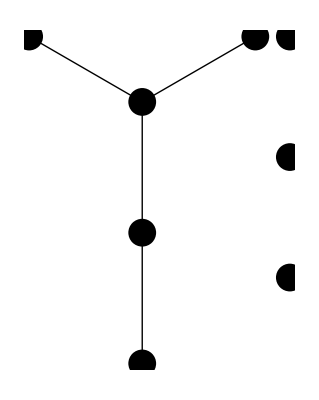

20

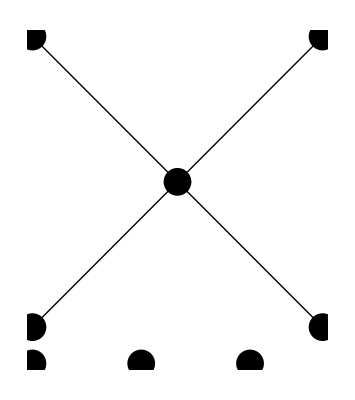

21

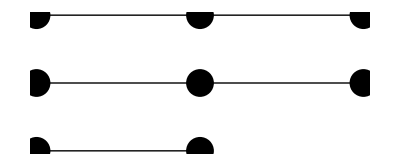

22

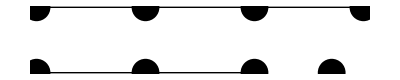

23

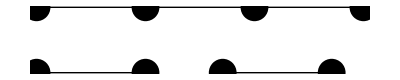

25

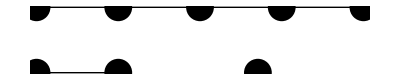

26

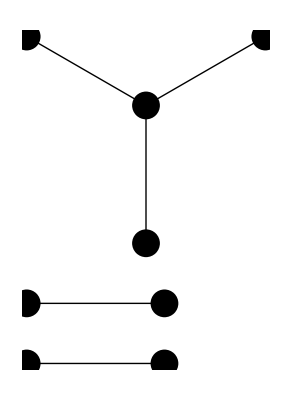

29

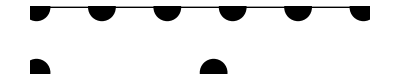

32

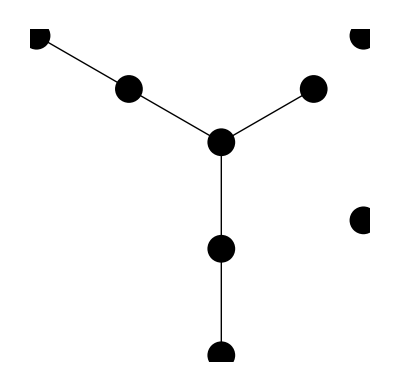

34

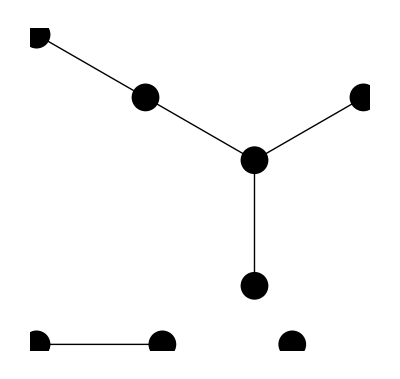

35

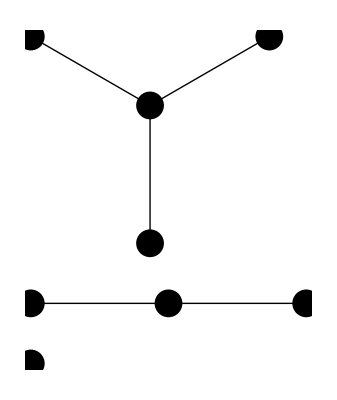

36

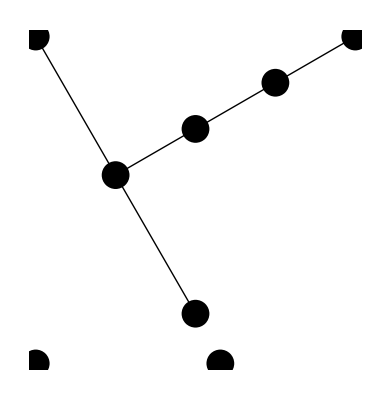

37

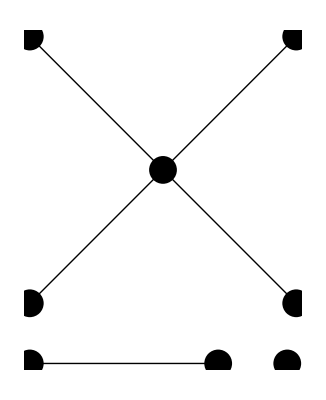

38

-Graphics-

43

-Graphics-

44

-Graphics-

45

-Graphics-

46

-Graphics-

48

-Graphics-

49

-Graphics-

50

-Graphics-

54

-Graphics-

58

-Graphics-

59

-Graphics-

61

-Graphics-

62

-Graphics-

63

-Graphics-

66

-Graphics-

74

-Graphics-

80

-Graphics-

81

-Graphics-

82

-Graphics-

84

-Graphics-

86

-Graphics-

87

-Graphics-

88

-Graphics-

92

-Graphics-

98

-Graphics-

100

-Graphics-

104

-Graphics-

105

-Graphics-

107

-Graphics-

108

-Graphics-

109

-Graphics-

110

-Graphics-

113

-Graphics-

124

-Graphics-

140

-Graphics-

145

-Graphics-

149

-Graphics-

154

-Graphics-

160

-Graphics-

165

-Graphics-

178

-Graphics-

190

-Graphics-

192

-Graphics-

195

-Graphics-

197

-Graphics-

201

-Graphics-

205

-Graphics-

213

-Graphics-

215

-Graphics-

```mathematica
Do[
If[BOSQUE2[listamatrices1[[i]]]
,Print[i];
         Print[GraphPlot[listamatrices1[[i]],PlotStyle->{Black,PointSize[.05]}]];];
,{i,Length[listamatrices1]}]
```

## 4. OTROS EJEMPLOS

#### Ejemplo 8.30.

```mathematica
matrizadyacencia={{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      				   {1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      				   {0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},
      				   {0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1},
      					   {0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0},
      					   {0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0},
      				   {0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0},
      					   {0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},
      					   {0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0},
      					   {0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      				   {0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
      				   {0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},
      					   {0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
GraphPlot[matrizadyacencia,PlotStyle->{Black,PointSize[.05]}]
```

-Graphics-

```mathematica
CICLOSELEMENTALES[vertice1_,longitud_,A_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,caminos[[k]]];
If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud-1}];
caminostemp={};
Do[If[A[[caminos[[k]][[longitud]],vertice1]]==1,AppendTo[caminostemp,Append[caminos[[k]],vertice1]];];,{k,Length[caminos]}];
caminostemp
];
```

```mathematica
CICLOSELEMENTALES[1,5,matrizadyacencia]
```

{{1,2,5,6,3,1},{1,2,10,9,4,1},{1,3,6,5,2,1},{1,3,7,8,4,1},{1,4,8,7,3,1},{1,4,9,10,2,1}}

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

```mathematica
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
```

```mathematica
<<Combinatorica`
```

KSubsets::shdw: Symbol "KSubsets" appears in multiple contexts {"Combinatorica`", "Global`"}; definitions in context "Combinatorica`" may shadow or be shadowed by other definitions.

```mathematica
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
```

```mathematica
HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

```mathematica
PLANO[matrizadyacencia]
```

True

```mathematica
CONEXO[A_]:=Module[{i,j,B},
B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
conexo=True;
Do[
Do[If[i≠j && B[[i,j]]==0,conexo=False;];
,{i,Dimensions[B][[1]]}];
,{j,Dimensions[B][[1]]}];
conexo
]
```

```mathematica
CONEXO[matrizadyacencia]
```

True

```mathematica
BOSQUE[matrizadyacencia_]:=Module[{n,longitud,i,},
bosque=True;
n=Dimensions[matrizadyacencia][[1]];
Do[
potencia=MatrixPower[matrizadyacencia,longitud];
Do[
If[potencia[[i,i]]>0, 
If[CICLOSELEMENTALES[i,longitud,matrizadyacencia]≠{},bosque=False;Break[];];
];
,{i,n}];
If[bosque==False,Break[];];
,{longitud,3,n}];
bosque
];
```

```mathematica
BOSQUE[matrizadyacencia]
```

False

```mathematica
ARBOL[matrizadyacencia_]:=Module[{i,j,lados},
arbol=False;
If[CONEXO[matrizadyacencia],
arbol=(Dimensions[matrizadyacencia][[1]]==(Sum[matrizadyacencia[[i,j]],{i,Dimensions[matrizadyacencia][[1]]},{j,Dimensions[matrizadyacencia][[2]]}]/2)+1);
];
arbol
]
```

```mathematica
ARBOL[matrizadyacencia]
```

False

```mathematica
COLOREAR[matrizadyacencia_]:=Module[{COLORES,colores,color,coloreartemp,i,j},colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};colorear={1};color=1;Do[coloreartemp=colorear;Do[If[matrizadyacencia⟦j,i⟧==1,coloreartemp=Complement[coloreartemp,{colorear⟦j⟧}]];,{j,i-1}];If[coloreartemp=={},color++;AppendTo[colorear,color];,AppendTo[colorear,coloreartemp⟦1⟧];];,{i,2,Dimensions[matrizadyacencia]⟦1⟧}];Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.3],White,Text[#2,{#1[[1]],#1[[2]]}]}&)]]
```

```mathematica
COLOREAR[matrizadyacencia]
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Verde

Vértice 7, color Negro

Vértice 8, color Verde

Vértice 9, color Negro

Vértice 10, color Verde

Vértice 11, color Rojo

Vértice 12, color Negro

Vértice 13, color Rojo

Vértice 14, color Negro

Vértice 15, color Rojo

Vértice 16, color Negro

Vértice 17, color Negro

Vértice 18, color Rojo

Vértice 19, color Rojo

Vértice 20, color Negro

Vértice 21, color Negro

Vértice 22, color Rojo

Vértice 23, color Rojo

Vértice 24, color Negro

Vértice 25, color Negro

Vértice 26, color Rojo

Vértice 27, color Rojo

Vértice 28, color Negro

-Graphics-

```mathematica
REGIONES={{1,2,10,9,4,1},{1,2,5,6,3,1},{1,3,7,8,4,1},{2,5,11,28,11,17,11,5,6,12,18,12,19,12,6,3,7,13,20,13,21,13,7,8,14,22,14,23,14,8,4,9,15,24,15,25,15,9,10,16,,26,16,27,16,10,2}};
```

```mathematica
SUCLADOS2[vertices_]:=Module[{i},
lados={};
Do[If[vertices[[i]]<vertices[[i+1]],AppendTo[lados,vertices[[i]]->vertices[[i+1]]],AppendTo[lados,vertices[[i+1]]->vertices[[i]]]];,{i,Length[vertices]-1}];
lados
]
```

```mathematica
GRAFOREGIONES[REGIONES_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[REGIONES]},{j,Length[REGIONES]}];
regioneslados={};
Do[AppendTo[regioneslados,SUCLADOS2[REGIONES[[i]]]],{i,Length[REGIONES]}];
ladosext={};
Do[
resto={};
Do[
If[i≠j,resto=Union[resto,regioneslados[[j]]]];
,{j,Length[regioneslados]}];
ladosext=Union[ladosext,Complement[regioneslados[[i]],resto]];
,{i,Length[regioneslados]}];
Do[Do[
If[i≠j,
If[Intersection[regioneslados[[i]],regioneslados[[j]]]≠{},
matrizadyacencia[[i,j]]=1;
matrizadyacencia[[j,i]]=1;
];
];
,{j,Length[REGIONES]}];
,{i,Length[REGIONES]}];
matrizadyacencia
];
```

```mathematica
A=GRAFOREGIONES[REGIONES]
```

{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
```

```mathematica
NCOLORACIONES[A,3]
```

{}

```mathematica
NCOLORACIONES[A,4]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
NUMEROCROMATICO[matrizadyacencia]
```

4

#### Ejemplo 8.31.

```mathematica
<<Combinatorica`
```

```mathematica
grafos={FranklinGraph,CoxeterGraph,FolkmanGraph,ChvatalGraph,Hypercube[5],MeredithGraph};
```

```mathematica
ShowGraphArray[{grafos[[1 ;;3]],grafos[[4;;6]]}]
```

-Graphics-

```mathematica
Do[Print[i,"   Plano: ",PlanarQ[grafos[[i]]],"   Árbol: ",TreeQ[grafos[[i]]]],{i,Length[grafos]}];
```

1   Plano: False   Árbol: False

2   Plano: False   Árbol: False

3   Plano: False   Árbol: False

4   Plano: False   Árbol: False

5   Plano: False   Árbol: False

6   Plano: False   Árbol: False

```mathematica
numeroscromaticos=Table[ChromaticNumber[grafos[[i]]],{i,Length[grafos]}]
```

{2,3,2,4,2,3}

```mathematica
optimas=Table[MinimumVertexColoring[grafos[[i]]],{i,Length[grafos]}]
```

{{1,2,2,1,1,2,2,1,1,2,1,2},{1,2,2,1,1,2,3,2,1,2,1,1,2,1,1,2,3,3,3,1,2,2,1,3,3,2,1,3},{1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1},{1,2,1,1,3,1,2,3,2,3,4,2},{1,2,1,2,2,1,2,1,2,1,2,1,1,2,1,2,1,2,1,2,2,1,2,1,2,1,2,1,1,2,1,2},{1,1,1,1,2,2,2,1,1,1,1,2,2,2,2,2,2,2,1,1,1,2,2,2,2,1,1,1,2,1,1,1,3,3,3,1,1,1,1,2,2,2,2,2,2,2,1,1,1,1,2,2,1,3,3,3,2,2,2,2,1,1,1,1,1,1,3,2,2,2}}

```mathematica
Do[
optima=optimas[[k]];
numerocromatico=numeroscromaticos[[k]];
coloracion={};
colores={Black,Red,Green,Blue,Pink,Yellow,Orange,Violet};
Do[
color={VertexColor->colores[[i]]};
Do[
If[optima[[j]]==i,PrependTo[color,j]];
,{j,Length[optima]}];
AppendTo[coloracion,color];
,{i,numerocromatico}];
Print[ShowGraph[grafos[[k]],Table[coloracion[[i]],{i,numerocromatico}],VertexLabel->True]];
Print[coloracion];
,{k,Length[grafos]}];
```

-Graphics-

{{11,9,8,5,4,1,VertexColor→GrayLevel[0]},{12,10,7,6,3,2,VertexColor→RGBColor[1,0,0]}}

-Graphics-

{{27,23,20,15,14,12,11,9,5,4,1,VertexColor→GrayLevel[0]},{26,22,21,16,13,10,8,6,3,2,VertexColor→RGBColor[1,0,0]},{28,25,24,19,18,17,7,VertexColor→RGBColor[0,1,0]}}

-Graphics-

{{20,19,18,17,16,5,4,3,2,1,VertexColor→GrayLevel[0]},{15,14,13,12,11,10,9,8,7,6,VertexColor→RGBColor[1,0,0]}}

-Graphics-

{{6,4,3,1,VertexColor→GrayLevel[0]},{12,9,7,2,VertexColor→RGBColor[1,0,0]},{10,8,5,VertexColor→RGBColor[0,1,0]},{11,VertexColor→RGBColor[0,0,1]}}

-Graphics-

{{31,29,28,26,24,22,19,17,15,13,12,10,8,6,3,1,VertexColor→GrayLevel[0]},{32,30,27,25,23,21,20,18,16,14,11,9,7,5,4,2,VertexColor→RGBColor[1,0,0]}}

-Graphics-

{{66,65,64,63,62,61,53,50,49,48,47,39,38,37,36,32,31,30,28,27,26,21,20,19,11,10,9,8,4,3,2,1,VertexColor→GrayLevel[0]},{70,69,68,60,59,58,57,52,51,46,45,44,43,42,41,40,29,25,24,23,22,18,17,16,15,14,13,12,7,6,5,VertexColor→RGBColor[1,0,0]},{67,56,55,54,35,34,33,VertexColor→RGBColor[0,1,0]}}

#### Ejemplo 8.32.

```mathematica
matrizadyacencia={{0,0,1,1,1},{0,0,1,1,1},{1,1,0,1,1},{1,1,1,0,1},{1,1,1,1,0}};
```

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
```

```mathematica
DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

```mathematica
DIBUJAR[matrizadyacencia]
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Rojo

Vértice 4, color Verde

Vértice 5, color Azul

-Graphics-

```mathematica
W={1,2,3,4,5,6,7,8} ;
F={1->4,1->6,1->7,1->8,2->4,2->5,2->7,2->8,3->8,4->5,4->6,4->7,5->7};
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
matrizadyacencia=MATRIZADYACENCIA[W,F];
```

```mathematica
DIBUJAR[matrizadyacencia]
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Verde

Vértice 6, color Verde

Vértice 7, color Azul

Vértice 8, color Rojo

-Graphics-

```mathematica
Length[NCOLORACIONES[matrizadyacencia,4]]
```

720

## 5. EJERCICIOS

#### EJERCICIO 8.14.

```mathematica
A1={{0,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0}};
REGIONES={{1,2,4,6,5,3,1},{5,8,6,4,2,1,3,5},{5,6,7,5},{6,7,8,6},{7,8,10,12,11,9,7}};
```

```mathematica
REGILIM[REGIONES_]:=Module[{regioneslados,i,k,j,ladosext,resto},
regioneslados={};
Do[AppendTo[regioneslados,SUCLADOS2[REGIONES[[i]]]],{i,Length[REGIONES]}];
ladosext={};
Do[
resto={};
Do[
If[i≠j,resto=Union[resto,regioneslados[[j]]]];
,{j,Length[regioneslados]}];
ladosext=Union[ladosext,Complement[regioneslados[[i]],resto]];
,{i,Length[regioneslados]}];

ciclo={ladosext[[1]][[1]],ladosext[[1]][[2]]};
ladosext=Complement[ladosext,{ladosext[[1]]}];
While[ladosext≠{},
k=1;
While[ladosext[[k]][[1]]!=Last[ciclo] && ladosext[[k]][[2]]!=Last[ciclo],k++;];

If[ladosext[[k]][[1]]==Last[ciclo],AppendTo[ciclo,ladosext[[k]][[2]]],AppendTo[ciclo,ladosext[[k]][[1]]]];
ladosext=Complement[ladosext,{ladosext[[k]]}];
];
ciclo
];
```

```mathematica
REGILIM[REGIONES]
```

{5,7,9,11,12,10,8,5}

```mathematica
MatrixForm[GRAFOREGIONES[REGIONES]]
```

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

```mathematica
A={{0,1,1,1,0,0,0,0,0,0},{1,0,1,0,0,1,0,0,0,0},{1,1,0,0,1,1,0,0,0},{1,0,0,0,1,0,0,1,0,0},{0,0,1,1,0,0,1,1,0,0},{0,1,1,0,0,0,1,0,0,1},{0,0,0,0,1,1,0,1,1,0},{0,0,0,1,1,0,1,0,1,0},{0,0,0,0,0,0,1,1,0,1},{0,0,0,0,0,1,0,0,1,0}};
```

```mathematica
REGIONES={{1,2,4,6,5,3,1},{5,8,6,4,2,1,3,5},{5,6,7,5},{6,7,8,6},{7,8,10,12,11,9,7}};
```

```mathematica
R=Join[{REGILIM[REGIONES]},REGIONES]
```

{{5,7,9,11,12,10,8,5},{1,2,4,6,5,3,1},{5,8,6,4,2,1,3,5},{5,6,7,5},{6,7,8,6},{7,8,10,12,11,9,7}}

```mathematica
A=GRAFOREGIONES[R]
```

{{0,0,1,1,0,1},{0,0,1,1,0,0},{1,1,0,0,1,0},{1,1,0,0,1,0},{0,0,1,1,0,1},{1,0,0,0,1,0}}

```mathematica
NCOLORACIONES[A,2]
```

{{1,1,2,2,1,2},{2,2,1,1,2,1}}

```mathematica
REGIONES2={{1,3,5,4,1},{1,2,3,1},{2,3,6,2},{3,5,7,6,3},{4,5,8,4},{5,7,8,5},{7,8,9,7},{6,7,9,10,6}};
```

```mathematica
R2=Join[{REGILIM[REGIONES2]},REGIONES2]
```

{{1,2,6,10,9,8,4,1},{1,3,5,4,1},{1,2,3,1},{2,3,6,2},{3,5,7,6,3},{4,5,8,4},{5,7,8,5},{7,8,9,7},{6,7,9,10,6}}

```mathematica
A2=GRAFOREGIONES[R2]
```

{{0,1,1,1,0,1,0,1,1},{1,0,1,0,1,1,0,0,0},{1,1,0,1,0,0,0,0,0},{1,0,1,0,1,0,0,0,0},{0,1,0,1,0,0,1,0,1},{1,1,0,0,0,0,1,0,0},{0,0,0,0,1,1,0,1,0},{1,0,0,0,0,0,1,0,1},{1,0,0,0,1,0,0,1,0}}

```mathematica
NCOLORACIONES[A2,3]
```

{{1,2,3,2,1,3,2,3,2},{1,2,3,2,3,3,1,3,2},{1,2,3,2,3,3,2,3,2},{1,3,2,3,1,2,3,2,3},{1,3,2,3,2,2,1,2,3},{1,3,2,3,2,2,3,2,3},{2,1,3,1,2,3,1,3,1},{2,1,3,1,3,3,1,3,1},{2,1,3,1,3,3,2,3,1},{2,3,1,3,1,1,2,1,3},{2,3,1,3,1,1,3,1,3},{2,3,1,3,2,1,3,1,3},{3,1,2,1,2,2,1,2,1},{3,1,2,1,2,2,3,2,1},{3,1,2,1,3,2,1,2,1},{3,2,1,2,1,1,2,1,2},{3,2,1,2,1,1,3,1,2},{3,2,1,2,3,1,2,1,2}}